```mathematica
Off[Inverse::luc]
Off[LinearSolve::luc]

workingdirectory=$HomeDirectory<>"/kette_repo/ComptonLIT/systems/mul_deuteron_miwchan";
SetDirectory[workingdirectory];
matrixfilenames=Select[FileNames[All,"./LITstate"],StringMatchQ[#,"*MATOUTB*"]&]
dim=Range[Length[matrixfilenames]];
```

{./LITstate/MATOUTB}

```mathematica
normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];{(Transpose[transf].DiagonalMatrix[μ^(-1/2)])}]
decompose[threshold_,norm_,ham_]:= Block[{},Oμ=normreg[threshold,norm][[1]];{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];];
```

```mathematica
ℏc=197.32858;
Mnucl=(938.2796+939.5731)/2.;
HNc={};HNuc={};
thr=10^-13;
Do[
str=OpenRead[matrixfilenames[[i]],BinaryFormat->True];
headmarker=BinaryRead[str,"Integer32",ByteOrdering->$ByteOrdering];
NormHamMat=BinaryReadList[str,"Real64",ByteOrdering->$ByteOrdering];
JbasisDim=IntegerPart[Sqrt[Length[NormHamMat]*0.5]];
Close[str];

norm=ArrayReshape[NormHamMat[[1;;JbasisDim^2]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+1;;]],{JbasisDim,JbasisDim}];
evnorm=Sort[Eigenvalues[norm],Re[#1]>Re[#2]&];
decompose[thr,norm,ham];

evhamunnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;
evhamnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];

evn=Eigenvalues[norm];


Print["Condition number ℕ_ij = ",Abs[Max[evn]/Min[evn]]];
Print["EV_full(ℍ) = ",evhamnorm[[-2;;]]];
Print["EV_(EV (𝟙) > threshold)(ℍ) = ",Sort[λs,Re[#1]>Re[#2]&][[-2;;]]];

thh=100;(*Max[Abs[λs]];*)
AppendTo[HNc,evnorm];
AppendTo[HNuc,evhamunnorm];
,{i,dim}]
(*Grid[{{"ev(⟨i|j⟩)\n","ev(⟨i|H_nucl|j⟩)","ev(⟨α|H_nucl|β⟩) ev(𝟙) > "ScientificForm[thr]},{Sort[evn,Re[#1]>Re[#2]&]//MatrixForm,Sort[Eigenvalues[{ham,norm}],R~e[#1]>Re[#2]&]//MatrixForm,Sort[λs,Re[#1]>Re[#2]&]//MatrixForm}}]*)
```

Condition number ℕ_ij = 8.04787×10^15

EV_full(ℍ) = {-32.6407+0. ⅈ,-88.5167+0. ⅈ}

EV_(EV (𝟙) > threshold)(ℍ) = {0.00158678,0.000532418}

```mathematica
HNc
```

{{25.8947,22.39,17.9777,13.7333,10.1936,7.45721,5.41368,3.90612,2.80058,1.99377,1.40441,0.972739,0.659612,0.437766,0.284907,0.182257,0.11484,0.071405,0.0438862,0.0267114,0.0161382,0.00971263,0.00585782,0.00357448,0.0022226,0.00138679,0.000843329,0.000496566,0.000285513,0.000161495,0.0000902403,0.000049928,0.0000273875,0.0000149055,8.05217×10^-6,4.31882×10^-6,2.30025×10^-6,1.21668×10^-6,6.39094×10^-7,3.33373×10^-7,1.72686×10^-7,8.88179×10^-8,4.53495×10^-8,2.29815×10^-8,1.1556×10^-8,5.76402×10^-9,2.85077×10^-9,1.39742×10^-9,6.78584×10^-10,3.26228×10^-10,1.55163×10^-10,7.29656×10^-11,3.39033×10^-11,1.55652×10^-11,7.07212×10^-12,3.20989×10^-12,1.52715×10^-12,8.61306×10^-13,4.58669×10^-13,2.06837×10^-13,1.05309×10^-13,7.79792×10^-14,3.29402×10^-15,2.88931×10^-15,2.52256×10^-15,2.36533×10^-15,2.23073×10^-15,2.22032×10^-15,2.12329×10^-15,1.91162×10^-15,1.77995×10^-15,1.73147×10^-15,1.66028×10^-15,1.51263×10^-15,1.43971×10^-15,1.33472×10^-15,1.26623×10^-15,1.25579×10^-15,1.17967×10^-15,1.06221×10^-15,9.4964×10^-16,8.7837×10^-16,8.25435×10^-16,5.93206×10^-16,5.32315×10^-16,4.83823×10^-16,4.15886×10^-16,3.2349×10^-16,2.27037×10^-16,1.40598×10^-16,7.73424×10^-17,-4.16445×10^-17,-1.60626×10^-16,-1.70076×10^-16,-2.25033×10^-16,-3.3316×10^-16,-4.55143×10^-16,-5.09947×10^-16,-5.97195×10^-16,-6.9113×10^-16,-7.72496×10^-16,-9.92117×10^-16,-1.14602×10^-15,-1.33094×10^-15,-1.35454×10^-15,-1.40892×10^-15,-1.5183×10^-15,-1.6067×10^-15,-1.71862×10^-15,-1.80468×10^-15,-2.06011×10^-15,-2.21897×10^-15,-2.44164×10^-15,-2.69115×10^-15,-2.79036×10^-15,-3.21758×10^-15}}

```mathematica
data1={};
data2={};
Do[
AppendTo[data1,Select[Re[HNuc[[i]]],Abs[#]<thh&]];AppendTo[data2,Select[Re[HNc[[i]]],Abs[#]<thh&]];
,{i,dim}]
```

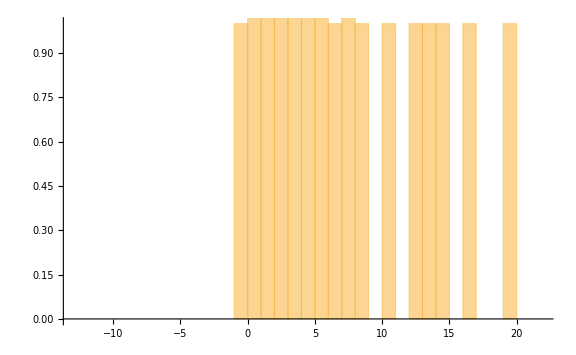

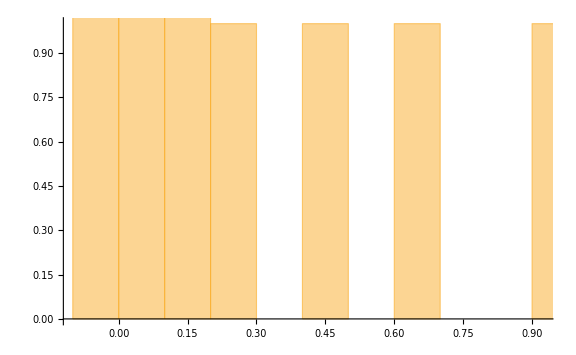

```mathematica
Histogram[data1,{1},PlotRange->{Automatic,{0,1}},ImageSize->Large]
Histogram[data2,{.1},PlotRange->{Automatic,{0,1}},ImageSize->Large]
```

```mathematica
norm//MatrixForm
```

(1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.0499631 | 0.0303994 | 0.0180295 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882971 | 0.0696745 | 0.0548108 | 0.0430088 | 0.0104585 | 0.00595221 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543416 | 0.000291471 | 0.000155294 | 0.000082283 | 0.0000433994 | 0.0336776 | 0.0263255 | 0.0205495 | 0.0160222 | 0.0124805 | 0.00971412 | 0.00755613 | 0.00587447 | 0.00456514 | 0.0035464 | 0.0000228046 | 0.0000119459 | 6.24183×10^-6 | 3.25461×10^-6 | 1.69413×10^-6 | 8.80612×10^-7 | 4.57222×10^-7 | 2.37171×10^-7 | 1.22932×10^-7 | 6.36789×10^-8 | 0.00275423 | 0.0021385 | 0.00166011 | 0.00128854 | 0.00100001 | 0.000776003 | 0.000602129 | 0.000467182 | 0.000362456 | 0.000281193 | 3.29691×10^-8 | 1.70621×10^-8 | 8.82703×10^-9 | 4.56534×10^-9 | 2.36065×10^-9 | 1.22042×10^-9 | 6.3085×10^-10 | 3.26054×10^-10 | 1.68502×10^-10 | 8.70725×10^-11 | 0.00021814 | 0.000169224 | 0.000131272 | 0.000101828 | 0.0000789905 | 0.0000612704 | 0.0000475267 | 0.0000368643 | 0.000028594 | 4.49911×10^-11 | 2.32468×10^-11 | 1.20108×10^-11 | 6.2051×10^-12 | 3.20601×10^-12 | 1.65615×10^-12 | 8.55598×10^-13 | 4.41972×10^-13 | 2.28308×10^-13 | 0.0000221803 | 0.0000172043 | 0.0000133447 | 0.0000103517 | 8.02795×10^-6 | 6.22756×10^-6 | 4.8301×10^-6 | 3.74709×10^-6 | 2.90606×10^-6 | 1.17953×10^-13 | 6.09319×10^-14 | 3.14765×10^-14 | 1.62634×10^-14 | 8.39743×10^-15 | 4.33909×10^-15 | 2.24106×10^-15 | 1.15816×10^-15 | 5.98075×10^-16
0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.473037 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.0499631 | 0.0303994 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882971 | 0.0696745 | 0.0548108 | 0.0180295 | 0.0104585 | 0.00595221 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543416 | 0.000291471 | 0.000155294 | 0.000082283 | 0.0430088 | 0.0336776 | 0.0263255 | 0.0205495 | 0.0160222 | 0.0124805 | 0.00971412 | 0.00755612 | 0.00587448 | 0.00456514 | 0.0000433994 | 0.0000228046 | 0.0000119459 | 6.24182×10^-6 | 3.25462×10^-6 | 1.69413×10^-6 | 8.80613×10^-7 | 4.57221×10^-7 | 2.37172×10^-7 | 1.22932×10^-7 | 0.00354641 | 0.00275422 | 0.0021385 | 0.00166011 | 0.00128854 | 0.00100001 | 0.000776006 | 0.000602131 | 0.000467181 | 0.000362455 | 6.36792×10^-8 | 3.29689×10^-8 | 1.70622×10^-8 | 8.82702×10^-9 | 4.56532×10^-9 | 2.36064×10^-9 | 1.22043×10^-9 | 6.30856×10^-10 | 3.26053×10^-10 | 1.685×10^-10 | 0.000281191 | 0.000218142 | 0.000169224 | 0.00013127 | 0.000101831 | 0.0000789882 | 0.0000612709 | 0.0000475255 | 0.0000368636 | 8.70713×10^-11 | 4.49922×10^-11 | 2.32469×10^-11 | 1.20104×10^-11 | 6.20562×10^-12 | 3.20577×10^-12 | 1.65619×10^-12 | 8.55543×10^-13 | 4.4195×10^-13 | 0.0000285952 | 0.0000221802 | 0.0000172044 | 0.0000133458 | 0.0000103499 | 8.02882×10^-6 | 6.22717×10^-6 | 4.83091×10^-6 | 3.74662×10^-6 | 2.28333×10^-13 | 1.17952×10^-13 | 6.09328×10^-14 | 3.14832×10^-14 | 1.62561×10^-14 | 8.39981×10^-15 | 4.33837×10^-15 | 2.24204×10^-15 | 1.15779×10^-15
0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.0499631 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882971 | 0.0696745 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595221 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543416 | 0.000291471 | 0.000155294 | 0.0548108 | 0.0430088 | 0.0336776 | 0.0263255 | 0.0205495 | 0.0160222 | 0.0124805 | 0.00971412 | 0.00755613 | 0.00587447 | 0.000082283 | 0.0000433994 | 0.0000228046 | 0.0000119459 | 6.24183×10^-6 | 3.25461×10^-6 | 1.69413×10^-6 | 8.80611×10^-7 | 4.57222×10^-7 | 2.37171×10^-7 | 0.00456515 | 0.0035464 | 0.00275423 | 0.0021385 | 0.00166011 | 0.00128854 | 0.00100001 | 0.000776009 | 0.00060213 | 0.000467179 | 1.22932×10^-7 | 6.36788×10^-8 | 3.29691×10^-8 | 1.70622×10^-8 | 8.82698×10^-9 | 4.56529×10^-9 | 2.36066×10^-9 | 1.22044×10^-9 | 6.30853×10^-10 | 3.2605×10^-10 | 0.000362453 | 0.000281194 | 0.000218143 | 0.000169221 | 0.000131274 | 0.000101828 | 0.0000789889 | 0.0000612694 | 0.0000475246 | 1.68498×10^-10 | 8.70734×10^-11 | 4.49922×10^-11 | 2.3246×10^-11 | 1.20114×10^-11 | 6.20516×10^-12 | 3.20584×10^-12 | 1.65608×10^-12 | 8.55501×10^-13 | 0.0000368652 | 0.0000285951 | 0.0000221803 | 0.0000172058 | 0.0000133435 | 0.0000103511 | 8.02831×10^-6 | 6.22821×10^-6 | 4.83031×10^-6 | 4.41999×10^-13 | 2.2833×10^-13 | 1.17954×10^-13 | 6.09458×10^-14 | 3.1469×10^-14 | 1.62607×10^-14 | 8.39842×10^-15 | 4.34026×10^-15 | 2.24132×10^-15
0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882971 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595221 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543416 | 0.000291471 | 0.0696745 | 0.0548108 | 0.0430088 | 0.0336775 | 0.0263256 | 0.0205495 | 0.0160222 | 0.0124805 | 0.00971413 | 0.00755612 | 0.000155294 | 0.000082283 | 0.0000433994 | 0.0000228046 | 0.0000119459 | 6.24182×10^-6 | 3.25462×10^-6 | 1.69412×10^-6 | 8.80613×10^-7 | 4.57221×10^-7 | 0.00587448 | 0.00456514 | 0.00354641 | 0.00275423 | 0.0021385 | 0.00166011 | 0.00128854 | 0.00100001 | 0.000776007 | 0.000602128 | 2.37172×10^-7 | 1.22932×10^-7 | 6.36791×10^-8 | 3.2969×10^-8 | 1.70621×10^-8 | 8.82693×10^-9 | 4.56534×10^-9 | 2.36068×10^-9 | 1.22043×10^-9 | 6.30847×10^-10 | 0.000467177 | 0.000362456 | 0.000281194 | 0.00021814 | 0.000169227 | 0.00013127 | 0.000101829 | 0.000078987 | 0.0000612682 | 3.26046×10^-10 | 1.68502×10^-10 | 8.70735×10^-11 | 4.49906×10^-11 | 2.3248×10^-11 | 1.20105×10^-11 | 6.2053×10^-12 | 3.20563×10^-12 | 1.656×10^-12 | 0.0000475266 | 0.0000368651 | 0.0000285952 | 0.0000221821 | 0.0000172028 | 0.0000133449 | 0.0000103504 | 8.02966×10^-6 | 6.22744×10^-6 | 8.55596×10^-13 | 4.41994×10^-13 | 2.28334×10^-13 | 1.17979×10^-13 | 6.09183×10^-14 | 3.14779×10^-14 | 1.6258×10^-14 | 8.40208×10^-15 | 4.33886×10^-15
0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.123235 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.079762 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595221 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543416 | 0.0882971 | 0.0696745 | 0.0548109 | 0.0430088 | 0.0336776 | 0.0263255 | 0.0205495 | 0.0160222 | 0.0124805 | 0.00971412 | 0.000291471 | 0.000155294 | 0.0000822831 | 0.0000433993 | 0.0000228046 | 0.0000119459 | 6.24183×10^-6 | 3.25461×10^-6 | 1.69413×10^-6 | 8.80611×10^-7 | 0.00755613 | 0.00587447 | 0.00456514 | 0.00354641 | 0.00275422 | 0.00213849 | 0.00166011 | 0.00128855 | 0.00100001 | 0.000776005 | 4.57223×10^-7 | 2.3717×10^-7 | 1.22932×10^-7 | 6.36791×10^-8 | 3.29689×10^-8 | 1.7062×10^-8 | 8.82701×10^-9 | 4.56538×10^-9 | 2.36067×10^-9 | 1.22042×10^-9 | 0.000602125 | 0.000467181 | 0.000362456 | 0.00028119 | 0.000218147 | 0.000169222 | 0.000131272 | 0.000101827 | 0.0000789855 | 6.30839×10^-10 | 3.26054×10^-10 | 1.68502×10^-10 | 8.70704×10^-11 | 4.49944×10^-11 | 2.32463×10^-11 | 1.20108×10^-11 | 6.2049×10^-12 | 3.20547×10^-12 | 0.0000612708 | 0.0000475265 | 0.0000368653 | 0.0000285976 | 0.0000221783 | 0.0000172047 | 0.0000133441 | 0.0000103521 | 8.02866×10^-6 | 1.65619×10^-12 | 8.55587×10^-13 | 4.42001×10^-13 | 2.28382×10^-13 | 1.17926×10^-13 | 6.09355×10^-14 | 3.14727×10^-14 | 1.62651×10^-14 | 8.39938×10^-15
0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.733639 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.123235 | 0.079762 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595221 | 0.00333296 | 0.00184082 | 0.00100501 | 0.111482 | 0.0882971 | 0.0696745 | 0.0548108 | 0.0430088 | 0.0336775 | 0.0263256 | 0.0205495 | 0.0160222 | 0.0124805 | 0.000543416 | 0.000291471 | 0.000155294 | 0.000082283 | 0.0000433994 | 0.0000228046 | 0.0000119459 | 6.24182×10^-6 | 3.25462×10^-6 | 1.69412×10^-6 | 0.00971413 | 0.00755612 | 0.00587448 | 0.00456514 | 0.0035464 | 0.00275422 | 0.0021385 | 0.00166012 | 0.00128854 | 0.00100001 | 8.80614×10^-7 | 4.5722×10^-7 | 2.37172×10^-7 | 1.22932×10^-7 | 6.36788×10^-8 | 3.29687×10^-8 | 1.70622×10^-8 | 8.82709×10^-9 | 4.56536×10^-9 | 2.36065×10^-9 | 0.000776001 | 0.000602131 | 0.000467181 | 0.000362451 | 0.000281199 | 0.00021814 | 0.000169223 | 0.000131268 | 0.000101825 | 1.22041×10^-9 | 6.30854×10^-10 | 3.26054×10^-10 | 1.68496×10^-10 | 8.70777×10^-11 | 4.4991×10^-11 | 2.32468×10^-11 | 1.201×10^-11 | 6.20459×10^-12 | 0.0000789888 | 0.0000612706 | 0.0000475267 | 0.0000368683 | 0.0000285926 | 0.0000221807 | 0.0000172036 | 0.0000133463 | 0.0000103509 | 3.20583×10^-12 | 1.65617×10^-12 | 8.556×10^-13 | 4.42095×10^-13 | 2.28279×10^-13 | 1.17959×10^-13 | 6.09254×10^-14 | 3.14864×10^-14 | 1.62598×10^-14
0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.183623 | 0.123235 | 0.079762 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595221 | 0.00333296 | 0.00184082 | 0.140127 | 0.111482 | 0.0882971 | 0.0696745 | 0.0548109 | 0.0430088 | 0.0336776 | 0.0263255 | 0.0205495 | 0.0160222 | 0.00100501 | 0.000543416 | 0.000291471 | 0.000155294 | 0.0000822831 | 0.0000433993 | 0.0000228046 | 0.0000119459 | 6.24184×10^-6 | 3.25461×10^-6 | 0.0124805 | 0.00971411 | 0.00755613 | 0.00587448 | 0.00456514 | 0.00354639 | 0.00275423 | 0.00213851 | 0.00166012 | 0.00128854 | 1.69413×10^-6 | 8.80609×10^-7 | 4.57222×10^-7 | 2.37171×10^-7 | 1.22932×10^-7 | 6.36785×10^-8 | 3.2969×10^-8 | 1.70623×10^-8 | 8.82705×10^-9 | 4.56531×10^-9 | 0.001 | 0.000776008 | 0.000602131 | 0.000467175 | 0.000362463 | 0.000281191 | 0.000218142 | 0.000169219 | 0.000131266 | 2.36061×10^-9 | 1.22044×10^-9 | 6.30855×10^-10 | 3.26042×10^-10 | 1.6851×10^-10 | 8.70712×10^-11 | 4.4992×10^-11 | 2.32453×10^-11 | 1.20094×10^-11 | 0.000101829 | 0.0000789885 | 0.0000612709 | 0.0000475306 | 0.0000368619 | 0.0000285957 | 0.0000221793 | 0.0000172065 | 0.0000133447 | 6.20528×10^-12 | 3.2058×10^-12 | 1.65619×10^-12 | 8.55782×10^-13 | 4.41896×10^-13 | 2.28344×10^-13 | 1.1794×10^-13 | 6.0952×10^-14 | 3.14763×10^-14
0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595221 | 0.00333296 | 0.175188 | 0.140127 | 0.111482 | 0.0882971 | 0.0696745 | 0.0548108 | 0.0430088 | 0.0336775 | 0.0263256 | 0.0205495 | 0.00184082 | 0.00100501 | 0.000543416 | 0.000291471 | 0.000155294 | 0.000082283 | 0.0000433994 | 0.0000228046 | 0.0000119459 | 6.24182×10^-6 | 0.0160222 | 0.0124805 | 0.00971413 | 0.00755613 | 0.00587447 | 0.00456513 | 0.00354641 | 0.00275423 | 0.00213851 | 0.00166011 | 3.25462×10^-6 | 1.69412×10^-6 | 8.80614×10^-7 | 4.57222×10^-7 | 2.3717×10^-7 | 1.22931×10^-7 | 6.3679×10^-8 | 3.29693×10^-8 | 1.70622×10^-8 | 8.82697×10^-9 | 0.00128853 | 0.00100001 | 0.000776008 | 0.000602123 | 0.00046719 | 0.000362453 | 0.000281194 | 0.000218137 | 0.000169216 | 4.56525×10^-9 | 2.36067×10^-9 | 1.22044×10^-9 | 6.30833×10^-10 | 3.2607×10^-10 | 1.68498×10^-10 | 8.70732×10^-11 | 4.49891×10^-11 | 2.32441×10^-11 | 0.000131271 | 0.000101829 | 0.000078989 | 0.000061276 | 0.0000475224 | 0.0000368659 | 0.0000285939 | 0.000022183 | 0.0000172043 | 1.20107×10^-11 | 6.20522×10^-12 | 3.20585×10^-12 | 1.65655×10^-12 | 8.55396×10^-13 | 4.42021×10^-13 | 2.28306×10^-13 | 1.17991×10^-13 | 6.09324×10^-14
0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.361064 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595221 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882971 | 0.0696745 | 0.0548109 | 0.0430088 | 0.0336776 | 0.0263255 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543416 | 0.000291471 | 0.000155294 | 0.0000822831 | 0.0000433993 | 0.0000228047 | 0.0000119459 | 0.0205495 | 0.0160222 | 0.0124805 | 0.00971412 | 0.00755612 | 0.00587446 | 0.00456514 | 0.00354642 | 0.00275423 | 0.0021385 | 6.24184×10^-6 | 3.2546×10^-6 | 1.69413×10^-6 | 8.80613×10^-7 | 4.5722×10^-7 | 2.37169×10^-7 | 1.22932×10^-7 | 6.36796×10^-8 | 3.29691×10^-8 | 1.70621×10^-8 | 0.0016601 | 0.00128854 | 0.00100001 | 0.000775998 | 0.000602142 | 0.000467177 | 0.000362456 | 0.000281187 | 0.000218133 | 8.82685×10^-9 | 4.56536×10^-9 | 2.36068×10^-9 | 1.22039×10^-9 | 6.30885×10^-10 | 3.26045×10^-10 | 1.68502×10^-10 | 8.70676×10^-11 | 4.49869×10^-11 | 0.000169223 | 0.000131271 | 0.000101829 | 0.0000789954 | 0.0000612653 | 0.0000475276 | 0.0000368636 | 0.0000285987 | 0.0000221802 | 2.32467×10^-11 | 1.20106×10^-11 | 6.20531×10^-12 | 3.20653×10^-12 | 1.6558×10^-12 | 8.55638×10^-13 | 4.41948×10^-13 | 2.28406×10^-13 | 1.17953×10^-13
0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882971 | 0.0696745 | 0.0548108 | 0.0430088 | 0.0336775 | 0.00595221 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543417 | 0.000291471 | 0.000155294 | 0.000082283 | 0.0000433994 | 0.0000228046 | 0.0263256 | 0.0205495 | 0.0160222 | 0.0124805 | 0.00971411 | 0.0075561 | 0.00587448 | 0.00456516 | 0.00354641 | 0.00275422 | 0.0000119459 | 6.24181×10^-6 | 3.25462×10^-6 | 1.69413×10^-6 | 8.80609×10^-7 | 4.57217×10^-7 | 2.37171×10^-7 | 1.22933×10^-7 | 6.36793×10^-8 | 3.29688×10^-8 | 0.00213849 | 0.00166012 | 0.00128854 | 0.000999999 | 0.000776023 | 0.000602125 | 0.000467181 | 0.000362447 | 0.000281181 | 1.70618×10^-8 | 8.82707×10^-9 | 4.56537×10^-9 | 2.36059×10^-9 | 1.2205×10^-9 | 6.30838×10^-10 | 3.26053×10^-10 | 1.68491×10^-10 | 8.70633×10^-11 | 0.000218142 | 0.000169223 | 0.000131272 | 0.000101838 | 0.0000789817 | 0.000061272 | 0.0000475245 | 0.0000368697 | 0.0000285952 | 4.49919×10^-11 | 2.32465×10^-11 | 1.20108×10^-11 | 6.20663×10^-12 | 3.20508×10^-12 | 1.65627×10^-12 | 8.55496×10^-13 | 4.42141×10^-13 | 2.28332×10^-13
0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.1428 | 0.0900558 | 0.609365 | 0.520746 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.123892 | 0.0981196 | 0.0550026 | 0.032681 | 0.0189678 | 0.0107923 | 0.0060389 | 0.00333224 | 0.00181744 | 0.00098173 | 0.000526081 | 0.000280059 | 0.0774169 | 0.0608937 | 0.0477756 | 0.0374054 | 0.0292362 | 0.0228192 | 0.0177903 | 0.0138567 | 0.0107846 | 0.00838832 | 0.000148281 | 0.0000781594 | 0.0000410472 | 0.0000214921 | 0.0000112254 | 5.85125×10^-6 | 3.04494×10^-6 | 1.58241×10^-6 | 8.21451×10^-7 | 4.26039×10^-7 | 0.00652117 | 0.00506749 | 0.00393654 | 0.00305713 | 0.00237364 | 0.00184261 | 0.00143018 | 0.00110992 | 0.000861286 | 0.000668293 | 2.208×10^-7 | 1.14362×10^-7 | 5.9205×10^-8 | 3.06377×10^-8 | 1.58493×10^-8 | 8.19682×10^-9 | 4.23832×10^-9 | 2.1911×10^-9 | 1.13257×10^-9 | 5.85344×10^-10 | 0.00051851 | 0.00040228 | 0.000312088 | 0.000242105 | 0.000187818 | 0.000145692 | 0.000113016 | 0.000087664 | 0.0000679987 | 3.02492×10^-10 | 1.56314×10^-10 | 8.07692×10^-11 | 4.17305×10^-11 | 2.15623×10^-11 | 1.11391×10^-11 | 5.7549×10^-12 | 2.97287×10^-12 | 1.53573×10^-12 | 0.0000527475 | 0.0000409147 | 0.0000317364 | 0.0000246188 | 0.0000190925 | 0.0000148108 | 0.0000114874 | 8.91169×10^-6 | 6.91151×10^-6 | 7.93438×10^-13 | 4.09878×10^-13 | 2.1174×10^-13 | 1.09404×10^-13 | 5.649×10^-14 | 2.91895×10^-14 | 1.5076×10^-14 | 7.79119×10^-15 | 4.02338×10^-15
0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.1428 | 0.6996 | 0.609365 | 0.520745 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.123892 | 0.0900558 | 0.0550026 | 0.032681 | 0.0189678 | 0.0107923 | 0.0060389 | 0.00333224 | 0.00181744 | 0.00098173 | 0.000526081 | 0.0981196 | 0.0774169 | 0.0608937 | 0.0477756 | 0.0374054 | 0.0292362 | 0.0228192 | 0.0177903 | 0.0138567 | 0.0107846 | 0.000280059 | 0.000148281 | 0.0000781594 | 0.0000410472 | 0.0000214921 | 0.0000112254 | 5.85126×10^-6 | 3.04493×10^-6 | 1.58241×10^-6 | 8.21448×10^-7 | 0.00838833 | 0.00652115 | 0.0050675 | 0.00393654 | 0.00305713 | 0.00237363 | 0.00184262 | 0.00143018 | 0.00110992 | 0.000861284 | 4.26041×10^-7 | 2.20799×10^-7 | 1.14363×10^-7 | 5.92049×10^-8 | 3.06375×10^-8 | 1.58492×10^-8 | 8.1969×10^-9 | 4.23835×10^-9 | 2.19109×10^-9 | 1.13256×10^-9 | 0.00066829 | 0.000518514 | 0.00040228 | 0.000312084 | 0.000242113 | 0.000187813 | 0.000145693 | 0.000113013 | 0.0000876623 | 5.85336×10^-10 | 3.02499×10^-10 | 1.56315×10^-10 | 8.07663×10^-11 | 4.1734×10^-11 | 2.15607×10^-11 | 1.11394×10^-11 | 5.75453×10^-12 | 2.97273×10^-12 | 0.0000680016 | 0.0000527473 | 0.0000409149 | 0.000031739 | 0.0000246145 | 0.0000190946 | 0.0000148099 | 0.0000114893 | 8.91059×10^-6 | 1.5359×10^-12 | 7.9343×10^-13 | 4.09884×10^-13 | 2.11785×10^-13 | 1.09355×10^-13 | 5.6506×10^-14 | 2.91847×10^-14 | 1.50826×10^-14 | 7.78868×10^-15
0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.785579 | 0.6996 | 0.609365 | 0.520745 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.1428 | 0.0900558 | 0.0550026 | 0.032681 | 0.0189678 | 0.0107923 | 0.00603889 | 0.00333224 | 0.00181744 | 0.00098173 | 0.123892 | 0.0981196 | 0.0774169 | 0.0608937 | 0.0477756 | 0.0374054 | 0.0292362 | 0.0228192 | 0.0177903 | 0.0138567 | 0.000526081 | 0.000280059 | 0.000148281 | 0.0000781593 | 0.0000410472 | 0.0000214921 | 0.0000112254 | 5.85125×10^-6 | 3.04494×10^-6 | 1.58241×10^-6 | 0.0107846 | 0.00838831 | 0.00652117 | 0.0050675 | 0.00393653 | 0.00305712 | 0.00237364 | 0.00184262 | 0.00143018 | 0.00110991 | 8.21452×10^-7 | 4.26038×10^-7 | 2.208×10^-7 | 1.14363×10^-7 | 5.92047×10^-8 | 3.06374×10^-8 | 1.58493×10^-8 | 8.19697×10^-9 | 4.23833×10^-9 | 2.19107×10^-9 | 0.000861279 | 0.000668296 | 0.000518515 | 0.000402275 | 0.000312094 | 0.000242106 | 0.000187814 | 0.000145689 | 0.000113011 | 1.13254×10^-9 | 5.8535×10^-10 | 3.025×10^-10 | 1.56309×10^-10 | 8.07731×10^-11 | 4.17309×10^-11 | 2.15611×10^-11 | 1.11387×10^-11 | 5.75425×10^-12 | 0.000087666 | 0.0000680013 | 0.0000527476 | 0.0000409183 | 0.0000317335 | 0.0000246172 | 0.0000190934 | 0.0000148124 | 0.0000114879 | 2.97306×10^-12 | 1.53588×10^-12 | 7.93442×10^-13 | 4.09971×10^-13 | 2.11689×10^-13 | 1.09386×10^-13 | 5.64967×10^-14 | 2.91974×10^-14 | 1.50777×10^-14
0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319776 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520745 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.21823 | 0.1428 | 0.0900558 | 0.0550026 | 0.032681 | 0.0189678 | 0.0107923 | 0.0060389 | 0.00333224 | 0.00181744 | 0.15572 | 0.123892 | 0.0981196 | 0.0774169 | 0.0608937 | 0.0477756 | 0.0374054 | 0.0292362 | 0.0228192 | 0.0177903 | 0.00098173 | 0.000526081 | 0.000280059 | 0.000148281 | 0.0000781594 | 0.0000410472 | 0.0000214921 | 0.0000112254 | 5.85126×10^-6 | 3.04493×10^-6 | 0.0138567 | 0.0107846 | 0.00838833 | 0.00652116 | 0.00506749 | 0.00393652 | 0.00305713 | 0.00237365 | 0.00184262 | 0.00143017 | 1.58242×10^-6 | 8.21447×10^-7 | 4.26041×10^-7 | 2.208×10^-7 | 1.14362×10^-7 | 5.92044×10^-8 | 3.06377×10^-8 | 1.58495×10^-8 | 8.19693×10^-9 | 4.23829×10^-9 | 0.00110991 | 0.000861287 | 0.000668297 | 0.000518507 | 0.000402288 | 0.000312085 | 0.000242108 | 0.00018781 | 0.000145686 | 2.19105×10^-9 | 1.13257×10^-9 | 5.85351×10^-10 | 3.02489×10^-10 | 1.56322×10^-10 | 8.0767×10^-11 | 4.17318×10^-11 | 2.15598×10^-11 | 1.11381×10^-11 | 0.000113016 | 0.0000876657 | 0.0000680017 | 0.0000527519 | 0.0000409112 | 0.000031737 | 0.0000246156 | 0.0000190966 | 0.0000148105 | 5.75489×10^-12 | 2.97303×10^-12 | 1.5359×10^-12 | 7.93611×10^-13 | 4.09786×10^-13 | 2.11749×10^-13 | 1.09367×10^-13 | 5.65213×10^-14 | 2.9188×10^-14
0.183623 | 0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520746 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.319776 | 0.21823 | 0.1428 | 0.0900558 | 0.0550026 | 0.032681 | 0.0189678 | 0.0107923 | 0.0060389 | 0.00333224 | 0.194646 | 0.15572 | 0.123892 | 0.0981196 | 0.0774169 | 0.0608937 | 0.0477756 | 0.0374054 | 0.0292362 | 0.0228192 | 0.00181744 | 0.00098173 | 0.000526082 | 0.000280058 | 0.000148281 | 0.0000781594 | 0.0000410472 | 0.0000214921 | 0.0000112254 | 5.85125×10^-6 | 0.0177903 | 0.0138567 | 0.0107846 | 0.00838832 | 0.00652115 | 0.00506748 | 0.00393654 | 0.00305714 | 0.00237364 | 0.00184261 | 3.04494×10^-6 | 1.58241×10^-6 | 8.21451×10^-7 | 4.2604×10^-7 | 2.20799×10^-7 | 1.14362×10^-7 | 5.92049×10^-8 | 3.06379×10^-8 | 1.58494×10^-8 | 8.19686×10^-9 | 0.00143017 | 0.00110992 | 0.000861288 | 0.000668287 | 0.000518524 | 0.000402276 | 0.000312088 | 0.000242102 | 0.000187806 | 4.23824×10^-9 | 2.1911×10^-9 | 1.13257×10^-9 | 5.8533×10^-10 | 3.02514×10^-10 | 1.5631×10^-10 | 8.07689×10^-11 | 4.17291×10^-11 | 2.15587×10^-11 | 0.000145693 | 0.000113015 | 0.0000876662 | 0.0000680073 | 0.0000527428 | 0.0000409156 | 0.0000317349 | 0.0000246198 | 0.0000190942 | 1.11394×10^-11 | 5.75482×10^-12 | 2.97307×10^-12 | 1.53623×10^-12 | 7.93253×10^-13 | 4.09903×10^-13 | 2.11714×10^-13 | 1.09415×10^-13 | 5.65031×10^-14
0.123235 | 0.183623 | 0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520745 | 0.437842 | 0.363111 | 0.297674 | 0.446946 | 0.319776 | 0.21823 | 0.1428 | 0.0900558 | 0.0550026 | 0.032681 | 0.0189678 | 0.0107923 | 0.0060389 | 0.241681 | 0.194646 | 0.15572 | 0.123892 | 0.0981196 | 0.0774169 | 0.0608937 | 0.0477756 | 0.0374054 | 0.0292362 | 0.00333224 | 0.00181744 | 0.000981731 | 0.000526081 | 0.000280059 | 0.000148281 | 0.0000781595 | 0.0000410472 | 0.0000214921 | 0.0000112254 | 0.0228192 | 0.0177903 | 0.0138567 | 0.0107846 | 0.00838831 | 0.00652114 | 0.0050675 | 0.00393655 | 0.00305713 | 0.00237364 | 5.85127×10^-6 | 3.04492×10^-6 | 1.58242×10^-6 | 8.2145×10^-7 | 4.26038×10^-7 | 2.20798×10^-7 | 1.14363×10^-7 | 5.92054×10^-8 | 3.06378×10^-8 | 1.58492×10^-8 | 0.0018426 | 0.00143018 | 0.00110992 | 0.000861276 | 0.000668309 | 0.000518509 | 0.00040228 | 0.00031208 | 0.000242098 | 8.19675×10^-9 | 4.23834×10^-9 | 2.1911×10^-9 | 1.13253×10^-9 | 5.85379×10^-10 | 3.02492×10^-10 | 1.56314×10^-10 | 8.07637×10^-11 | 4.17271×10^-11 | 0.000187814 | 0.000145692 | 0.000113016 | 0.0000876734 | 0.0000679955 | 0.0000527485 | 0.000040913 | 0.0000317403 | 0.0000246167 | 2.15611×10^-11 | 1.11392×10^-11 | 5.75491×10^-12 | 2.9737×10^-12 | 1.53554×10^-12 | 7.93478×10^-13 | 4.09835×10^-13 | 2.11807×10^-13 | 1.0938×10^-13
0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520746 | 0.437842 | 0.363111 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.1428 | 0.0900558 | 0.0550026 | 0.032681 | 0.0189678 | 0.0107923 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.123892 | 0.0981196 | 0.0774169 | 0.0608937 | 0.0477756 | 0.0374054 | 0.0060389 | 0.00333224 | 0.00181744 | 0.00098173 | 0.000526082 | 0.000280058 | 0.000148281 | 0.0000781593 | 0.0000410473 | 0.0000214921 | 0.0292363 | 0.0228192 | 0.0177903 | 0.0138567 | 0.0107846 | 0.00838829 | 0.00652116 | 0.00506752 | 0.00393654 | 0.00305712 | 0.0000112254 | 5.85124×10^-6 | 3.04494×10^-6 | 1.58241×10^-6 | 8.21447×10^-7 | 4.26036×10^-7 | 2.208×10^-7 | 1.14364×10^-7 | 5.92051×10^-8 | 3.06375×10^-8 | 0.00237362 | 0.00184262 | 0.00143018 | 0.0011099 | 0.000861303 | 0.00066829 | 0.000518514 | 0.00040227 | 0.000312074 | 1.5849×10^-8 | 8.19695×10^-9 | 4.23835×10^-9 | 2.19102×10^-9 | 1.13262×10^-9 | 5.85335×10^-10 | 3.02499×10^-10 | 1.56304×10^-10 | 8.07597×10^-11 | 0.000242108 | 0.000187814 | 0.000145693 | 0.000113025 | 0.0000876581 | 0.0000680029 | 0.0000527451 | 0.0000409199 | 0.0000317363 | 4.17317×10^-11 | 2.15609×10^-11 | 1.11394×10^-11 | 5.75614×10^-12 | 2.97236×10^-12 | 1.53597×10^-12 | 7.93346×10^-13 | 4.10013×10^-13 | 2.11739×10^-13
0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520746 | 0.437842 | 0.74266 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.1428 | 0.0900558 | 0.0550026 | 0.032681 | 0.0189678 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.123892 | 0.0981196 | 0.0774169 | 0.0608938 | 0.0477756 | 0.0107923 | 0.0060389 | 0.00333224 | 0.00181744 | 0.000981731 | 0.000526081 | 0.000280059 | 0.000148281 | 0.0000781595 | 0.0000410471 | 0.0374054 | 0.0292362 | 0.0228192 | 0.0177903 | 0.0138567 | 0.0107845 | 0.00838832 | 0.00652118 | 0.00506751 | 0.00393653 | 0.0000214921 | 0.0000112254 | 5.85127×10^-6 | 3.04494×10^-6 | 1.58241×10^-6 | 8.21442×10^-7 | 4.2604×10^-7 | 2.20802×10^-7 | 1.14363×10^-7 | 5.92046×10^-8 | 0.00305711 | 0.00237365 | 0.00184262 | 0.00143016 | 0.00110994 | 0.000861279 | 0.000668296 | 0.000518501 | 0.000402262 | 3.06371×10^-8 | 1.58494×10^-8 | 8.19696×10^-9 | 4.2382×10^-9 | 2.19121×10^-9 | 1.13254×10^-9 | 5.85349×10^-10 | 3.02479×10^-10 | 1.56296×10^-10 | 0.000312087 | 0.000242107 | 0.000187815 | 0.000145705 | 0.000113005 | 0.0000876677 | 0.0000679985 | 0.000052754 | 0.0000409148 | 8.07686×10^-11 | 4.17313×10^-11 | 2.15612×10^-11 | 1.11418×10^-11 | 5.75354×10^-12 | 2.9732×10^-12 | 1.53572×10^-12 | 7.93692×10^-13 | 4.09882×10^-13
0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.1428 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520746 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.1428 | 0.0900558 | 0.0550026 | 0.032681 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.123892 | 0.0981196 | 0.077417 | 0.0608937 | 0.0189678 | 0.0107923 | 0.0060389 | 0.00333224 | 0.00181745 | 0.00098173 | 0.000526082 | 0.000280058 | 0.000148281 | 0.0000781593 | 0.0477756 | 0.0374054 | 0.0292362 | 0.0228192 | 0.0177903 | 0.0138566 | 0.0107846 | 0.00838835 | 0.00652117 | 0.00506749 | 0.0000410473 | 0.000021492 | 0.0000112254 | 5.85126×10^-6 | 3.04492×10^-6 | 1.5824×10^-6 | 8.2145×10^-7 | 4.26043×10^-7 | 2.20801×10^-7 | 1.14362×10^-7 | 0.00393651 | 0.00305714 | 0.00237365 | 0.0018426 | 0.00143021 | 0.00110991 | 0.000861286 | 0.000668279 | 0.000518491 | 5.92038×10^-8 | 3.06378×10^-8 | 1.58494×10^-8 | 8.19667×10^-9 | 4.23855×10^-9 | 2.19104×10^-9 | 1.13257×10^-9 | 5.85311×10^-10 | 3.02464×10^-10 | 0.000402279 | 0.000312086 | 0.000242108 | 0.00018783 | 0.00014568 | 0.000113018 | 0.0000876621 | 0.00006801 | 0.0000527475 | 1.56314×10^-10 | 8.07678×10^-11 | 4.17319×10^-11 | 2.15658×10^-11 | 1.11367×10^-11 | 5.75517×10^-12 | 2.97271×10^-12 | 1.53639×10^-12 | 7.93437×10^-13
0.0180295 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.0900558 | 0.1428 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.1428 | 0.0900558 | 0.0550026 | 0.520746 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.123892 | 0.0981196 | 0.0774169 | 0.032681 | 0.0189678 | 0.0107923 | 0.00603889 | 0.00333224 | 0.00181744 | 0.000981731 | 0.000526081 | 0.000280059 | 0.000148281 | 0.0608938 | 0.0477755 | 0.0374054 | 0.0292362 | 0.0228192 | 0.0177902 | 0.0138567 | 0.0107846 | 0.00838833 | 0.00652115 | 0.0000781596 | 0.0000410471 | 0.0000214921 | 0.0000112254 | 5.85124×10^-6 | 3.04491×10^-6 | 1.58241×10^-6 | 8.21457×10^-7 | 4.26042×10^-7 | 2.20799×10^-7 | 0.00506746 | 0.00393655 | 0.00305714 | 0.00237361 | 0.00184266 | 0.00143017 | 0.00110992 | 0.000861265 | 0.000668266 | 1.14361×10^-7 | 5.92053×10^-8 | 3.06379×10^-8 | 1.58489×10^-8 | 8.19735×10^-9 | 4.23823×10^-9 | 2.19109×10^-9 | 1.13249×10^-9 | 5.85282×10^-10 | 0.000518513 | 0.000402278 | 0.000312088 | 0.000242128 | 0.000187797 | 0.000145695 | 0.00011301 | 0.0000876768 | 0.0000680015 | 3.02498×10^-10 | 1.56312×10^-10 | 8.0769×10^-11 | 4.17408×10^-11 | 2.1556×10^-11 | 1.11399×10^-11 | 5.75422×10^-12 | 2.97401×10^-12 | 1.53589×10^-12
0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.0499631 | 0.0303994 | 0.0180295 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882971 | 0.0696745 | 0.0548109 | 0.0430088 | 0.0104585 | 0.00595221 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543416 | 0.000291471 | 0.000155294 | 0.0000822832 | 0.0000433993 | 0.0336776 | 0.0263255 | 0.0205495 | 0.0160222 | 0.0124805 | 0.00971409 | 0.00755613 | 0.00587449 | 0.00456515 | 0.0035464 | 0.0000228047 | 0.0000119459 | 6.24184×10^-6 | 3.25462×10^-6 | 1.69412×10^-6 | 8.80605×10^-7 | 4.57222×10^-7 | 2.37173×10^-7 | 1.22933×10^-7 | 6.36787×10^-8 | 0.00275421 | 0.00213851 | 0.00166012 | 0.00128853 | 0.00100003 | 0.000776001 | 0.00060213 | 0.000467169 | 0.00036244 | 3.29684×10^-8 | 1.70623×10^-8 | 8.82708×10^-9 | 4.56521×10^-9 | 2.36079×10^-9 | 1.22041×10^-9 | 6.30853×10^-10 | 3.26032×10^-10 | 1.68482×10^-10 | 0.000281193 | 0.000218141 | 0.000169224 | 0.000131282 | 0.00010182 | 0.0000789903 | 0.0000612681 | 0.0000475325 | 0.0000368652 | 8.7073×10^-11 | 4.49914×10^-11 | 2.32468×10^-11 | 1.20133×10^-11 | 6.20383×10^-12 | 3.20599×10^-12 | 1.65599×10^-12 | 8.5587×10^-13 | 4.41998×10^-13
0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.520746 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.473037 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.0499631 | 0.0303994 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882971 | 0.0696746 | 0.0548108 | 0.0180295 | 0.0104585 | 0.00595222 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543417 | 0.000291471 | 0.000155294 | 0.0000822829 | 0.0430088 | 0.0336775 | 0.0263256 | 0.0205495 | 0.0160222 | 0.0124805 | 0.00971412 | 0.00755615 | 0.00587448 | 0.00456513 | 0.0000433995 | 0.0000228046 | 0.0000119459 | 6.24183×10^-6 | 3.2546×10^-6 | 1.69411×10^-6 | 8.80613×10^-7 | 4.57226×10^-7 | 2.37172×10^-7 | 1.22931×10^-7 | 0.00354638 | 0.00275423 | 0.00213851 | 0.00166009 | 0.00128857 | 0.001 | 0.000776007 | 0.000602115 | 0.00046716 | 6.36779×10^-8 | 3.29692×10^-8 | 1.70623×10^-8 | 8.82676×10^-9 | 4.56559×10^-9 | 2.36061×10^-9 | 1.22043×10^-9 | 6.30812×10^-10 | 3.26016×10^-10 | 0.000362456 | 0.000281192 | 0.000218142 | 0.000169237 | 0.00013126 | 0.000101831 | 0.0000789853 | 0.0000612784 | 0.0000475266 | 1.68501×10^-10 | 8.7072×10^-11 | 4.49921×10^-11 | 2.32518×10^-11 | 1.20079×10^-11 | 6.20559×10^-12 | 3.20546×10^-12 | 1.65672×10^-12 | 8.55594×10^-13
0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.437842 | 0.520745 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.0499631 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882972 | 0.0696745 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595221 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543416 | 0.000291471 | 0.000155294 | 0.0548109 | 0.0430087 | 0.0336776 | 0.0263256 | 0.0205495 | 0.0160222 | 0.0124805 | 0.00971416 | 0.00755614 | 0.00587447 | 0.0000822832 | 0.0000433992 | 0.0000228047 | 0.0000119459 | 6.24181×10^-6 | 3.25459×10^-6 | 1.69413×10^-6 | 8.8062×10^-7 | 4.57224×10^-7 | 2.3717×10^-7 | 0.00456511 | 0.00354642 | 0.00275423 | 0.00213848 | 0.00166015 | 0.00128853 | 0.00100001 | 0.000775988 | 0.000602104 | 1.2293×10^-7 | 6.36794×10^-8 | 3.29693×10^-8 | 1.70617×10^-8 | 8.8275×10^-9 | 4.56525×10^-9 | 2.36067×10^-9 | 1.22036×10^-9 | 6.30781×10^-10 | 0.00046718 | 0.000362454 | 0.000281194 | 0.00021816 | 0.000169208 | 0.000131274 | 0.000101824 | 0.0000789985 | 0.0000612708 | 3.26052×10^-10 | 1.68499×10^-10 | 8.70734×10^-11 | 4.50017×10^-11 | 2.32413×10^-11 | 1.20113×10^-11 | 6.20456×10^-12 | 3.20686×10^-12 | 1.65618×10^-12
0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.363111 | 0.437842 | 0.520745 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361064 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882971 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595222 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543417 | 0.000291471 | 0.0696746 | 0.0548108 | 0.0430088 | 0.0336776 | 0.0263255 | 0.0205494 | 0.0160222 | 0.0124805 | 0.00971414 | 0.00755611 | 0.000155294 | 0.0000822828 | 0.0000433995 | 0.0000228046 | 0.0000119459 | 6.24177×10^-6 | 3.25462×10^-6 | 1.69414×10^-6 | 8.80616×10^-7 | 4.5722×10^-7 | 0.00587444 | 0.00456515 | 0.00354642 | 0.0027542 | 0.00213855 | 0.0016601 | 0.00128854 | 0.000999986 | 0.000775973 | 2.37167×10^-7 | 1.22933×10^-7 | 6.36795×10^-8 | 3.29681×10^-8 | 1.70631×10^-8 | 8.82685×10^-9 | 4.56535×10^-9 | 2.36051×10^-9 | 1.2203×10^-9 | 0.000602129 | 0.000467178 | 0.000362456 | 0.000281217 | 0.000218122 | 0.000169227 | 0.000131266 | 0.000101842 | 0.0000789888 | 6.30851×10^-10 | 3.26049×10^-10 | 1.68502×10^-10 | 8.70919×10^-11 | 4.49814×10^-11 | 2.32479×10^-11 | 1.20093×10^-11 | 6.20727×10^-12 | 3.20582×10^-12
0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.297674 | 0.363111 | 0.437842 | 0.520745 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.123235 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.079762 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595221 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543416 | 0.0882972 | 0.0696744 | 0.0548109 | 0.0430088 | 0.0336775 | 0.0263255 | 0.0205495 | 0.0160223 | 0.0124805 | 0.00971411 | 0.000291472 | 0.000155293 | 0.0000822832 | 0.0000433994 | 0.0000228046 | 0.0000119458 | 6.24183×10^-6 | 3.25464×10^-6 | 1.69413×10^-6 | 8.80609×10^-7 | 0.00755608 | 0.00587449 | 0.00456516 | 0.00354637 | 0.00275428 | 0.00213849 | 0.00166011 | 0.00128851 | 0.000999967 | 4.57214×10^-7 | 2.37173×10^-7 | 1.22933×10^-7 | 6.36773×10^-8 | 3.29708×10^-8 | 1.70618×10^-8 | 8.82705×10^-9 | 4.56506×10^-9 | 2.3604×10^-9 | 0.000776007 | 0.000602127 | 0.000467181 | 0.000362486 | 0.000281168 | 0.000218146 | 0.000169216 | 0.000131288 | 0.000101829 | 1.22043×10^-9 | 6.30844×10^-10 | 3.26054×10^-10 | 1.68538×10^-10 | 8.70526×10^-11 | 4.49941×10^-11 | 2.3244×10^-11 | 1.20146×10^-11 | 6.20527×10^-12
0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520746 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361064 | 0.262998 | 0.183623 | 0.733639 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.123235 | 0.079762 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595222 | 0.00333295 | 0.00184082 | 0.00100501 | 0.111482 | 0.088297 | 0.0696746 | 0.0548109 | 0.0430087 | 0.0336774 | 0.0263256 | 0.0205496 | 0.0160222 | 0.0124805 | 0.000543418 | 0.00029147 | 0.000155294 | 0.0000822831 | 0.0000433992 | 0.0000228044 | 0.0000119459 | 6.24188×10^-6 | 3.25463×10^-6 | 1.69412×10^-6 | 0.00971406 | 0.00755615 | 0.00587449 | 0.00456509 | 0.00354648 | 0.00275421 | 0.0021385 | 0.00166007 | 0.00128849 | 8.80597×10^-7 | 4.57224×10^-7 | 2.37173×10^-7 | 1.22929×10^-7 | 6.36826×10^-8 | 3.29684×10^-8 | 1.70622×10^-8 | 8.82648×10^-9 | 4.56483×10^-9 | 0.00100001 | 0.000776003 | 0.000602131 | 0.000467219 | 0.000362423 | 0.000281199 | 0.000218132 | 0.000169244 | 0.000131271 | 2.36066×10^-9 | 1.22042×10^-9 | 6.30854×10^-10 | 3.26123×10^-10 | 1.68462×10^-10 | 8.70773×10^-11 | 4.49867×10^-11 | 2.32542×10^-11 | 1.20107×10^-11
0.0882971 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520745 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361064 | 0.262998 | 0.817828 | 0.73364 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.183623 | 0.123235 | 0.079762 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595221 | 0.00333296 | 0.00184082 | 0.140127 | 0.111482 | 0.0882972 | 0.0696745 | 0.0548108 | 0.0430087 | 0.0336776 | 0.0263256 | 0.0205495 | 0.0160222 | 0.00100502 | 0.000543415 | 0.000291472 | 0.000155294 | 0.0000822828 | 0.000043399 | 0.0000228046 | 0.000011946 | 6.24186×10^-6 | 3.2546×10^-6 | 0.0124804 | 0.00971415 | 0.00755615 | 0.00587441 | 0.00456524 | 0.00354638 | 0.00275423 | 0.00213845 | 0.00166004 | 1.6941×10^-6 | 8.80618×10^-7 | 4.57225×10^-7 | 2.37165×10^-7 | 1.22939×10^-7 | 6.36778×10^-8 | 3.29691×10^-8 | 1.70611×10^-8 | 8.82605×10^-9 | 0.00128854 | 0.00100001 | 0.000776008 | 0.00060218 | 0.000467138 | 0.000362462 | 0.000281181 | 0.000218169 | 0.000169223 | 4.56534×10^-9 | 2.36064×10^-9 | 1.22044×10^-9 | 6.30988×10^-10 | 3.25976×10^-10 | 1.6851×10^-10 | 8.70629×10^-11 | 4.50063×10^-11 | 2.32467×10^-11
0.0696745 | 0.0882971 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520746 | 0.609365 | 0.6996 | 0.785579 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.891875 | 0.817828 | 0.73364 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.262998 | 0.183623 | 0.123235 | 0.0797619 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595222 | 0.00333295 | 0.175188 | 0.140127 | 0.111482 | 0.0882972 | 0.0696744 | 0.0548107 | 0.0430088 | 0.0336777 | 0.0263256 | 0.0205495 | 0.00184082 | 0.00100501 | 0.000543417 | 0.000291471 | 0.000155293 | 0.0000822823 | 0.0000433994 | 0.0000228048 | 0.000011946 | 6.2418×10^-6 | 0.0160221 | 0.0124805 | 0.00971415 | 0.00755605 | 0.0058746 | 0.00456511 | 0.00354641 | 0.00275416 | 0.00213841 | 3.25456×10^-6 | 1.69414×10^-6 | 8.80619×10^-7 | 4.57209×10^-7 | 2.37184×10^-7 | 1.2293×10^-7 | 6.36793×10^-8 | 3.2967×10^-8 | 1.70603×10^-8 | 0.00166011 | 0.00128854 | 0.00100001 | 0.000776071 | 0.000602075 | 0.000467189 | 0.000362439 | 0.000281228 | 0.000218142 | 8.82702×10^-9 | 4.56529×10^-9 | 2.36067×10^-9 | 1.22069×10^-9 | 6.30703×10^-10 | 3.26068×10^-10 | 1.68482×10^-10 | 8.71008×10^-11 | 4.49918×10^-11
0.0548108 | 0.0696745 | 0.0882971 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520746 | 0.609365 | 0.6996 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.361064 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104586 | 0.00595221 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.088297 | 0.0696743 | 0.0548109 | 0.0430089 | 0.0336776 | 0.0263255 | 0.00333297 | 0.00184081 | 0.00100502 | 0.000543417 | 0.00029147 | 0.000155292 | 0.0000822831 | 0.0000433998 | 0.0000228047 | 0.0000119459 | 0.0205494 | 0.0160223 | 0.0124805 | 0.00971402 | 0.00755629 | 0.00587443 | 0.00456515 | 0.00354632 | 0.00275411 | 6.24172×10^-6 | 3.25464×10^-6 | 1.69414×10^-6 | 8.80588×10^-7 | 4.57247×10^-7 | 2.37167×10^-7 | 1.22932×10^-7 | 6.36752×10^-8 | 3.29654×10^-8 | 0.0021385 | 0.00166011 | 0.00128854 | 0.00100009 | 0.000775937 | 0.000602141 | 0.000467159 | 0.0003625 | 0.000281193 | 1.70622×10^-8 | 8.82693×10^-9 | 4.56536×10^-9 | 2.36117×10^-9 | 1.22014×10^-9 | 6.30882×10^-10 | 3.26014×10^-10 | 1.68555×10^-10 | 8.70728×10^-11
0.0430088 | 0.0548108 | 0.0696745 | 0.0882971 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.0981196 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520746 | 0.609365 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.73364 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.123235 | 0.0797619 | 0.0499631 | 0.0303994 | 0.0180295 | 0.0104585 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882969 | 0.0696745 | 0.054811 | 0.0430089 | 0.0336775 | 0.00595223 | 0.00333295 | 0.00184082 | 0.00100501 | 0.000543415 | 0.000291468 | 0.000155294 | 0.0000822838 | 0.0000433996 | 0.0000228045 | 0.0263254 | 0.0205496 | 0.0160223 | 0.0124804 | 0.00971433 | 0.00755607 | 0.00587448 | 0.00456504 | 0.00354626 | 0.0000119457 | 6.24187×10^-6 | 3.25464×10^-6 | 1.69408×10^-6 | 8.80661×10^-7 | 4.57213×10^-7 | 2.37172×10^-7 | 1.22925×10^-7 | 6.36721×10^-8 | 0.00275423 | 0.00213849 | 0.00166012 | 0.00128865 | 0.00099992 | 0.000776021 | 0.000602102 | 0.000467238 | 0.000362455 | 3.2969×10^-8 | 1.7062×10^-8 | 8.82706×10^-9 | 4.56633×10^-9 | 2.36011×10^-9 | 1.22049×10^-9 | 6.30778×10^-10 | 3.26156×10^-10 | 1.68501×10^-10
0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361064 | 0.474102 | 0.0550026 | 0.0900558 | 0.1428 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.1428 | 0.0900558 | 0.609365 | 0.520746 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.123892 | 0.0981195 | 0.0550026 | 0.032681 | 0.0189678 | 0.0107923 | 0.0060389 | 0.00333224 | 0.00181745 | 0.000981729 | 0.000526082 | 0.000280058 | 0.077417 | 0.0608936 | 0.0477756 | 0.0374054 | 0.0292362 | 0.0228191 | 0.0177903 | 0.0138567 | 0.0107846 | 0.00838831 | 0.000148281 | 0.0000781592 | 0.0000410473 | 0.0000214921 | 0.0000112254 | 5.85121×10^-6 | 3.04494×10^-6 | 1.58243×10^-6 | 8.21453×10^-7 | 4.26038×10^-7 | 0.00652112 | 0.00506751 | 0.00393655 | 0.0030571 | 0.00237369 | 0.0018426 | 0.00143018 | 0.00110989 | 0.000861249 | 2.20796×10^-7 | 1.14364×10^-7 | 5.92053×10^-8 | 3.06368×10^-8 | 1.58502×10^-8 | 8.19674×10^-9 | 4.23833×10^-9 | 2.19095×10^-9 | 1.13244×10^-9 | 0.000668295 | 0.000518511 | 0.00040228 | 0.000312114 | 0.000242086 | 0.000187818 | 0.000145686 | 0.000113029 | 0.000087666 | 5.85347×10^-10 | 3.02495×10^-10 | 1.56314×10^-10 | 8.07862×10^-11 | 4.17219×10^-11 | 2.15622×10^-11 | 1.11381×10^-11 | 5.75673×10^-12 | 2.97305×10^-12
0.00595221 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361063 | 0.032681 | 0.0550026 | 0.0900558 | 0.1428 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.1428 | 0.6996 | 0.609365 | 0.520746 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.123892 | 0.0900558 | 0.0550026 | 0.032681 | 0.0189677 | 0.0107923 | 0.00603889 | 0.00333224 | 0.00181744 | 0.000981732 | 0.000526081 | 0.0981197 | 0.0774168 | 0.0608938 | 0.0477756 | 0.0374054 | 0.0292361 | 0.0228192 | 0.0177904 | 0.0138567 | 0.0107846 | 0.000280059 | 0.00014828 | 0.0000781596 | 0.0000410472 | 0.000021492 | 0.0000112253 | 5.85126×10^-6 | 3.04496×10^-6 | 1.58242×10^-6 | 8.21446×10^-7 | 0.00838826 | 0.00652118 | 0.00506751 | 0.00393649 | 0.0030572 | 0.00237362 | 0.00184262 | 0.00143014 | 0.00110987 | 4.26032×10^-7 | 2.20801×10^-7 | 1.14364×10^-7 | 5.92032×10^-8 | 3.06394×10^-8 | 1.5849×10^-8 | 8.19693×10^-9 | 4.23806×10^-9 | 2.19084×10^-9 | 0.000861285 | 0.000668292 | 0.000518514 | 0.000402313 | 0.000312059 | 0.000242112 | 0.000187806 | 0.000145711 | 0.000113015 | 1.13256×10^-9 | 5.85341×10^-10 | 3.02499×10^-10 | 1.56347×10^-10 | 8.07497×10^-11 | 4.17338×10^-11 | 2.15586×10^-11 | 1.11429×10^-11 | 5.75488×10^-12
0.00333296 | 0.00595221 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.0189678 | 0.032681 | 0.0550026 | 0.0900558 | 0.1428 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.785579 | 0.6996 | 0.609365 | 0.520745 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.1428 | 0.0900558 | 0.0550026 | 0.032681 | 0.0189678 | 0.0107923 | 0.0060389 | 0.00333223 | 0.00181745 | 0.000981729 | 0.123892 | 0.0981195 | 0.077417 | 0.0608937 | 0.0477755 | 0.0374053 | 0.0292362 | 0.0228193 | 0.0177903 | 0.0138567 | 0.000526083 | 0.000280058 | 0.000148281 | 0.0000781595 | 0.0000410471 | 0.0000214919 | 0.0000112254 | 5.85131×10^-6 | 3.04495×10^-6 | 1.5824×10^-6 | 0.0107845 | 0.00838834 | 0.00652118 | 0.00506744 | 0.00393662 | 0.00305711 | 0.00237364 | 0.00184257 | 0.00143012 | 8.21435×10^-7 | 4.26042×10^-7 | 2.20801×10^-7 | 1.1436×10^-7 | 5.92082×10^-8 | 3.06371×10^-8 | 1.58494×10^-8 | 8.1964×10^-9 | 4.23785×10^-9 | 0.00110992 | 0.000861282 | 0.000668296 | 0.000518557 | 0.000402243 | 0.000312093 | 0.000242097 | 0.000187837 | 0.000145693 | 2.19109×10^-9 | 1.13255×10^-9 | 5.8535×10^-10 | 3.02563×10^-10 | 1.56277×10^-10 | 8.07726×10^-11 | 4.17268×10^-11 | 2.1568×10^-11 | 1.11393×10^-11
0.00184082 | 0.00333296 | 0.00595221 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.0107923 | 0.0189678 | 0.032681 | 0.0550026 | 0.0900558 | 0.1428 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319776 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520746 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.21823 | 0.1428 | 0.0900559 | 0.0550026 | 0.0326811 | 0.0189678 | 0.0107923 | 0.00603889 | 0.00333224 | 0.00181744 | 0.15572 | 0.123891 | 0.0981197 | 0.0774169 | 0.0608937 | 0.0477754 | 0.0374054 | 0.0292363 | 0.0228193 | 0.0177903 | 0.000981733 | 0.00052608 | 0.000280059 | 0.000148281 | 0.0000781592 | 0.0000410469 | 0.0000214921 | 0.0000112255 | 5.85128×10^-6 | 3.04492×10^-6 | 0.0138566 | 0.0107846 | 0.00838835 | 0.00652109 | 0.00506761 | 0.00393651 | 0.00305713 | 0.00237358 | 0.00184254 | 1.58238×10^-6 | 8.21455×10^-7 | 4.26043×10^-7 | 2.20794×10^-7 | 1.14369×10^-7 | 5.92038×10^-8 | 3.06378×10^-8 | 1.58484×10^-8 | 8.196×10^-9 | 0.00143018 | 0.00110991 | 0.000861287 | 0.000668351 | 0.000518467 | 0.000402287 | 0.000312074 | 0.000242138 | 0.000187814 | 4.23832×10^-9 | 2.19106×10^-9 | 1.13257×10^-9 | 5.85474×10^-10 | 3.02427×10^-10 | 1.56321×10^-10 | 8.07593×10^-11 | 4.17451×10^-11 | 2.1561×10^-11
0.00100501 | 0.00184082 | 0.00333296 | 0.00595221 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.0060389 | 0.0107923 | 0.0189678 | 0.032681 | 0.0550026 | 0.0900558 | 0.1428 | 0.21823 | 0.319776 | 0.446946 | 0.183623 | 0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520745 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.319776 | 0.21823 | 0.1428 | 0.0900558 | 0.0550026 | 0.032681 | 0.0189678 | 0.0107923 | 0.00603891 | 0.00333223 | 0.194646 | 0.15572 | 0.123892 | 0.0981196 | 0.0774168 | 0.0608935 | 0.0477756 | 0.0374055 | 0.0292363 | 0.0228192 | 0.00181745 | 0.000981728 | 0.000526083 | 0.000280059 | 0.000148281 | 0.0000781588 | 0.0000410472 | 0.0000214923 | 0.0000112255 | 5.85123×10^-6 | 0.0177902 | 0.0138567 | 0.0107846 | 0.00838823 | 0.0065213 | 0.00506746 | 0.00393654 | 0.00305706 | 0.00237354 | 3.04488×10^-6 | 1.58242×10^-6 | 8.21456×10^-7 | 4.26028×10^-7 | 2.20812×10^-7 | 1.14361×10^-7 | 5.92051×10^-8 | 3.06358×10^-8 | 1.58476×10^-8 | 0.00184262 | 0.00143017 | 0.00110992 | 0.000861357 | 0.000668235 | 0.000518523 | 0.000402261 | 0.000312126 | 0.000242108 | 8.19691×10^-9 | 4.23827×10^-9 | 2.1911×10^-9 | 1.13281×10^-9 | 5.8521×10^-10 | 3.02513×10^-10 | 1.56295×10^-10 | 8.07945×10^-11 | 4.17316×10^-11
0.000543416 | 0.00100501 | 0.00184082 | 0.00333296 | 0.00595221 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.079762 | 0.00333224 | 0.0060389 | 0.0107923 | 0.0189678 | 0.032681 | 0.0550026 | 0.0900558 | 0.1428 | 0.21823 | 0.319776 | 0.123235 | 0.183623 | 0.262998 | 0.361064 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520746 | 0.437842 | 0.363111 | 0.297674 | 0.446946 | 0.319776 | 0.21823 | 0.142799 | 0.0900559 | 0.0550026 | 0.0326811 | 0.0189677 | 0.0107923 | 0.00603889 | 0.241681 | 0.194646 | 0.15572 | 0.123892 | 0.0981195 | 0.0774167 | 0.0608937 | 0.0477757 | 0.0374055 | 0.0292362 | 0.00333225 | 0.00181744 | 0.000981732 | 0.000526082 | 0.000280058 | 0.00014828 | 0.0000781594 | 0.0000410476 | 0.0000214922 | 0.0000112254 | 0.0228191 | 0.0177903 | 0.0138567 | 0.0107845 | 0.0083885 | 0.00652112 | 0.00506751 | 0.00393645 | 0.003057 | 5.85116×10^-6 | 3.04495×10^-6 | 1.58242×10^-6 | 8.21427×10^-7 | 4.26063×10^-7 | 2.20796×10^-7 | 1.14363×10^-7 | 5.92013×10^-8 | 3.06343×10^-8 | 0.00237364 | 0.00184261 | 0.00143018 | 0.00111001 | 0.000861208 | 0.000668308 | 0.00051849 | 0.000402329 | 0.000312087 | 1.58493×10^-8 | 8.19682×10^-9 | 4.23834×10^-9 | 2.19156×10^-9 | 1.1323×10^-9 | 5.85376×10^-10 | 3.02463×10^-10 | 1.56364×10^-10 | 8.07685×10^-11
0.000291471 | 0.000543416 | 0.00100501 | 0.00184082 | 0.00333296 | 0.00595221 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.00181744 | 0.00333224 | 0.00603889 | 0.0107923 | 0.0189678 | 0.032681 | 0.0550026 | 0.0900558 | 0.1428 | 0.21823 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520745 | 0.437842 | 0.363111 | 0.592818 | 0.446946 | 0.319777 | 0.21823 | 0.1428 | 0.0900558 | 0.0550027 | 0.032681 | 0.0189678 | 0.0107923 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.123891 | 0.0981193 | 0.0774169 | 0.0608939 | 0.0477757 | 0.0374054 | 0.00603891 | 0.00333223 | 0.00181745 | 0.000981731 | 0.00052608 | 0.000280056 | 0.000148281 | 0.0000781601 | 0.0000410474 | 0.000021492 | 0.029236 | 0.0228193 | 0.0177904 | 0.0138565 | 0.0107848 | 0.00838826 | 0.00652117 | 0.00506738 | 0.00393637 | 0.0000112252 | 5.8513×10^-6 | 3.04496×10^-6 | 1.58237×10^-6 | 8.21495×10^-7 | 4.26032×10^-7 | 2.20801×10^-7 | 1.14356×10^-7 | 5.91984×10^-8 | 0.00305713 | 0.00237363 | 0.00184262 | 0.0014303 | 0.00110982 | 0.000861302 | 0.000668265 | 0.000518577 | 0.000402279 | 3.06377×10^-8 | 1.58492×10^-8 | 8.19695×10^-9 | 4.23924×10^-9 | 2.19058×10^-9 | 1.13262×10^-9 | 5.85279×10^-10 | 3.02595×10^-10 | 1.56313×10^-10
0.000155294 | 0.000291471 | 0.000543416 | 0.00100501 | 0.00184082 | 0.00333296 | 0.00595221 | 0.0104585 | 0.0180295 | 0.0303994 | 0.00098173 | 0.00181744 | 0.00333224 | 0.0060389 | 0.0107923 | 0.0189678 | 0.032681 | 0.0550026 | 0.0900558 | 0.1428 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361064 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520746 | 0.437842 | 0.74266 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.1428 | 0.0900559 | 0.0550026 | 0.0326811 | 0.0189677 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.123891 | 0.0981196 | 0.0774172 | 0.0608938 | 0.0477755 | 0.0107923 | 0.00603888 | 0.00333224 | 0.00181745 | 0.000981727 | 0.000526077 | 0.000280059 | 0.000148282 | 0.0000781598 | 0.000041047 | 0.0374052 | 0.0292363 | 0.0228193 | 0.0177901 | 0.013857 | 0.0107845 | 0.00838833 | 0.00652101 | 0.00506729 | 0.0000214917 | 0.0000112255 | 5.8513×10^-6 | 3.04485×10^-6 | 1.5825×10^-6 | 8.21434×10^-7 | 4.26041×10^-7 | 2.20786×10^-7 | 1.1435×10^-7 | 0.00393654 | 0.00305712 | 0.00237364 | 0.00184277 | 0.00143005 | 0.00110994 | 0.000861247 | 0.000668377 | 0.000518513 | 5.92049×10^-8 | 3.06374×10^-8 | 1.58494×10^-8 | 8.19868×10^-9 | 4.23733×10^-9 | 2.1912×10^-9 | 1.13243×10^-9 | 5.85534×10^-10 | 3.02497×10^-10
0.000082283 | 0.000155294 | 0.000291471 | 0.000543416 | 0.00100501 | 0.00184082 | 0.00333296 | 0.00595221 | 0.0104585 | 0.0180295 | 0.000526081 | 0.00098173 | 0.00181744 | 0.00333224 | 0.0060389 | 0.0107923 | 0.0189678 | 0.032681 | 0.0550026 | 0.0900558 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361064 | 0.474102 | 0.594588 | 0.711889 | 0.1428 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520745 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319777 | 0.21823 | 0.1428 | 0.0900558 | 0.0550027 | 0.032681 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.194646 | 0.15572 | 0.123892 | 0.0981199 | 0.077417 | 0.0608936 | 0.0189678 | 0.0107922 | 0.00603891 | 0.00333224 | 0.00181744 | 0.000981722 | 0.000526082 | 0.000280061 | 0.000148282 | 0.0000781591 | 0.0477753 | 0.0374055 | 0.0292363 | 0.022819 | 0.0177907 | 0.0138566 | 0.0107846 | 0.00838813 | 0.00652089 | 0.0000410465 | 0.0000214922 | 0.0000112255 | 5.8511×10^-6 | 3.0451×10^-6 | 1.58238×10^-6 | 8.21453×10^-7 | 4.26014×10^-7 | 2.20776×10^-7 | 0.0050675 | 0.00393652 | 0.00305714 | 0.00237384 | 0.00184245 | 0.0014302 | 0.00110987 | 0.000861391 | 0.000668294 | 1.14363×10^-7 | 5.92043×10^-8 | 3.06378×10^-8 | 1.58528×10^-8 | 8.19499×10^-9 | 4.23853×10^-9 | 2.19083×10^-9 | 1.13293×10^-9 | 5.85346×10^-10
0.0000433994 | 0.000082283 | 0.000155294 | 0.000291471 | 0.000543416 | 0.00100501 | 0.00184082 | 0.00333296 | 0.00595221 | 0.0104585 | 0.000280059 | 0.000526081 | 0.00098173 | 0.00181744 | 0.00333224 | 0.0060389 | 0.0107923 | 0.0189678 | 0.032681 | 0.0550026 | 0.0180295 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.0900558 | 0.1428 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.967048 | 0.875163 | 0.742661 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.142799 | 0.0900559 | 0.0550026 | 0.520746 | 0.437842 | 0.363111 | 0.297674 | 0.241681 | 0.194645 | 0.15572 | 0.123892 | 0.0981197 | 0.0774168 | 0.0326811 | 0.0189677 | 0.0107923 | 0.0060389 | 0.00333223 | 0.00181743 | 0.000981731 | 0.000526086 | 0.00028006 | 0.00014828 | 0.0608933 | 0.0477757 | 0.0374055 | 0.0292359 | 0.0228197 | 0.0177902 | 0.0138567 | 0.0107843 | 0.00838797 | 0.0000781581 | 0.0000410475 | 0.0000214923 | 0.0000112251 | 5.85158×10^-6 | 3.04488×10^-6 | 1.58242×10^-6 | 8.214×10^-7 | 4.25993×10^-7 | 0.00652117 | 0.00506748 | 0.00393654 | 0.00305739 | 0.00237343 | 0.00184265 | 0.00143011 | 0.00111005 | 0.000861285 | 2.208×10^-7 | 1.14362×10^-7 | 5.92052×10^-8 | 3.06443×10^-8 | 1.58456×10^-8 | 8.19731×10^-9 | 4.23783×10^-9 | 2.19179×10^-9 | 1.13256×10^-9
0.0336776 | 0.0430088 | 0.0548108 | 0.0696745 | 0.0882971 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.0774169 | 0.0981196 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520746 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.594588 | 0.474102 | 0.361064 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.049963 | 0.0303994 | 0.0180295 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882971 | 0.0696747 | 0.0548109 | 0.0430087 | 0.0104586 | 0.0059522 | 0.00333296 | 0.00184082 | 0.00100501 | 0.000543412 | 0.000291471 | 0.000155295 | 0.0000822834 | 0.0000433992 | 0.0336773 | 0.0263256 | 0.0205496 | 0.016022 | 0.0124808 | 0.00971405 | 0.00755614 | 0.00587434 | 0.00456495 | 0.0000228042 | 0.000011946 | 6.24188×10^-6 | 3.25453×10^-6 | 1.69422×10^-6 | 8.80596×10^-7 | 4.57223×10^-7 | 2.37157×10^-7 | 1.22919×10^-7 | 0.00354641 | 0.00275421 | 0.00213851 | 0.00166025 | 0.00128843 | 0.00100003 | 0.000775972 | 0.000602203 | 0.00046718 | 6.36791×10^-8 | 3.29687×10^-8 | 1.70622×10^-8 | 8.82893×10^-9 | 4.56427×10^-9 | 2.36078×10^-9 | 1.22029×10^-9 | 6.31052×10^-10 | 3.26051×10^-10
0.0263255 | 0.0336776 | 0.0430088 | 0.0548108 | 0.0696745 | 0.0882971 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.0608937 | 0.0774169 | 0.0981196 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.73364 | 0.817828 | 0.891875 | 0.950006 | 0.520746 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.73364 | 0.644995 | 0.556848 | 0.473037 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.123235 | 0.0797619 | 0.0499631 | 0.0303994 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111482 | 0.0882974 | 0.0696746 | 0.0548108 | 0.0180296 | 0.0104585 | 0.00595222 | 0.00333296 | 0.00184081 | 0.00100501 | 0.000543417 | 0.000291473 | 0.000155294 | 0.0000822827 | 0.0430085 | 0.0336776 | 0.0263256 | 0.0205493 | 0.0160226 | 0.0124804 | 0.00971414 | 0.00755595 | 0.00587423 | 0.0000433986 | 0.0000228048 | 0.000011946 | 6.24166×10^-6 | 3.25479×10^-6 | 1.6941×10^-6 | 8.80616×10^-7 | 4.57194×10^-7 | 2.37145×10^-7 | 0.00456514 | 0.00354639 | 0.00275423 | 0.00213868 | 0.00165996 | 0.00128857 | 0.000999965 | 0.000776102 | 0.000602129 | 1.22932×10^-7 | 6.36784×10^-8 | 3.29692×10^-8 | 1.70659×10^-8 | 8.82496×10^-9 | 4.56557×10^-9 | 2.36039×10^-9 | 1.22082×10^-9 | 6.3085×10^-10
0.0205495 | 0.0263255 | 0.0336776 | 0.0430088 | 0.0548109 | 0.0696745 | 0.0882971 | 0.111482 | 0.140127 | 0.175188 | 0.0477756 | 0.0608937 | 0.0774169 | 0.0981196 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.73364 | 0.817828 | 0.891875 | 0.437842 | 0.520746 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.644995 | 0.556847 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361064 | 0.262998 | 0.183623 | 0.123235 | 0.079762 | 0.049963 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.21762 | 0.175188 | 0.140127 | 0.111483 | 0.0882973 | 0.0696744 | 0.0303994 | 0.0180295 | 0.0104586 | 0.00595222 | 0.00333295 | 0.0018408 | 0.00100501 | 0.000543421 | 0.000291472 | 0.000155293 | 0.0548105 | 0.0430089 | 0.0336776 | 0.0263253 | 0.0205499 | 0.0160221 | 0.0124805 | 0.0097139 | 0.00755581 | 0.0000822816 | 0.0000433996 | 0.0000228048 | 0.0000119456 | 6.24217×10^-6 | 3.25455×10^-6 | 1.69413×10^-6 | 8.80559×10^-7 | 4.57172×10^-7 | 0.00587448 | 0.00456512 | 0.00354641 | 0.00275445 | 0.00213831 | 0.00166014 | 0.00128848 | 0.00100013 | 0.000776006 | 2.37171×10^-7 | 1.22931×10^-7 | 6.36794×10^-8 | 3.29762×10^-8 | 1.70582×10^-8 | 8.82745×10^-9 | 4.56481×10^-9 | 2.36141×10^-9 | 1.22043×10^-9
0.0160222 | 0.0205495 | 0.0263255 | 0.0336775 | 0.0430088 | 0.0548108 | 0.0696745 | 0.0882971 | 0.111482 | 0.140127 | 0.0374054 | 0.0477756 | 0.0608937 | 0.0774169 | 0.0981196 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.363111 | 0.437842 | 0.520745 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.73364 | 0.644995 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361064 | 0.262998 | 0.183623 | 0.123235 | 0.0797619 | 0.556848 | 0.473037 | 0.396177 | 0.327742 | 0.268272 | 0.217619 | 0.175188 | 0.140128 | 0.111483 | 0.088297 | 0.0499632 | 0.0303993 | 0.0180296 | 0.0104586 | 0.0059522 | 0.00333293 | 0.00184082 | 0.00100502 | 0.000543419 | 0.00029147 | 0.0696741 | 0.054811 | 0.0430089 | 0.0336772 | 0.0263261 | 0.0205494 | 0.0160222 | 0.0124802 | 0.00971372 | 0.000155291 | 0.0000822836 | 0.0000433997 | 0.000022804 | 0.0000119466 | 6.24172×10^-6 | 3.25463×10^-6 | 1.69403×10^-6 | 8.80517×10^-7 | 0.00755613 | 0.00587446 | 0.00456515 | 0.0035467 | 0.00275398 | 0.00213854 | 0.00166004 | 0.0012887 | 0.00100001 | 4.57222×10^-7 | 2.37169×10^-7 | 1.22933×10^-7 | 6.36929×10^-8 | 3.29614×10^-8 | 1.7063×10^-8 | 8.826×10^-9 | 4.5668×10^-9 | 2.36066×10^-9
0.0124805 | 0.0160222 | 0.0205495 | 0.0263256 | 0.0336776 | 0.0430088 | 0.0548109 | 0.0696745 | 0.0882971 | 0.111482 | 0.0292362 | 0.0374054 | 0.0477756 | 0.0608937 | 0.0774169 | 0.0981196 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.73364 | 0.297674 | 0.363111 | 0.437842 | 0.520746 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733639 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361064 | 0.262998 | 0.183623 | 0.123235 | 0.644995 | 0.556847 | 0.473037 | 0.396177 | 0.327742 | 0.268271 | 0.21762 | 0.175189 | 0.140127 | 0.111482 | 0.0797621 | 0.049963 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595217 | 0.00333296 | 0.00184083 | 0.00100502 | 0.000543414 | 0.0882966 | 0.0696747 | 0.054811 | 0.0430083 | 0.0336782 | 0.0263254 | 0.0205495 | 0.0160218 | 0.01248 | 0.000291466 | 0.000155295 | 0.0000822836 | 0.0000433982 | 0.0000228059 | 0.0000119457 | 6.24185×10^-6 | 3.25442×10^-6 | 1.69394×10^-6 | 0.00971412 | 0.0075561 | 0.00587449 | 0.00456552 | 0.00354609 | 0.00275428 | 0.00213841 | 0.00166032 | 0.00128854 | 8.80613×10^-7 | 4.57217×10^-7 | 2.37173×10^-7 | 1.22959×10^-7 | 6.36642×10^-8 | 3.29706×10^-8 | 1.70602×10^-8 | 8.82983×10^-9 | 4.56533×10^-9
0.00971412 | 0.0124805 | 0.0160222 | 0.0205495 | 0.0263255 | 0.0336775 | 0.0430088 | 0.0548108 | 0.0696745 | 0.0882971 | 0.0228192 | 0.0292362 | 0.0374054 | 0.0477756 | 0.0608937 | 0.0774169 | 0.0981196 | 0.123892 | 0.15572 | 0.194646 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520745 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.262998 | 0.183623 | 0.73364 | 0.644995 | 0.556848 | 0.473037 | 0.396177 | 0.327741 | 0.268272 | 0.217621 | 0.175189 | 0.140127 | 0.123235 | 0.0797618 | 0.0499632 | 0.0303994 | 0.0180295 | 0.0104585 | 0.00595222 | 0.00333299 | 0.00184083 | 0.00100501 | 0.111482 | 0.0882974 | 0.0696747 | 0.0548103 | 0.0430097 | 0.0336773 | 0.0263256 | 0.020549 | 0.0160216 | 0.000543408 | 0.000291473 | 0.000155295 | 0.0000822809 | 0.0000434018 | 0.0000228042 | 0.000011946 | 6.24146×10^-6 | 3.25426×10^-6 | 0.0124805 | 0.00971409 | 0.00755615 | 0.00587497 | 0.00456474 | 0.00354648 | 0.0027541 | 0.00213877 | 0.00166011 | 1.69413×10^-6 | 8.80605×10^-7 | 4.57224×10^-7 | 2.37223×10^-7 | 1.22904×10^-7 | 6.36823×10^-8 | 3.29652×10^-8 | 1.70676×10^-8 | 8.82701×10^-9
0.00755613 | 0.00971412 | 0.0124805 | 0.0160222 | 0.0205495 | 0.0263256 | 0.0336776 | 0.0430088 | 0.0548109 | 0.0696745 | 0.0177903 | 0.0228192 | 0.0292362 | 0.0374054 | 0.0477756 | 0.0608937 | 0.0774169 | 0.0981196 | 0.123892 | 0.15572 | 0.0882971 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520746 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.644995 | 0.73364 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950007 | 0.891875 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361064 | 0.262998 | 0.817829 | 0.733639 | 0.644995 | 0.556847 | 0.473036 | 0.396176 | 0.327742 | 0.268273 | 0.21762 | 0.175188 | 0.183623 | 0.123235 | 0.0797621 | 0.0499631 | 0.0303993 | 0.0180294 | 0.0104585 | 0.00595226 | 0.00333297 | 0.00184081 | 0.140126 | 0.111483 | 0.0882974 | 0.0696738 | 0.054812 | 0.0430085 | 0.0336776 | 0.0263249 | 0.0205487 | 0.001005 | 0.000543419 | 0.000291473 | 0.00015529 | 0.0000822874 | 0.0000433986 | 0.0000228047 | 0.0000119452 | 6.24115×10^-6 | 0.0160222 | 0.0124804 | 0.00971414 | 0.00755675 | 0.00587395 | 0.00456523 | 0.00354625 | 0.00275456 | 0.0021385 | 3.25462×10^-6 | 1.69411×10^-6 | 8.80617×10^-7 | 4.5732×10^-7 | 2.37116×10^-7 | 1.22938×10^-7 | 6.36717×10^-8 | 3.29795×10^-8 | 1.70621×10^-8
0.00587447 | 0.00755612 | 0.00971412 | 0.0124805 | 0.0160222 | 0.0205495 | 0.0263255 | 0.0336775 | 0.0430088 | 0.0548108 | 0.0138567 | 0.0177903 | 0.0228192 | 0.0292362 | 0.0374054 | 0.0477756 | 0.0608937 | 0.0774169 | 0.0981196 | 0.123892 | 0.0696745 | 0.0882971 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520745 | 0.609365 | 0.6996 | 0.785579 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474102 | 0.361063 | 0.891875 | 0.817828 | 0.73364 | 0.644995 | 0.556847 | 0.473036 | 0.396177 | 0.327743 | 0.268272 | 0.21762 | 0.262999 | 0.183623 | 0.123235 | 0.0797621 | 0.049963 | 0.0303992 | 0.0180295 | 0.0104586 | 0.00595224 | 0.00333295 | 0.175187 | 0.140127 | 0.111483 | 0.0882963 | 0.0696759 | 0.0548105 | 0.0430089 | 0.0336768 | 0.0263245 | 0.00184079 | 0.00100502 | 0.000543421 | 0.000291463 | 0.000155302 | 0.0000822816 | 0.0000433996 | 0.0000228033 | 0.0000119446 | 0.0205495 | 0.0160222 | 0.0124805 | 0.00971493 | 0.00755546 | 0.00587459 | 0.00456494 | 0.00354684 | 0.00275423 | 6.24184×10^-6 | 3.25459×10^-6 | 1.69414×10^-6 | 8.80804×10^-7 | 4.57116×10^-7 | 2.37183×10^-7 | 1.22918×10^-7 | 6.36994×10^-8 | 3.2969×10^-8
0.00456514 | 0.00587448 | 0.00755613 | 0.00971413 | 0.0124805 | 0.0160222 | 0.0205495 | 0.0263256 | 0.0336776 | 0.0430088 | 0.0107846 | 0.0138567 | 0.0177903 | 0.0228192 | 0.0292362 | 0.0374054 | 0.0477756 | 0.0608938 | 0.077417 | 0.0981196 | 0.0548109 | 0.0696746 | 0.0882972 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520746 | 0.609365 | 0.6996 | 0.473037 | 0.556848 | 0.644995 | 0.73364 | 0.817828 | 0.891875 | 0.950007 | 0.987195 | 1. | 0.987195 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.474101 | 0.950007 | 0.891874 | 0.817828 | 0.733639 | 0.644994 | 0.556846 | 0.473037 | 0.396178 | 0.327742 | 0.268272 | 0.361064 | 0.262997 | 0.183623 | 0.123235 | 0.0797617 | 0.0499627 | 0.0303994 | 0.0180296 | 0.0104586 | 0.00595218 | 0.217618 | 0.175189 | 0.140127 | 0.111481 | 0.0882988 | 0.069674 | 0.0548109 | 0.0430078 | 0.0336762 | 0.0033329 | 0.00184083 | 0.00100502 | 0.000543401 | 0.000291486 | 0.000155291 | 0.0000822832 | 0.0000433968 | 0.0000228022 | 0.0263255 | 0.0205494 | 0.0160222 | 0.0124815 | 0.00971326 | 0.00755627 | 0.00587421 | 0.0045657 | 0.0035464 | 0.0000119459 | 6.24176×10^-6 | 3.25463×10^-6 | 1.69449×10^-6 | 8.80408×10^-7 | 4.57244×10^-7 | 2.37144×10^-7 | 1.22971×10^-7 | 6.36789×10^-8
0.0035464 | 0.00456514 | 0.00587447 | 0.00755612 | 0.00971412 | 0.0124805 | 0.0160222 | 0.0205495 | 0.0263255 | 0.0336775 | 0.00838832 | 0.0107846 | 0.0138567 | 0.0177903 | 0.0228192 | 0.0292362 | 0.0374054 | 0.0477756 | 0.0608937 | 0.0774169 | 0.0430088 | 0.0548108 | 0.0696745 | 0.0882971 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.0981195 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520745 | 0.609365 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711889 | 0.594588 | 0.987195 | 0.950006 | 0.891875 | 0.817829 | 0.733639 | 0.644994 | 0.556848 | 0.473038 | 0.396178 | 0.327742 | 0.474103 | 0.361063 | 0.262999 | 0.183623 | 0.123235 | 0.0797616 | 0.0499632 | 0.0303996 | 0.0180296 | 0.0104585 | 0.268271 | 0.21762 | 0.175189 | 0.140126 | 0.111485 | 0.0882966 | 0.0696746 | 0.0548097 | 0.0430071 | 0.00595213 | 0.00333298 | 0.00184083 | 0.00100499 | 0.000543445 | 0.000291466 | 0.000155295 | 0.0000822784 | 0.0000433948 | 0.0336776 | 0.0263255 | 0.0205496 | 0.0160235 | 0.0124794 | 0.00971431 | 0.0075558 | 0.0058752 | 0.00456514 | 0.0000228047 | 0.0000119458 | 6.24187×10^-6 | 3.25532×10^-6 | 1.69374×10^-6 | 8.80658×10^-7 | 4.5717×10^-7 | 2.37247×10^-7 | 1.22932×10^-7
0.0000228046 | 0.0000433994 | 0.000082283 | 0.000155294 | 0.000291471 | 0.000543416 | 0.00100501 | 0.00184082 | 0.00333296 | 0.00595221 | 0.000148281 | 0.000280059 | 0.000526081 | 0.00098173 | 0.00181744 | 0.00333224 | 0.0060389 | 0.0107923 | 0.0189678 | 0.032681 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361064 | 0.474102 | 0.0550026 | 0.0900558 | 0.1428 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319777 | 0.21823 | 0.1428 | 0.0900557 | 0.609365 | 0.520745 | 0.437842 | 0.363111 | 0.297674 | 0.24168 | 0.194646 | 0.155721 | 0.123892 | 0.0981194 | 0.0550027 | 0.0326809 | 0.0189678 | 0.0107923 | 0.00603888 | 0.00333221 | 0.00181745 | 0.000981739 | 0.000526084 | 0.000280057 | 0.0774164 | 0.0608939 | 0.0477757 | 0.037405 | 0.0292368 | 0.0228191 | 0.0177903 | 0.0138564 | 0.0107841 | 0.000148278 | 0.0000781599 | 0.0000410475 | 0.0000214915 | 0.000011226 | 5.85115×10^-6 | 3.04495×10^-6 | 1.58232×10^-6 | 8.2136×10^-7 | 0.00838832 | 0.00652114 | 0.00506751 | 0.00393686 | 0.00305686 | 0.00237369 | 0.00184254 | 0.00143035 | 0.00110992 | 4.2604×10^-7 | 2.20798×10^-7 | 1.14364×10^-7 | 5.92178×10^-8 | 3.06305×10^-8 | 1.58501×10^-8 | 8.19595×10^-9 | 4.23967×10^-9 | 2.19108×10^-9
0.0000119459 | 0.0000228046 | 0.0000433994 | 0.000082283 | 0.000155294 | 0.000291471 | 0.000543416 | 0.00100501 | 0.00184082 | 0.00333296 | 0.0000781594 | 0.000148281 | 0.000280059 | 0.000526081 | 0.00098173 | 0.00181744 | 0.00333224 | 0.0060389 | 0.0107923 | 0.0189678 | 0.00595221 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361063 | 0.032681 | 0.0550026 | 0.0900558 | 0.1428 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.742661 | 0.592818 | 0.446946 | 0.319776 | 0.21823 | 0.142799 | 0.6996 | 0.609364 | 0.520746 | 0.437842 | 0.363111 | 0.297673 | 0.241681 | 0.194647 | 0.15572 | 0.123891 | 0.090056 | 0.0550025 | 0.0326811 | 0.0189678 | 0.0107922 | 0.00603885 | 0.00333224 | 0.00181746 | 0.000981735 | 0.000526079 | 0.098119 | 0.0774171 | 0.0608939 | 0.0477751 | 0.0374062 | 0.029236 | 0.0228193 | 0.0177899 | 0.0138561 | 0.000280054 | 0.000148282 | 0.00007816 | 0.0000410461 | 0.0000214933 | 0.0000112252 | 5.85128×10^-6 | 3.04475×10^-6 | 1.58224×10^-6 | 0.0107846 | 0.00838829 | 0.00652118 | 0.00506792 | 0.00393619 | 0.00305719 | 0.00237353 | 0.00184284 | 0.00143018 | 8.21451×10^-7 | 4.26036×10^-7 | 2.20801×10^-7 | 1.14388×10^-7 | 5.91911×10^-8 | 3.06392×10^-8 | 1.58475×10^-8 | 8.19952×10^-9 | 4.23831×10^-9
6.24183×10^-6 | 0.0000119459 | 0.0000228046 | 0.0000433994 | 0.0000822831 | 0.000155294 | 0.000291471 | 0.000543416 | 0.00100501 | 0.00184082 | 0.0000410472 | 0.0000781594 | 0.000148281 | 0.000280059 | 0.000526082 | 0.000981731 | 0.00181744 | 0.00333224 | 0.0060389 | 0.0107923 | 0.00333296 | 0.00595222 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.0189678 | 0.032681 | 0.0550026 | 0.0900559 | 0.1428 | 0.21823 | 0.319777 | 0.446946 | 0.592818 | 0.742661 | 0.361064 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.319777 | 0.21823 | 0.785579 | 0.6996 | 0.609365 | 0.520746 | 0.437842 | 0.36311 | 0.297674 | 0.241682 | 0.194646 | 0.15572 | 0.1428 | 0.0900556 | 0.0550027 | 0.0326811 | 0.0189677 | 0.0107922 | 0.0060389 | 0.00333226 | 0.00181745 | 0.000981726 | 0.123891 | 0.0981198 | 0.0774171 | 0.0608931 | 0.0477766 | 0.0374051 | 0.0292363 | 0.0228187 | 0.0177896 | 0.000526072 | 0.00028006 | 0.000148282 | 0.0000781573 | 0.0000410494 | 0.0000214917 | 0.0000112255 | 5.85091×10^-6 | 3.0446×10^-6 | 0.0138567 | 0.0107845 | 0.00838834 | 0.0065217 | 0.00506705 | 0.00393661 | 0.00305699 | 0.00237393 | 0.00184262 | 1.58241×10^-6 | 8.21442×10^-7 | 4.26042×10^-7 | 2.20848×10^-7 | 1.14336×10^-7 | 5.92078×10^-8 | 3.06341×10^-8 | 1.58544×10^-8 | 8.19689×10^-9
3.25461×10^-6 | 6.24182×10^-6 | 0.0000119459 | 0.0000228046 | 0.0000433993 | 0.000082283 | 0.000155294 | 0.000291471 | 0.000543416 | 0.00100501 | 0.0000214921 | 0.0000410472 | 0.0000781593 | 0.000148281 | 0.000280058 | 0.000526081 | 0.00098173 | 0.00181744 | 0.00333224 | 0.00603889 | 0.00184082 | 0.00333296 | 0.00595221 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.0797619 | 0.123235 | 0.183623 | 0.0107923 | 0.0189677 | 0.032681 | 0.0550026 | 0.0900558 | 0.142799 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.742661 | 0.592818 | 0.446946 | 0.319776 | 0.859872 | 0.785579 | 0.6996 | 0.609365 | 0.520745 | 0.437841 | 0.363111 | 0.297675 | 0.241681 | 0.194646 | 0.21823 | 0.142799 | 0.090056 | 0.0550027 | 0.032681 | 0.0189676 | 0.0107923 | 0.00603895 | 0.00333225 | 0.00181744 | 0.155719 | 0.123892 | 0.0981199 | 0.0774162 | 0.060895 | 0.0477753 | 0.0374055 | 0.0292356 | 0.0228183 | 0.000981715 | 0.000526085 | 0.000280061 | 0.000148277 | 0.0000781637 | 0.0000410465 | 0.0000214922 | 0.0000112248 | 5.85063×10^-6 | 0.0177903 | 0.0138566 | 0.0107846 | 0.00838902 | 0.00652058 | 0.0050676 | 0.00393636 | 0.00305751 | 0.00237364 | 3.04494×10^-6 | 1.5824×10^-6 | 8.21455×10^-7 | 4.26132×10^-7 | 2.20749×10^-7 | 1.14369×10^-7 | 5.91981×10^-8 | 3.06475×10^-8 | 1.58493×10^-8
1.69413×10^-6 | 3.25462×10^-6 | 6.24183×10^-6 | 0.0000119459 | 0.0000228046 | 0.0000433994 | 0.0000822831 | 0.000155294 | 0.000291471 | 0.000543417 | 0.0000112254 | 0.0000214921 | 0.0000410472 | 0.0000781594 | 0.000148281 | 0.000280059 | 0.000526082 | 0.000981731 | 0.00181745 | 0.00333224 | 0.00100501 | 0.00184082 | 0.00333296 | 0.00595222 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.0060389 | 0.0107923 | 0.0189678 | 0.0326811 | 0.0550026 | 0.0900559 | 0.1428 | 0.21823 | 0.319777 | 0.446946 | 0.183623 | 0.262998 | 0.361064 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.592818 | 0.742661 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.592818 | 0.446946 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609364 | 0.520744 | 0.437842 | 0.363112 | 0.297674 | 0.241681 | 0.319777 | 0.218229 | 0.1428 | 0.0900559 | 0.0550025 | 0.0326808 | 0.0189678 | 0.0107923 | 0.00603892 | 0.00333222 | 0.194645 | 0.155721 | 0.123892 | 0.0981186 | 0.0774185 | 0.0608933 | 0.0477756 | 0.0374046 | 0.029235 | 0.00181741 | 0.000981736 | 0.000526085 | 0.000280051 | 0.000148289 | 0.000078158 | 0.0000410473 | 0.0000214908 | 0.0000112242 | 0.0228192 | 0.0177902 | 0.0138567 | 0.0107855 | 0.00838757 | 0.00652129 | 0.00506727 | 0.00393702 | 0.00305713 | 5.85126×10^-6 | 3.0449×10^-6 | 1.58242×10^-6 | 8.21627×10^-7 | 4.25941×10^-7 | 2.20811×10^-7 | 1.1435×10^-7 | 5.92238×10^-8 | 3.06376×10^-8
8.80612×10^-7 | 1.69413×10^-6 | 3.25461×10^-6 | 6.24182×10^-6 | 0.0000119459 | 0.0000228046 | 0.0000433993 | 0.000082283 | 0.000155294 | 0.000291471 | 5.85125×10^-6 | 0.0000112254 | 0.0000214921 | 0.0000410472 | 0.0000781594 | 0.000148281 | 0.000280058 | 0.000526081 | 0.00098173 | 0.00181744 | 0.000543416 | 0.00100501 | 0.00184082 | 0.00333296 | 0.00595221 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.0797619 | 0.00333224 | 0.00603889 | 0.0107923 | 0.0189678 | 0.032681 | 0.0550026 | 0.0900558 | 0.1428 | 0.21823 | 0.319776 | 0.123235 | 0.183623 | 0.262998 | 0.361064 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.933447 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.742661 | 0.592818 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.6996 | 0.609364 | 0.520746 | 0.437843 | 0.363112 | 0.297674 | 0.446947 | 0.319776 | 0.21823 | 0.1428 | 0.0900557 | 0.0550023 | 0.0326811 | 0.0189679 | 0.0107923 | 0.00603888 | 0.24168 | 0.194646 | 0.155721 | 0.12389 | 0.0981216 | 0.0774164 | 0.0608938 | 0.0477745 | 0.0374039 | 0.00333219 | 0.00181746 | 0.000981738 | 0.000526068 | 0.000280074 | 0.000148278 | 0.0000781597 | 0.0000410448 | 0.0000214898 | 0.0292362 | 0.0228191 | 0.0177903 | 0.0138578 | 0.0107836 | 0.00838848 | 0.00652088 | 0.00506812 | 0.00393654 | 0.0000112254 | 5.85121×10^-6 | 3.04495×10^-6 | 1.58276×10^-6 | 8.2126×10^-7 | 4.26061×10^-7 | 2.20774×10^-7 | 1.14399×10^-7 | 5.92049×10^-8
4.57222×10^-7 | 8.80613×10^-7 | 1.69413×10^-6 | 3.25462×10^-6 | 6.24183×10^-6 | 0.0000119459 | 0.0000228046 | 0.0000433994 | 0.0000822831 | 0.000155294 | 3.04494×10^-6 | 5.85126×10^-6 | 0.0000112254 | 0.0000214921 | 0.0000410472 | 0.0000781595 | 0.000148281 | 0.000280059 | 0.000526082 | 0.000981731 | 0.000291471 | 0.000543417 | 0.00100501 | 0.00184082 | 0.00333296 | 0.00595222 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499631 | 0.00181745 | 0.00333224 | 0.0060389 | 0.0107923 | 0.0189678 | 0.0326811 | 0.0550027 | 0.0900559 | 0.1428 | 0.21823 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361064 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.890378 | 0.319777 | 0.446946 | 0.592818 | 0.742661 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.74266 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785579 | 0.699599 | 0.609365 | 0.520747 | 0.437843 | 0.36311 | 0.592819 | 0.446945 | 0.319777 | 0.21823 | 0.142799 | 0.0900552 | 0.0550026 | 0.0326813 | 0.0189678 | 0.0107922 | 0.297672 | 0.241681 | 0.194646 | 0.155719 | 0.123894 | 0.0981189 | 0.077417 | 0.0608924 | 0.0477736 | 0.0060388 | 0.00333226 | 0.00181746 | 0.000981704 | 0.000526109 | 0.000280053 | 0.000148281 | 0.0000781548 | 0.0000410428 | 0.0374054 | 0.0292361 | 0.0228193 | 0.0177918 | 0.0138555 | 0.0107848 | 0.00838795 | 0.00652196 | 0.0050675 | 0.0000214921 | 0.0000112253 | 5.85129×10^-6 | 3.04559×10^-6 | 1.58204×10^-6 | 8.2149×10^-7 | 4.25991×10^-7 | 2.2087×10^-7 | 1.14363×10^-7
2.37171×10^-7 | 4.57221×10^-7 | 8.80611×10^-7 | 1.69412×10^-6 | 3.25461×10^-6 | 6.24182×10^-6 | 0.0000119459 | 0.0000228046 | 0.0000433993 | 0.000082283 | 1.58241×10^-6 | 3.04493×10^-6 | 5.85125×10^-6 | 0.0000112254 | 0.0000214921 | 0.0000410472 | 0.0000781593 | 0.000148281 | 0.000280058 | 0.000526081 | 0.000155294 | 0.000291471 | 0.000543416 | 0.00100501 | 0.00184082 | 0.00333295 | 0.00595221 | 0.0104585 | 0.0180295 | 0.0303994 | 0.000981729 | 0.00181744 | 0.00333223 | 0.00603889 | 0.0107923 | 0.0189677 | 0.032681 | 0.0550026 | 0.0900558 | 0.142799 | 0.049963 | 0.0797619 | 0.123235 | 0.183623 | 0.262998 | 0.361063 | 0.474102 | 0.594588 | 0.711889 | 0.814076 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875163 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859872 | 0.785578 | 0.6996 | 0.609366 | 0.520746 | 0.437842 | 0.742661 | 0.592818 | 0.446947 | 0.319777 | 0.21823 | 0.142799 | 0.0900559 | 0.0550031 | 0.0326812 | 0.0189677 | 0.363109 | 0.297675 | 0.241682 | 0.194644 | 0.155723 | 0.123891 | 0.0981198 | 0.0774153 | 0.0608913 | 0.0107921 | 0.00603894 | 0.00333227 | 0.0018174 | 0.000981783 | 0.000526073 | 0.00028006 | 0.000148272 | 0.0000781512 | 0.0477756 | 0.0374053 | 0.0292363 | 0.0228211 | 0.0177887 | 0.013857 | 0.0107841 | 0.00838935 | 0.00652116 | 0.0000410473 | 0.0000214919 | 0.0000112255 | 5.85253×10^-6 | 3.04424×10^-6 | 1.58249×10^-6 | 8.21356×10^-7 | 4.26176×10^-7 | 2.208×10^-7
1.22932×10^-7 | 2.37172×10^-7 | 4.57222×10^-7 | 8.80613×10^-7 | 1.69413×10^-6 | 3.25462×10^-6 | 6.24184×10^-6 | 0.0000119459 | 0.0000228047 | 0.0000433994 | 8.21451×10^-7 | 1.58241×10^-6 | 3.04494×10^-6 | 5.85126×10^-6 | 0.0000112254 | 0.0000214921 | 0.0000410473 | 0.0000781595 | 0.000148281 | 0.000280059 | 0.0000822832 | 0.000155294 | 0.000291471 | 0.000543417 | 0.00100501 | 0.00184082 | 0.00333296 | 0.00595222 | 0.0104586 | 0.0180295 | 0.000526082 | 0.000981732 | 0.00181745 | 0.00333224 | 0.00603891 | 0.0107923 | 0.0189678 | 0.0326811 | 0.0550027 | 0.0900559 | 0.0303994 | 0.0499631 | 0.079762 | 0.123235 | 0.183623 | 0.262998 | 0.361064 | 0.474102 | 0.594588 | 0.711889 | 0.1428 | 0.21823 | 0.319777 | 0.446946 | 0.592818 | 0.742661 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.814076 | 0.890379 | 0.933447 | 0.940669 | 0.914197 | 0.859871 | 0.785579 | 0.699601 | 0.609365 | 0.520745 | 0.875163 | 0.742659 | 0.592818 | 0.446946 | 0.319776 | 0.218228 | 0.142799 | 0.0900563 | 0.0550028 | 0.0326809 | 0.43784 | 0.363112 | 0.297675 | 0.241679 | 0.19465 | 0.155719 | 0.123892 | 0.0981174 | 0.0774138 | 0.0189675 | 0.0107923 | 0.00603893 | 0.00333215 | 0.00181754 | 0.000981712 | 0.000526083 | 0.000280042 | 0.000148265 | 0.0608937 | 0.0477754 | 0.0374055 | 0.0292386 | 0.0228172 | 0.0177906 | 0.0138561 | 0.0107859 | 0.00838831 | 0.0000781594 | 0.0000410468 | 0.0000214922 | 0.0000112278 | 5.8499×10^-6 | 3.04508×10^-6 | 1.58223×10^-6 | 8.2171×10^-7 | 4.26039×10^-7
6.36789×10^-8 | 1.22932×10^-7 | 2.37171×10^-7 | 4.57221×10^-7 | 8.80611×10^-7 | 1.69412×10^-6 | 3.25461×10^-6 | 6.24182×10^-6 | 0.0000119459 | 0.0000228046 | 4.26039×10^-7 | 8.21448×10^-7 | 1.58241×10^-6 | 3.04493×10^-6 | 5.85125×10^-6 | 0.0000112254 | 0.0000214921 | 0.0000410471 | 0.0000781593 | 0.000148281 | 0.0000433993 | 0.0000822829 | 0.000155294 | 0.000291471 | 0.000543416 | 0.00100501 | 0.00184082 | 0.00333295 | 0.00595221 | 0.0104585 | 0.000280058 | 0.000526081 | 0.000981729 | 0.00181744 | 0.00333223 | 0.00603889 | 0.0107923 | 0.0189677 | 0.032681 | 0.0550026 | 0.0180295 | 0.0303994 | 0.049963 | 0.0797619 | 0.123235 | 0.183623 | 0.262998 | 0.361063 | 0.474101 | 0.594588 | 0.0900557 | 0.142799 | 0.21823 | 0.319776 | 0.446946 | 0.592818 | 0.74266 | 0.875163 | 0.967048 | 1. | 0.711888 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914196 | 0.859872 | 0.78558 | 0.699601 | 0.609364 | 0.967048 | 0.875163 | 0.742661 | 0.592819 | 0.446946 | 0.319775 | 0.21823 | 0.142801 | 0.0900562 | 0.0550025 | 0.520743 | 0.437843 | 0.363112 | 0.297672 | 0.241685 | 0.194645 | 0.15572 | 0.123889 | 0.0981158 | 0.0326806 | 0.0189679 | 0.0107924 | 0.00603875 | 0.00333241 | 0.00181742 | 0.000981735 | 0.000526052 | 0.00028003 | 0.077417 | 0.0608935 | 0.0477757 | 0.0374085 | 0.0292337 | 0.0228197 | 0.0177895 | 0.0138584 | 0.0107846 | 0.000148281 | 0.0000781588 | 0.0000410475 | 0.0000214967 | 0.0000112229 | 5.85156×10^-6 | 3.04459×10^-6 | 1.58292×10^-6 | 8.2145×10^-7
0.00275423 | 0.00354641 | 0.00456515 | 0.00587448 | 0.00755613 | 0.00971413 | 0.0124805 | 0.0160222 | 0.0205495 | 0.0263256 | 0.00652117 | 0.00838833 | 0.0107846 | 0.0138567 | 0.0177903 | 0.0228192 | 0.0292363 | 0.0374054 | 0.0477756 | 0.0608938 | 0.0336776 | 0.0430088 | 0.0548109 | 0.0696746 | 0.0882972 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.077417 | 0.0981197 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520746 | 0.327742 | 0.396177 | 0.473037 | 0.556848 | 0.644995 | 0.73364 | 0.817829 | 0.891875 | 0.950007 | 0.987195 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814076 | 0.711888 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817828 | 0.733638 | 0.644995 | 0.556848 | 0.473037 | 0.396176 | 0.594588 | 0.474101 | 0.361063 | 0.262998 | 0.183622 | 0.123234 | 0.0797619 | 0.0499633 | 0.0303994 | 0.0180294 | 0.32774 | 0.268272 | 0.21762 | 0.175186 | 0.14013 | 0.111482 | 0.0882972 | 0.0696729 | 0.0548086 | 0.0104584 | 0.00595223 | 0.00333297 | 0.00184077 | 0.00100506 | 0.000543406 | 0.000291471 | 0.000155284 | 0.0000822741 | 0.0430088 | 0.0336774 | 0.0263256 | 0.0205512 | 0.0160208 | 0.0124807 | 0.00971369 | 0.00755704 | 0.00587447 | 0.0000433993 | 0.0000228044 | 0.0000119459 | 6.24316×10^-6 | 3.25386×10^-6 | 1.69421×10^-6 | 8.8051×10^-7 | 4.57366×10^-7 | 2.3717×10^-7
0.0021385 | 0.00275422 | 0.0035464 | 0.00456514 | 0.00587447 | 0.00755612 | 0.00971411 | 0.0124805 | 0.0160222 | 0.0205495 | 0.00506749 | 0.00652115 | 0.00838831 | 0.0107846 | 0.0138567 | 0.0177903 | 0.0228192 | 0.0292362 | 0.0374054 | 0.0477755 | 0.0263255 | 0.0336775 | 0.0430087 | 0.0548108 | 0.0696744 | 0.088297 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.0608936 | 0.0774168 | 0.0981195 | 0.123891 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817828 | 0.891874 | 0.950006 | 0.520745 | 0.609364 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890379 | 0.814076 | 0.987195 | 1. | 0.987196 | 0.950007 | 0.891875 | 0.817828 | 0.73364 | 0.644997 | 0.556848 | 0.473037 | 0.71189 | 0.594588 | 0.474103 | 0.361064 | 0.262998 | 0.183622 | 0.123235 | 0.0797627 | 0.0499634 | 0.0303994 | 0.396175 | 0.327743 | 0.268273 | 0.217618 | 0.175192 | 0.140126 | 0.111483 | 0.0882953 | 0.0696718 | 0.0180293 | 0.0104586 | 0.00595227 | 0.00333289 | 0.00184092 | 0.001005 | 0.00054342 | 0.000291455 | 0.000155278 | 0.0548109 | 0.0430087 | 0.0336777 | 0.0263277 | 0.0205477 | 0.0160225 | 0.01248 | 0.00971532 | 0.00755613 | 0.0000822834 | 0.0000433991 | 0.0000228048 | 0.0000119485 | 6.24042×10^-6 | 3.25479×10^-6 | 1.69394×10^-6 | 8.80896×10^-7 | 4.57223×10^-7
0.00166011 | 0.0021385 | 0.00275423 | 0.00354641 | 0.00456514 | 0.00587448 | 0.00755613 | 0.00971413 | 0.0124805 | 0.0160222 | 0.00393654 | 0.0050675 | 0.00652117 | 0.00838833 | 0.0107846 | 0.0138567 | 0.0177903 | 0.0228192 | 0.0292362 | 0.0374054 | 0.0205495 | 0.0263256 | 0.0336776 | 0.0430088 | 0.0548109 | 0.0696746 | 0.0882972 | 0.111482 | 0.140127 | 0.175188 | 0.0477756 | 0.0608938 | 0.077417 | 0.0981197 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556848 | 0.644995 | 0.73364 | 0.817828 | 0.891875 | 0.437842 | 0.520746 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.950006 | 0.987196 | 1. | 0.987195 | 0.950006 | 0.891874 | 0.817828 | 0.73364 | 0.644995 | 0.556847 | 0.814076 | 0.711888 | 0.594588 | 0.474102 | 0.361063 | 0.262997 | 0.183623 | 0.123235 | 0.0797621 | 0.0499629 | 0.473034 | 0.396177 | 0.327743 | 0.268269 | 0.217624 | 0.175187 | 0.140127 | 0.11148 | 0.0882936 | 0.0303989 | 0.0180296 | 0.0104586 | 0.00595206 | 0.00333312 | 0.00184078 | 0.00100501 | 0.000543385 | 0.00029144 | 0.0696745 | 0.0548106 | 0.0430089 | 0.0336803 | 0.0263232 | 0.0205499 | 0.0160215 | 0.012482 | 0.00971411 | 0.000155294 | 0.0000822821 | 0.0000433995 | 0.0000228094 | 0.0000119431 | 6.24213×10^-6 | 3.25424×10^-6 | 1.69466×10^-6 | 8.8061×10^-7
0.00128854 | 0.00166011 | 0.0021385 | 0.00275423 | 0.00354641 | 0.00456514 | 0.00587448 | 0.00755613 | 0.00971412 | 0.0124805 | 0.00305713 | 0.00393654 | 0.0050675 | 0.00652116 | 0.00838832 | 0.0107846 | 0.0138567 | 0.0177903 | 0.0228192 | 0.0292362 | 0.0160222 | 0.0205495 | 0.0263256 | 0.0336776 | 0.0430088 | 0.0548109 | 0.0696745 | 0.0882972 | 0.111482 | 0.140127 | 0.0374054 | 0.0477756 | 0.0608937 | 0.0774169 | 0.0981196 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556847 | 0.644995 | 0.733639 | 0.817829 | 0.363111 | 0.437842 | 0.520746 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.933447 | 0.891875 | 0.950007 | 0.987195 | 1. | 0.987195 | 0.950006 | 0.891875 | 0.817829 | 0.73364 | 0.644994 | 0.890378 | 0.814075 | 0.711889 | 0.594588 | 0.474101 | 0.361062 | 0.262998 | 0.183624 | 0.123235 | 0.0797617 | 0.556845 | 0.473038 | 0.396178 | 0.327739 | 0.268277 | 0.217618 | 0.175188 | 0.140124 | 0.111478 | 0.0499624 | 0.0303995 | 0.0180296 | 0.0104583 | 0.0059525 | 0.0033329 | 0.00184082 | 0.00100496 | 0.00054336 | 0.0882971 | 0.0696743 | 0.0548109 | 0.0430122 | 0.0336746 | 0.026326 | 0.0205486 | 0.0160242 | 0.0124805 | 0.000291471 | 0.000155292 | 0.0000822834 | 0.0000434085 | 0.0000227994 | 0.0000119465 | 6.24111×10^-6 | 3.25564×10^-6 | 1.69412×10^-6
0.00100001 | 0.00128854 | 0.00166011 | 0.0021385 | 0.00275422 | 0.0035464 | 0.00456514 | 0.00587447 | 0.00755612 | 0.00971411 | 0.00237364 | 0.00305713 | 0.00393653 | 0.00506749 | 0.00652115 | 0.00838831 | 0.0107846 | 0.0138567 | 0.0177903 | 0.0228192 | 0.0124805 | 0.0160222 | 0.0205495 | 0.0263255 | 0.0336775 | 0.0430087 | 0.0548108 | 0.0696744 | 0.088297 | 0.111482 | 0.0292362 | 0.0374054 | 0.0477755 | 0.0608937 | 0.0774168 | 0.0981195 | 0.123891 | 0.15572 | 0.194646 | 0.241681 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473036 | 0.556847 | 0.644994 | 0.733639 | 0.297674 | 0.363111 | 0.437842 | 0.520745 | 0.609364 | 0.6996 | 0.785579 | 0.859872 | 0.914197 | 0.940669 | 0.817828 | 0.891875 | 0.950006 | 0.987195 | 1. | 0.987195 | 0.950007 | 0.891876 | 0.817829 | 0.733639 | 0.933447 | 0.890378 | 0.814077 | 0.71189 | 0.594588 | 0.474101 | 0.361064 | 0.263 | 0.183624 | 0.123235 | 0.644993 | 0.556849 | 0.473038 | 0.396174 | 0.327748 | 0.268271 | 0.21762 | 0.175185 | 0.140122 | 0.0797612 | 0.0499634 | 0.0303996 | 0.0180292 | 0.0104591 | 0.00595213 | 0.00333298 | 0.00184072 | 0.00100491 | 0.111483 | 0.0882969 | 0.0696747 | 0.0548153 | 0.0430052 | 0.0336782 | 0.0263244 | 0.020552 | 0.0160222 | 0.000543419 | 0.000291469 | 0.000155295 | 0.0000823006 | 0.0000433897 | 0.0000228058 | 0.0000119446 | 6.24382×10^-6 | 3.25462×10^-6
0.000776003 | 0.00100001 | 0.00128854 | 0.00166011 | 0.00213849 | 0.00275422 | 0.00354639 | 0.00456513 | 0.00587446 | 0.0075561 | 0.00184261 | 0.00237363 | 0.00305712 | 0.00393652 | 0.00506748 | 0.00652114 | 0.00838829 | 0.0107845 | 0.0138566 | 0.0177902 | 0.00971409 | 0.0124805 | 0.0160222 | 0.0205494 | 0.0263255 | 0.0336774 | 0.0430087 | 0.0548107 | 0.0696743 | 0.0882969 | 0.0228191 | 0.0292361 | 0.0374053 | 0.0477754 | 0.0608935 | 0.0774167 | 0.0981193 | 0.123891 | 0.15572 | 0.194645 | 0.111482 | 0.140127 | 0.175188 | 0.217619 | 0.268271 | 0.327741 | 0.396176 | 0.473036 | 0.556846 | 0.644994 | 0.24168 | 0.297673 | 0.36311 | 0.437841 | 0.520744 | 0.609364 | 0.699599 | 0.785578 | 0.859871 | 0.914196 | 0.733638 | 0.817828 | 0.891874 | 0.950006 | 0.987195 | 1. | 0.987196 | 0.950008 | 0.891876 | 0.817829 | 0.940669 | 0.933447 | 0.890379 | 0.814077 | 0.71189 | 0.594588 | 0.474104 | 0.361066 | 0.263 | 0.183623 | 0.733638 | 0.644997 | 0.55685 | 0.473034 | 0.396184 | 0.327741 | 0.268273 | 0.217616 | 0.175182 | 0.123234 | 0.0797628 | 0.0499637 | 0.0303989 | 0.0180305 | 0.0104584 | 0.00595228 | 0.00333281 | 0.00184065 | 0.140128 | 0.111482 | 0.0882976 | 0.0696802 | 0.0548064 | 0.0430097 | 0.0336762 | 0.0263288 | 0.0205496 | 0.00100502 | 0.000543416 | 0.000291475 | 0.000155328 | 0.0000822652 | 0.0000434019 | 0.0000228023 | 0.0000119498 | 6.24188×10^-6
0.000602129 | 0.000776006 | 0.00100001 | 0.00128854 | 0.00166011 | 0.0021385 | 0.00275423 | 0.00354641 | 0.00456514 | 0.00587448 | 0.00143018 | 0.00184262 | 0.00237364 | 0.00305713 | 0.00393654 | 0.0050675 | 0.00652116 | 0.00838832 | 0.0107846 | 0.0138567 | 0.00755613 | 0.00971412 | 0.0124805 | 0.0160222 | 0.0205495 | 0.0263256 | 0.0336776 | 0.0430088 | 0.0548109 | 0.0696745 | 0.0177903 | 0.0228192 | 0.0292362 | 0.0374054 | 0.0477756 | 0.0608937 | 0.0774169 | 0.0981196 | 0.123892 | 0.15572 | 0.0882971 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.396177 | 0.473037 | 0.556848 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437842 | 0.520746 | 0.609365 | 0.6996 | 0.785579 | 0.859872 | 0.644995 | 0.73364 | 0.817828 | 0.891875 | 0.950007 | 0.987196 | 1. | 0.987196 | 0.950007 | 0.891874 | 0.914197 | 0.940669 | 0.933447 | 0.890378 | 0.814075 | 0.711887 | 0.594588 | 0.474103 | 0.361064 | 0.262997 | 0.817826 | 0.73364 | 0.644996 | 0.556844 | 0.473044 | 0.396175 | 0.327742 | 0.268267 | 0.217612 | 0.183621 | 0.123235 | 0.0797624 | 0.0499621 | 0.0304007 | 0.0180292 | 0.0104586 | 0.0059519 | 0.00333263 | 0.175188 | 0.140127 | 0.111483 | 0.088304 | 0.0696686 | 0.0548119 | 0.043007 | 0.0336816 | 0.0263255 | 0.00184082 | 0.001005 | 0.000543419 | 0.000291531 | 0.000155259 | 0.000082287 | 0.0000433945 | 0.0000228118 | 0.0000119459
0.000467182 | 0.000602131 | 0.000776009 | 0.00100001 | 0.00128855 | 0.00166012 | 0.00213851 | 0.00275423 | 0.00354642 | 0.00456516 | 0.00110992 | 0.00143018 | 0.00184262 | 0.00237365 | 0.00305714 | 0.00393655 | 0.00506752 | 0.00652118 | 0.00838835 | 0.0107846 | 0.00587449 | 0.00755615 | 0.00971416 | 0.0124805 | 0.0160223 | 0.0205496 | 0.0263256 | 0.0336777 | 0.0430089 | 0.054811 | 0.0138567 | 0.0177904 | 0.0228193 | 0.0292363 | 0.0374055 | 0.0477757 | 0.0608939 | 0.0774172 | 0.0981199 | 0.123892 | 0.0696747 | 0.0882974 | 0.111483 | 0.140128 | 0.175189 | 0.217621 | 0.268273 | 0.327743 | 0.396178 | 0.473038 | 0.155721 | 0.194647 | 0.241682 | 0.297675 | 0.363112 | 0.437843 | 0.520747 | 0.609366 | 0.699601 | 0.78558 | 0.556848 | 0.644997 | 0.73364 | 0.817829 | 0.891876 | 0.950008 | 0.987196 | 1. | 0.987195 | 0.950005 | 0.859873 | 0.914198 | 0.940669 | 0.933446 | 0.890377 | 0.814073 | 0.711888 | 0.594588 | 0.474101 | 0.361061 | 0.891872 | 0.817828 | 0.733639 | 0.64499 | 0.556853 | 0.473033 | 0.396176 | 0.327735 | 0.268262 | 0.262994 | 0.183623 | 0.123235 | 0.07976 | 0.0499648 | 0.0303987 | 0.0180294 | 0.0104579 | 0.0059516 | 0.217619 | 0.175187 | 0.140127 | 0.111491 | 0.0882895 | 0.0696756 | 0.0548084 | 0.0430137 | 0.0336774 | 0.00333293 | 0.00184079 | 0.00100501 | 0.000543523 | 0.000291404 | 0.0001553 | 0.0000822732 | 0.0000434125 | 0.0000228044
0.000362456 | 0.000467181 | 0.00060213 | 0.000776007 | 0.00100001 | 0.00128854 | 0.00166012 | 0.00213851 | 0.00275423 | 0.00354641 | 0.000861286 | 0.00110992 | 0.00143018 | 0.00184262 | 0.00237364 | 0.00305713 | 0.00393654 | 0.00506751 | 0.00652117 | 0.00838833 | 0.00456515 | 0.00587448 | 0.00755614 | 0.00971414 | 0.0124805 | 0.0160222 | 0.0205495 | 0.0263256 | 0.0336776 | 0.0430089 | 0.0107846 | 0.0138567 | 0.0177903 | 0.0228193 | 0.0292363 | 0.0374055 | 0.0477757 | 0.0608938 | 0.077417 | 0.0981197 | 0.0548109 | 0.0696746 | 0.0882973 | 0.111483 | 0.140127 | 0.175189 | 0.21762 | 0.268272 | 0.327742 | 0.396178 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.363112 | 0.437843 | 0.520746 | 0.609365 | 0.699601 | 0.473037 | 0.556848 | 0.644995 | 0.73364 | 0.817829 | 0.891876 | 0.950007 | 0.987195 | 1. | 0.987195 | 0.785579 | 0.859873 | 0.914197 | 0.940669 | 0.933446 | 0.890377 | 0.814075 | 0.71189 | 0.594588 | 0.4741 | 0.950005 | 0.891875 | 0.817829 | 0.733635 | 0.645002 | 0.556844 | 0.473037 | 0.39617 | 0.327731 | 0.36106 | 0.262998 | 0.183623 | 0.123232 | 0.0797648 | 0.0499622 | 0.0303994 | 0.0180286 | 0.0104575 | 0.268272 | 0.217619 | 0.175188 | 0.140137 | 0.111473 | 0.0882986 | 0.0696715 | 0.0548172 | 0.0430087 | 0.0059522 | 0.00333292 | 0.00184082 | 0.00100521 | 0.000543295 | 0.000291484 | 0.000155276 | 0.0000823082 | 0.0000433992
0.000281193 | 0.000362455 | 0.000467179 | 0.000602128 | 0.000776005 | 0.00100001 | 0.00128854 | 0.00166011 | 0.0021385 | 0.00275422 | 0.000668293 | 0.000861284 | 0.00110991 | 0.00143017 | 0.00184261 | 0.00237364 | 0.00305712 | 0.00393653 | 0.00506749 | 0.00652115 | 0.0035464 | 0.00456513 | 0.00587447 | 0.00755611 | 0.00971411 | 0.0124805 | 0.0160222 | 0.0205495 | 0.0263255 | 0.0336775 | 0.00838831 | 0.0107846 | 0.0138567 | 0.0177903 | 0.0228192 | 0.0292362 | 0.0374054 | 0.0477755 | 0.0608936 | 0.0774168 | 0.0430087 | 0.0548108 | 0.0696744 | 0.088297 | 0.111482 | 0.140127 | 0.175188 | 0.21762 | 0.268272 | 0.327742 | 0.0981194 | 0.123891 | 0.15572 | 0.194646 | 0.241681 | 0.297674 | 0.36311 | 0.437842 | 0.520745 | 0.609364 | 0.396176 | 0.473037 | 0.556847 | 0.644994 | 0.733639 | 0.817829 | 0.891874 | 0.950005 | 0.987195 | 1. | 0.699599 | 0.785579 | 0.859871 | 0.914197 | 0.940669 | 0.933447 | 0.890379 | 0.814078 | 0.711891 | 0.594588 | 0.987195 | 0.950007 | 0.891876 | 0.817825 | 0.733647 | 0.644993 | 0.556848 | 0.47303 | 0.396165 | 0.474099 | 0.361065 | 0.263 | 0.18362 | 0.12324 | 0.0797612 | 0.0499634 | 0.0303981 | 0.018028 | 0.327743 | 0.268272 | 0.217621 | 0.175201 | 0.140116 | 0.111485 | 0.0882936 | 0.0696827 | 0.0548109 | 0.0104586 | 0.00595219 | 0.00333299 | 0.00184119 | 0.0010048 | 0.000543444 | 0.00029144 | 0.000155342 | 0.0000822833
3.29691×10^-8 | 6.36792×10^-8 | 1.22932×10^-7 | 2.37172×10^-7 | 4.57223×10^-7 | 8.80614×10^-7 | 1.69413×10^-6 | 3.25462×10^-6 | 6.24184×10^-6 | 0.0000119459 | 2.208×10^-7 | 4.26041×10^-7 | 8.21452×10^-7 | 1.58242×10^-6 | 3.04494×10^-6 | 5.85127×10^-6 | 0.0000112254 | 0.0000214921 | 0.0000410473 | 0.0000781596 | 0.0000228047 | 0.0000433995 | 0.0000822832 | 0.000155294 | 0.000291472 | 0.000543418 | 0.00100502 | 0.00184082 | 0.00333297 | 0.00595223 | 0.000148281 | 0.000280059 | 0.000526083 | 0.000981733 | 0.00181745 | 0.00333225 | 0.00603891 | 0.0107923 | 0.0189678 | 0.0326811 | 0.0104586 | 0.0180296 | 0.0303994 | 0.0499632 | 0.0797621 | 0.123235 | 0.183623 | 0.262999 | 0.361064 | 0.474103 | 0.0550027 | 0.090056 | 0.1428 | 0.21823 | 0.319777 | 0.446947 | 0.592819 | 0.742661 | 0.875163 | 0.967048 | 0.594588 | 0.71189 | 0.814076 | 0.890378 | 0.933447 | 0.940669 | 0.914197 | 0.859873 | 0.785579 | 0.699599 | 1. | 0.967047 | 0.875163 | 0.74266 | 0.592817 | 0.446944 | 0.319776 | 0.218231 | 0.1428 | 0.0900554 | 0.609362 | 0.520746 | 0.437843 | 0.363108 | 0.297679 | 0.241679 | 0.194646 | 0.155717 | 0.123887 | 0.0550018 | 0.0326811 | 0.0189678 | 0.010792 | 0.00603918 | 0.00333217 | 0.00181745 | 0.000981673 | 0.000526025 | 0.0981195 | 0.0774166 | 0.0608938 | 0.0477794 | 0.0374021 | 0.0292368 | 0.0228182 | 0.0177924 | 0.0138567 | 0.000280058 | 0.000148279 | 0.0000781597 | 0.0000410559 | 0.0000214871 | 0.000011226 | 5.85058×10^-6 | 3.04589×10^-6 | 1.58241×10^-6
1.70621×10^-8 | 3.29689×10^-8 | 6.36788×10^-8 | 1.22932×10^-7 | 2.3717×10^-7 | 4.5722×10^-7 | 8.80609×10^-7 | 1.69412×10^-6 | 3.2546×10^-6 | 6.24181×10^-6 | 1.14362×10^-7 | 2.20799×10^-7 | 4.26038×10^-7 | 8.21447×10^-7 | 1.58241×10^-6 | 3.04492×10^-6 | 5.85124×10^-6 | 0.0000112254 | 0.000021492 | 0.0000410471 | 0.0000119459 | 0.0000228046 | 0.0000433992 | 0.0000822828 | 0.000155293 | 0.00029147 | 0.000543415 | 0.00100501 | 0.00184081 | 0.00333295 | 0.0000781592 | 0.00014828 | 0.000280058 | 0.00052608 | 0.000981728 | 0.00181744 | 0.00333223 | 0.00603888 | 0.0107922 | 0.0189677 | 0.0059522 | 0.0104585 | 0.0180295 | 0.0303993 | 0.049963 | 0.0797618 | 0.123235 | 0.183623 | 0.262997 | 0.361063 | 0.0326809 | 0.0550025 | 0.0900556 | 0.142799 | 0.218229 | 0.319776 | 0.446945 | 0.592818 | 0.742659 | 0.875163 | 0.474101 | 0.594588 | 0.711888 | 0.814075 | 0.890378 | 0.933447 | 0.940669 | 0.914198 | 0.859873 | 0.785579 | 0.967047 | 1. | 0.967048 | 0.875164 | 0.74266 | 0.592817 | 0.446947 | 0.319779 | 0.218231 | 0.142799 | 0.699598 | 0.609366 | 0.520747 | 0.437839 | 0.363117 | 0.297673 | 0.241681 | 0.194642 | 0.155715 | 0.0900549 | 0.055003 | 0.0326813 | 0.0189674 | 0.0107928 | 0.00603881 | 0.00333226 | 0.00181735 | 0.000981632 | 0.123892 | 0.0981194 | 0.0774172 | 0.0608987 | 0.0477715 | 0.0374062 | 0.029235 | 0.022822 | 0.0177903 | 0.000526084 | 0.000280057 | 0.000148282 | 0.0000781763 | 0.000041038 | 0.0000214932 | 0.0000112242 | 5.85313×10^-6 | 3.04494×10^-6
8.82703×10^-9 | 1.70622×10^-8 | 3.29691×10^-8 | 6.36791×10^-8 | 1.22932×10^-7 | 2.37172×10^-7 | 4.57222×10^-7 | 8.80614×10^-7 | 1.69413×10^-6 | 3.25462×10^-6 | 5.9205×10^-8 | 1.14363×10^-7 | 2.208×10^-7 | 4.26041×10^-7 | 8.21451×10^-7 | 1.58242×10^-6 | 3.04494×10^-6 | 5.85127×10^-6 | 0.0000112254 | 0.0000214921 | 6.24184×10^-6 | 0.0000119459 | 0.0000228047 | 0.0000433995 | 0.0000822832 | 0.000155294 | 0.000291472 | 0.000543417 | 0.00100502 | 0.00184082 | 0.0000410473 | 0.0000781596 | 0.000148281 | 0.000280059 | 0.000526083 | 0.000981732 | 0.00181745 | 0.00333224 | 0.00603891 | 0.0107923 | 0.00333296 | 0.00595222 | 0.0104586 | 0.0180296 | 0.0303994 | 0.0499632 | 0.0797621 | 0.123235 | 0.183623 | 0.262999 | 0.0189678 | 0.0326811 | 0.0550027 | 0.090056 | 0.1428 | 0.21823 | 0.319777 | 0.446947 | 0.592818 | 0.742661 | 0.361063 | 0.474103 | 0.594588 | 0.711889 | 0.814077 | 0.890379 | 0.933447 | 0.940669 | 0.914197 | 0.859871 | 0.875163 | 0.967048 | 1. | 0.967048 | 0.875162 | 0.742658 | 0.592818 | 0.446947 | 0.319777 | 0.218229 | 0.785577 | 0.699601 | 0.609366 | 0.520742 | 0.437849 | 0.363109 | 0.297674 | 0.241676 | 0.194639 | 0.142798 | 0.0900561 | 0.0550029 | 0.0326802 | 0.0189686 | 0.0107921 | 0.00603891 | 0.00333205 | 0.00181726 | 0.15572 | 0.123891 | 0.0981197 | 0.077423 | 0.0608885 | 0.0477764 | 0.0374038 | 0.0292397 | 0.0228192 | 0.00098173 | 0.000526076 | 0.00028006 | 0.000148312 | 0.0000781415 | 0.0000410491 | 0.0000214896 | 0.0000112289 | 5.85124×10^-6
4.56534×10^-9 | 8.82702×10^-9 | 1.70622×10^-8 | 3.2969×10^-8 | 6.36791×10^-8 | 1.22932×10^-7 | 2.37171×10^-7 | 4.57222×10^-7 | 8.80613×10^-7 | 1.69413×10^-6 | 3.06377×10^-8 | 5.92049×10^-8 | 1.14363×10^-7 | 2.208×10^-7 | 4.2604×10^-7 | 8.2145×10^-7 | 1.58241×10^-6 | 3.04494×10^-6 | 5.85126×10^-6 | 0.0000112254 | 3.25462×10^-6 | 6.24183×10^-6 | 0.0000119459 | 0.0000228046 | 0.0000433994 | 0.0000822831 | 0.000155294 | 0.000291471 | 0.000543417 | 0.00100501 | 0.0000214921 | 0.0000410472 | 0.0000781595 | 0.000148281 | 0.000280059 | 0.000526082 | 0.000981731 | 0.00181745 | 0.00333224 | 0.0060389 | 0.00184082 | 0.00333296 | 0.00595222 | 0.0104586 | 0.0180295 | 0.0303994 | 0.0499631 | 0.0797621 | 0.123235 | 0.183623 | 0.0107923 | 0.0189678 | 0.0326811 | 0.0550027 | 0.0900559 | 0.1428 | 0.21823 | 0.319777 | 0.446946 | 0.592819 | 0.262998 | 0.361064 | 0.474102 | 0.594588 | 0.71189 | 0.814077 | 0.890378 | 0.933446 | 0.940669 | 0.914197 | 0.74266 | 0.875164 | 0.967048 | 1. | 0.967048 | 0.875162 | 0.74266 | 0.59282 | 0.446947 | 0.319776 | 0.85987 | 0.78558 | 0.699601 | 0.609361 | 0.520753 | 0.43784 | 0.363111 | 0.297668 | 0.241672 | 0.218227 | 0.1428 | 0.0900563 | 0.0550014 | 0.0326825 | 0.0189674 | 0.0107923 | 0.00603857 | 0.0033319 | 0.194646 | 0.15572 | 0.123892 | 0.0981272 | 0.0774104 | 0.0608948 | 0.0477735 | 0.0374099 | 0.0292362 | 0.00181744 | 0.000981721 | 0.000526084 | 0.000280117 | 0.000148247 | 0.0000781632 | 0.0000410425 | 0.0000214988 | 0.0000112254
2.36065×10^-9 | 4.56532×10^-9 | 8.82698×10^-9 | 1.70621×10^-8 | 3.29689×10^-8 | 6.36788×10^-8 | 1.22932×10^-7 | 2.3717×10^-7 | 4.5722×10^-7 | 8.80609×10^-7 | 1.58493×10^-8 | 3.06375×10^-8 | 5.92047×10^-8 | 1.14362×10^-7 | 2.20799×10^-7 | 4.26038×10^-7 | 8.21447×10^-7 | 1.58241×10^-6 | 3.04492×10^-6 | 5.85124×10^-6 | 1.69412×10^-6 | 3.2546×10^-6 | 6.24181×10^-6 | 0.0000119459 | 0.0000228046 | 0.0000433992 | 0.0000822828 | 0.000155293 | 0.00029147 | 0.000543415 | 0.0000112254 | 0.000021492 | 0.0000410471 | 0.0000781592 | 0.000148281 | 0.000280058 | 0.00052608 | 0.000981727 | 0.00181744 | 0.00333223 | 0.00100501 | 0.00184081 | 0.00333295 | 0.0059522 | 0.0104585 | 0.0180295 | 0.0303993 | 0.049963 | 0.0797617 | 0.123235 | 0.00603888 | 0.0107922 | 0.0189677 | 0.032681 | 0.0550025 | 0.0900557 | 0.142799 | 0.21823 | 0.319776 | 0.446946 | 0.183622 | 0.262998 | 0.361063 | 0.474101 | 0.594588 | 0.71189 | 0.814075 | 0.890377 | 0.933446 | 0.940669 | 0.592817 | 0.74266 | 0.875162 | 0.967048 | 1. | 0.967047 | 0.875164 | 0.742663 | 0.59282 | 0.446946 | 0.914196 | 0.859873 | 0.78558 | 0.699597 | 0.609373 | 0.520744 | 0.437843 | 0.363105 | 0.297664 | 0.319774 | 0.218231 | 0.142801 | 0.0900542 | 0.0550051 | 0.0326806 | 0.0189679 | 0.0107917 | 0.00603832 | 0.241681 | 0.194646 | 0.155721 | 0.123901 | 0.0981116 | 0.0774184 | 0.0608912 | 0.0477813 | 0.0374054 | 0.00333225 | 0.00181743 | 0.000981739 | 0.000526192 | 0.000279997 | 0.000148289 | 0.0000781509 | 0.0000410602 | 0.0000214921
1.22042×10^-9 | 2.36064×10^-9 | 4.56529×10^-9 | 8.82693×10^-9 | 1.7062×10^-8 | 3.29687×10^-8 | 6.36785×10^-8 | 1.22931×10^-7 | 2.37169×10^-7 | 4.57217×10^-7 | 8.19682×10^-9 | 1.58492×10^-8 | 3.06374×10^-8 | 5.92044×10^-8 | 1.14362×10^-7 | 2.20798×10^-7 | 4.26036×10^-7 | 8.21442×10^-7 | 1.5824×10^-6 | 3.04491×10^-6 | 8.80605×10^-7 | 1.69411×10^-6 | 3.25459×10^-6 | 6.24177×10^-6 | 0.0000119458 | 0.0000228044 | 0.000043399 | 0.0000822823 | 0.000155292 | 0.000291468 | 5.85121×10^-6 | 0.0000112253 | 0.0000214919 | 0.0000410469 | 0.0000781588 | 0.00014828 | 0.000280056 | 0.000526077 | 0.000981722 | 0.00181743 | 0.000543412 | 0.00100501 | 0.0018408 | 0.00333293 | 0.00595217 | 0.0104585 | 0.0180294 | 0.0303992 | 0.0499627 | 0.0797616 | 0.00333221 | 0.00603885 | 0.0107922 | 0.0189676 | 0.0326808 | 0.0550023 | 0.0900552 | 0.142799 | 0.218228 | 0.319775 | 0.123234 | 0.183622 | 0.262997 | 0.361062 | 0.474101 | 0.594588 | 0.711887 | 0.814073 | 0.890377 | 0.933447 | 0.446944 | 0.592817 | 0.742658 | 0.875162 | 0.967047 | 1. | 0.967049 | 0.875166 | 0.742663 | 0.592819 | 0.940669 | 0.914198 | 0.859874 | 0.785577 | 0.699609 | 0.609363 | 0.520747 | 0.437836 | 0.3631 | 0.446944 | 0.319779 | 0.218232 | 0.142798 | 0.09006 | 0.0550022 | 0.0326814 | 0.0189669 | 0.0107913 | 0.297675 | 0.241681 | 0.194647 | 0.155732 | 0.123882 | 0.0981217 | 0.0774139 | 0.0609011 | 0.0477757 | 0.00603895 | 0.00333224 | 0.00181747 | 0.00098194 | 0.000525969 | 0.000280075 | 0.000148266 | 0.0000781845 | 0.0000410475
6.3085×10^-10 | 1.22043×10^-9 | 2.36066×10^-9 | 4.56534×10^-9 | 8.82701×10^-9 | 1.70622×10^-8 | 3.2969×10^-8 | 6.3679×10^-8 | 1.22932×10^-7 | 2.37171×10^-7 | 4.23832×10^-9 | 8.1969×10^-9 | 1.58493×10^-8 | 3.06377×10^-8 | 5.92049×10^-8 | 1.14363×10^-7 | 2.208×10^-7 | 4.2604×10^-7 | 8.2145×10^-7 | 1.58241×10^-6 | 4.57222×10^-7 | 8.80613×10^-7 | 1.69413×10^-6 | 3.25462×10^-6 | 6.24183×10^-6 | 0.0000119459 | 0.0000228046 | 0.0000433994 | 0.0000822831 | 0.000155294 | 3.04494×10^-6 | 5.85126×10^-6 | 0.0000112254 | 0.0000214921 | 0.0000410472 | 0.0000781594 | 0.000148281 | 0.000280059 | 0.000526082 | 0.000981731 | 0.000291471 | 0.000543417 | 0.00100501 | 0.00184082 | 0.00333296 | 0.00595222 | 0.0104585 | 0.0180295 | 0.0303994 | 0.0499632 | 0.00181745 | 0.00333224 | 0.0060389 | 0.0107923 | 0.0189678 | 0.0326811 | 0.0550026 | 0.0900559 | 0.142799 | 0.21823 | 0.0797619 | 0.123235 | 0.183623 | 0.262998 | 0.361064 | 0.474104 | 0.594588 | 0.711888 | 0.814075 | 0.890379 | 0.319776 | 0.446947 | 0.592818 | 0.74266 | 0.875164 | 0.967049 | 1. | 0.967049 | 0.875164 | 0.742659 | 0.933447 | 0.940669 | 0.914197 | 0.859869 | 0.785586 | 0.699597 | 0.609365 | 0.520738 | 0.437829 | 0.592814 | 0.446947 | 0.319778 | 0.218226 | 0.142805 | 0.0900546 | 0.0550028 | 0.0326794 | 0.018966 | 0.363111 | 0.297673 | 0.241681 | 0.19466 | 0.155708 | 0.123894 | 0.0981155 | 0.0774259 | 0.0608937 | 0.0107923 | 0.00603884 | 0.00333225 | 0.00181781 | 0.000981515 | 0.000526106 | 0.000280028 | 0.000148327 | 0.0000781593
3.26054×10^-10 | 6.30856×10^-10 | 1.22044×10^-9 | 2.36068×10^-9 | 4.56538×10^-9 | 8.82709×10^-9 | 1.70623×10^-8 | 3.29693×10^-8 | 6.36796×10^-8 | 1.22933×10^-7 | 2.1911×10^-9 | 4.23835×10^-9 | 8.19697×10^-9 | 1.58495×10^-8 | 3.06379×10^-8 | 5.92054×10^-8 | 1.14364×10^-7 | 2.20802×10^-7 | 4.26043×10^-7 | 8.21457×10^-7 | 2.37173×10^-7 | 4.57226×10^-7 | 8.8062×10^-7 | 1.69414×10^-6 | 3.25464×10^-6 | 6.24188×10^-6 | 0.000011946 | 0.0000228048 | 0.0000433998 | 0.0000822838 | 1.58243×10^-6 | 3.04496×10^-6 | 5.85131×10^-6 | 0.0000112255 | 0.0000214923 | 0.0000410476 | 0.0000781601 | 0.000148282 | 0.000280061 | 0.000526086 | 0.000155295 | 0.000291473 | 0.000543421 | 0.00100502 | 0.00184083 | 0.00333299 | 0.00595226 | 0.0104586 | 0.0180296 | 0.0303996 | 0.000981739 | 0.00181746 | 0.00333226 | 0.00603895 | 0.0107923 | 0.0189679 | 0.0326813 | 0.0550031 | 0.0900563 | 0.142801 | 0.0499633 | 0.0797627 | 0.123235 | 0.183624 | 0.263 | 0.361066 | 0.474103 | 0.594588 | 0.71189 | 0.814078 | 0.218231 | 0.319779 | 0.446947 | 0.59282 | 0.742663 | 0.875166 | 0.967049 | 1. | 0.967048 | 0.875161 | 0.890381 | 0.933447 | 0.940669 | 0.914195 | 0.859877 | 0.785576 | 0.699599 | 0.609355 | 0.52073 | 0.742655 | 0.592818 | 0.446946 | 0.31977 | 0.218236 | 0.142797 | 0.0900555 | 0.0549997 | 0.0326779 | 0.437841 | 0.363109 | 0.297674 | 0.241697 | 0.19463 | 0.155722 | 0.123886 | 0.0981305 | 0.0774166 | 0.0189676 | 0.0107921 | 0.00603888 | 0.00333287 | 0.00181704 | 0.000981769 | 0.000526019 | 0.000280142 | 0.00014828
1.68502×10^-10 | 3.26053×10^-10 | 6.30853×10^-10 | 1.22043×10^-9 | 2.36067×10^-9 | 4.56536×10^-9 | 8.82705×10^-9 | 1.70622×10^-8 | 3.29691×10^-8 | 6.36793×10^-8 | 1.13257×10^-9 | 2.19109×10^-9 | 4.23833×10^-9 | 8.19693×10^-9 | 1.58494×10^-8 | 3.06378×10^-8 | 5.92051×10^-8 | 1.14363×10^-7 | 2.20801×10^-7 | 4.26042×10^-7 | 1.22933×10^-7 | 2.37172×10^-7 | 4.57224×10^-7 | 8.80616×10^-7 | 1.69413×10^-6 | 3.25463×10^-6 | 6.24186×10^-6 | 0.000011946 | 0.0000228047 | 0.0000433996 | 8.21453×10^-7 | 1.58242×10^-6 | 3.04495×10^-6 | 5.85128×10^-6 | 0.0000112255 | 0.0000214922 | 0.0000410474 | 0.0000781598 | 0.000148282 | 0.00028006 | 0.0000822834 | 0.000155294 | 0.000291472 | 0.000543419 | 0.00100502 | 0.00184083 | 0.00333297 | 0.00595224 | 0.0104586 | 0.0180296 | 0.000526084 | 0.000981735 | 0.00181745 | 0.00333225 | 0.00603892 | 0.0107923 | 0.0189678 | 0.0326812 | 0.0550028 | 0.0900562 | 0.0303994 | 0.0499634 | 0.0797621 | 0.123235 | 0.183624 | 0.263 | 0.361064 | 0.474101 | 0.594588 | 0.711891 | 0.1428 | 0.218231 | 0.319777 | 0.446947 | 0.59282 | 0.742663 | 0.875164 | 0.967048 | 1. | 0.967047 | 0.814079 | 0.890378 | 0.933447 | 0.940669 | 0.9142 | 0.85987 | 0.785579 | 0.699591 | 0.609349 | 0.875159 | 0.742661 | 0.592819 | 0.446939 | 0.319785 | 0.218227 | 0.142799 | 0.0900516 | 0.0549978 | 0.520745 | 0.43784 | 0.363111 | 0.297694 | 0.241662 | 0.194649 | 0.155714 | 0.123905 | 0.0981194 | 0.0326809 | 0.0189675 | 0.0107923 | 0.00604005 | 0.00333152 | 0.00181752 | 0.00098162 | 0.00052624 | 0.000280057
8.70725×10^-11 | 1.685×10^-10 | 3.2605×10^-10 | 6.30847×10^-10 | 1.22042×10^-9 | 2.36065×10^-9 | 4.56531×10^-9 | 8.82697×10^-9 | 1.70621×10^-8 | 3.29688×10^-8 | 5.85344×10^-10 | 1.13256×10^-9 | 2.19107×10^-9 | 4.23829×10^-9 | 8.19686×10^-9 | 1.58492×10^-8 | 3.06375×10^-8 | 5.92046×10^-8 | 1.14362×10^-7 | 2.20799×10^-7 | 6.36787×10^-8 | 1.22931×10^-7 | 2.3717×10^-7 | 4.5722×10^-7 | 8.80609×10^-7 | 1.69412×10^-6 | 3.2546×10^-6 | 6.2418×10^-6 | 0.0000119459 | 0.0000228045 | 4.26038×10^-7 | 8.21446×10^-7 | 1.5824×10^-6 | 3.04492×10^-6 | 5.85123×10^-6 | 0.0000112254 | 0.000021492 | 0.000041047 | 0.0000781591 | 0.00014828 | 0.0000433992 | 0.0000822827 | 0.000155293 | 0.00029147 | 0.000543414 | 0.00100501 | 0.00184081 | 0.00333295 | 0.00595218 | 0.0104585 | 0.000280057 | 0.000526079 | 0.000981726 | 0.00181744 | 0.00333222 | 0.00603888 | 0.0107922 | 0.0189677 | 0.0326809 | 0.0550025 | 0.0180294 | 0.0303994 | 0.0499629 | 0.0797617 | 0.123235 | 0.183623 | 0.262997 | 0.361061 | 0.4741 | 0.594588 | 0.0900554 | 0.142799 | 0.218229 | 0.319776 | 0.446946 | 0.592819 | 0.742659 | 0.875161 | 0.967047 | 1. | 0.711891 | 0.814074 | 0.890377 | 0.933448 | 0.94067 | 0.914196 | 0.859873 | 0.785572 | 0.699586 | 0.967047 | 0.875165 | 0.742663 | 0.592813 | 0.446959 | 0.319774 | 0.218231 | 0.142794 | 0.090049 | 0.609366 | 0.520745 | 0.437843 | 0.363135 | 0.297653 | 0.241685 | 0.194639 | 0.155738 | 0.123892 | 0.0550029 | 0.0326809 | 0.0189679 | 0.0107944 | 0.00603767 | 0.0033324 | 0.00181726 | 0.00098203 | 0.000526083
0.00021814 | 0.000281191 | 0.000362453 | 0.000467177 | 0.000602125 | 0.000776001 | 0.001 | 0.00128853 | 0.0016601 | 0.00213849 | 0.00051851 | 0.00066829 | 0.000861279 | 0.00110991 | 0.00143017 | 0.0018426 | 0.00237362 | 0.00305711 | 0.00393651 | 0.00506746 | 0.00275421 | 0.00354638 | 0.00456511 | 0.00587444 | 0.00755608 | 0.00971406 | 0.0124804 | 0.0160221 | 0.0205494 | 0.0263254 | 0.00652112 | 0.00838826 | 0.0107845 | 0.0138566 | 0.0177902 | 0.0228191 | 0.029236 | 0.0374052 | 0.0477753 | 0.0608933 | 0.0336773 | 0.0430085 | 0.0548105 | 0.0696741 | 0.0882966 | 0.111482 | 0.140126 | 0.175187 | 0.217618 | 0.268271 | 0.0774164 | 0.098119 | 0.123891 | 0.155719 | 0.194645 | 0.24168 | 0.297672 | 0.363109 | 0.43784 | 0.520743 | 0.32774 | 0.396175 | 0.473034 | 0.556845 | 0.644993 | 0.733638 | 0.817826 | 0.891872 | 0.950005 | 0.987195 | 0.609362 | 0.699598 | 0.785577 | 0.85987 | 0.914196 | 0.940669 | 0.933447 | 0.890381 | 0.814079 | 0.711891 | 1. | 0.987196 | 0.950008 | 0.891874 | 0.817837 | 0.733639 | 0.644998 | 0.556842 | 0.473026 | 0.594588 | 0.474106 | 0.361068 | 0.262997 | 0.183631 | 0.123235 | 0.0797631 | 0.0499615 | 0.0303972 | 0.396179 | 0.327743 | 0.268274 | 0.217636 | 0.175176 | 0.14013 | 0.111479 | 0.0883078 | 0.0696749 | 0.0180298 | 0.0104586 | 0.00595233 | 0.00333366 | 0.00184046 | 0.00100508 | 0.000543367 | 0.000291564 | 0.000155296
0.000169224 | 0.000218142 | 0.000281194 | 0.000362456 | 0.000467181 | 0.000602131 | 0.000776008 | 0.00100001 | 0.00128854 | 0.00166012 | 0.00040228 | 0.000518514 | 0.000668296 | 0.000861287 | 0.00110992 | 0.00143018 | 0.00184262 | 0.00237365 | 0.00305714 | 0.00393655 | 0.00213851 | 0.00275423 | 0.00354642 | 0.00456515 | 0.00587449 | 0.00755615 | 0.00971415 | 0.0124805 | 0.0160223 | 0.0205496 | 0.00506751 | 0.00652118 | 0.00838834 | 0.0107846 | 0.0138567 | 0.0177903 | 0.0228193 | 0.0292363 | 0.0374055 | 0.0477757 | 0.0263256 | 0.0336776 | 0.0430089 | 0.054811 | 0.0696747 | 0.0882974 | 0.111483 | 0.140127 | 0.175189 | 0.21762 | 0.0608939 | 0.0774171 | 0.0981198 | 0.123892 | 0.155721 | 0.194646 | 0.241681 | 0.297675 | 0.363112 | 0.437843 | 0.268272 | 0.327743 | 0.396177 | 0.473038 | 0.556849 | 0.644997 | 0.73364 | 0.817828 | 0.891875 | 0.950007 | 0.520746 | 0.609366 | 0.699601 | 0.78558 | 0.859873 | 0.914198 | 0.940669 | 0.933447 | 0.890378 | 0.814074 | 0.987196 | 1. | 0.987195 | 0.950004 | 0.89188 | 0.817825 | 0.733639 | 0.644986 | 0.556832 | 0.711885 | 0.594588 | 0.474102 | 0.361058 | 0.263005 | 0.18362 | 0.123235 | 0.0797583 | 0.0499588 | 0.473036 | 0.396175 | 0.327742 | 0.26829 | 0.217603 | 0.175191 | 0.140121 | 0.111495 | 0.0882969 | 0.0303993 | 0.0180293 | 0.0104585 | 0.00595331 | 0.00333225 | 0.00184089 | 0.0010049 | 0.000543577 | 0.000291469
0.000131272 | 0.000169224 | 0.000218143 | 0.000281194 | 0.000362456 | 0.000467181 | 0.000602131 | 0.000776008 | 0.00100001 | 0.00128854 | 0.000312088 | 0.00040228 | 0.000518515 | 0.000668297 | 0.000861288 | 0.00110992 | 0.00143018 | 0.00184262 | 0.00237365 | 0.00305714 | 0.00166012 | 0.00213851 | 0.00275423 | 0.00354642 | 0.00456516 | 0.00587449 | 0.00755615 | 0.00971415 | 0.0124805 | 0.0160223 | 0.00393655 | 0.00506751 | 0.00652118 | 0.00838835 | 0.0107846 | 0.0138567 | 0.0177904 | 0.0228193 | 0.0292363 | 0.0374055 | 0.0205496 | 0.0263256 | 0.0336776 | 0.0430089 | 0.054811 | 0.0696747 | 0.0882974 | 0.111483 | 0.140127 | 0.175189 | 0.0477757 | 0.0608939 | 0.0774171 | 0.0981199 | 0.123892 | 0.155721 | 0.194646 | 0.241682 | 0.297675 | 0.363112 | 0.21762 | 0.268273 | 0.327743 | 0.396178 | 0.473038 | 0.55685 | 0.644996 | 0.733639 | 0.817829 | 0.891876 | 0.437843 | 0.520747 | 0.609366 | 0.699601 | 0.78558 | 0.859874 | 0.914197 | 0.940669 | 0.933447 | 0.890377 | 0.950008 | 0.987195 | 1. | 0.987194 | 0.95001 | 0.891872 | 0.817828 | 0.73363 | 0.644979 | 0.814072 | 0.711889 | 0.594588 | 0.474095 | 0.361071 | 0.262994 | 0.183623 | 0.12323 | 0.0797555 | 0.556846 | 0.473035 | 0.396177 | 0.327762 | 0.268252 | 0.217623 | 0.175181 | 0.140142 | 0.111482 | 0.0499628 | 0.030399 | 0.0180295 | 0.0104604 | 0.00595097 | 0.00333308 | 0.00184061 | 0.0010053 | 0.000543412
0.000101828 | 0.00013127 | 0.000169221 | 0.00021814 | 0.00028119 | 0.000362451 | 0.000467175 | 0.000602123 | 0.000775998 | 0.000999999 | 0.000242105 | 0.000312084 | 0.000402275 | 0.000518507 | 0.000668287 | 0.000861276 | 0.0011099 | 0.00143016 | 0.0018426 | 0.00237361 | 0.00128853 | 0.00166009 | 0.00213848 | 0.0027542 | 0.00354637 | 0.00456509 | 0.00587441 | 0.00755605 | 0.00971402 | 0.0124804 | 0.0030571 | 0.00393649 | 0.00506744 | 0.00652109 | 0.00838823 | 0.0107845 | 0.0138565 | 0.0177901 | 0.022819 | 0.0292359 | 0.016022 | 0.0205493 | 0.0263253 | 0.0336772 | 0.0430083 | 0.0548103 | 0.0696738 | 0.0882963 | 0.111481 | 0.140126 | 0.037405 | 0.0477751 | 0.0608931 | 0.0774162 | 0.0981186 | 0.12389 | 0.155719 | 0.194644 | 0.241679 | 0.297672 | 0.175186 | 0.217618 | 0.268269 | 0.327739 | 0.396174 | 0.473034 | 0.556844 | 0.64499 | 0.733635 | 0.817825 | 0.363108 | 0.437839 | 0.520742 | 0.609361 | 0.699597 | 0.785577 | 0.859869 | 0.914195 | 0.940669 | 0.933448 | 0.891874 | 0.950004 | 0.987194 | 1. | 0.987199 | 0.950007 | 0.891878 | 0.817824 | 0.733629 | 0.890379 | 0.814081 | 0.711895 | 0.594588 | 0.474117 | 0.361065 | 0.263002 | 0.18362 | 0.123229 | 0.644999 | 0.55685 | 0.473041 | 0.396204 | 0.327722 | 0.268279 | 0.217614 | 0.175209 | 0.140128 | 0.0797636 | 0.0499638 | 0.0304002 | 0.0180331 | 0.0104567 | 0.00595262 | 0.0033327 | 0.0018414 | 0.00100504
0.0000789905 | 0.000101831 | 0.000131274 | 0.000169227 | 0.000218147 | 0.000281199 | 0.000362463 | 0.00046719 | 0.000602142 | 0.000776023 | 0.000187818 | 0.000242113 | 0.000312094 | 0.000402288 | 0.000518524 | 0.000668309 | 0.000861303 | 0.00110994 | 0.00143021 | 0.00184266 | 0.00100003 | 0.00128857 | 0.00166015 | 0.00213855 | 0.00275428 | 0.00354648 | 0.00456524 | 0.0058746 | 0.00755629 | 0.00971433 | 0.00237369 | 0.0030572 | 0.00393662 | 0.00506761 | 0.0065213 | 0.0083885 | 0.0107848 | 0.013857 | 0.0177907 | 0.0228197 | 0.0124808 | 0.0160226 | 0.0205499 | 0.0263261 | 0.0336782 | 0.0430097 | 0.054812 | 0.0696759 | 0.0882988 | 0.111485 | 0.0292368 | 0.0374062 | 0.0477766 | 0.060895 | 0.0774185 | 0.0981216 | 0.123894 | 0.155723 | 0.19465 | 0.241685 | 0.14013 | 0.175192 | 0.217624 | 0.268277 | 0.327748 | 0.396184 | 0.473044 | 0.556853 | 0.645002 | 0.733647 | 0.297679 | 0.363117 | 0.437849 | 0.520753 | 0.609373 | 0.699609 | 0.785586 | 0.859877 | 0.9142 | 0.94067 | 0.817837 | 0.89188 | 0.95001 | 0.987199 | 1. | 0.987192 | 0.950003 | 0.891863 | 0.817808 | 0.933444 | 0.890374 | 0.814069 | 0.711875 | 0.594588 | 0.474088 | 0.361055 | 0.262982 | 0.183605 | 0.733632 | 0.644986 | 0.556841 | 0.473057 | 0.396145 | 0.327741 | 0.268258 | 0.217638 | 0.175185 | 0.123231 | 0.0797584 | 0.0499613 | 0.0304032 | 0.0180253 | 0.0104585 | 0.00595133 | 0.00333374 | 0.00184072
0.0000612704 | 0.0000789882 | 0.000101828 | 0.00013127 | 0.000169222 | 0.00021814 | 0.000281191 | 0.000362453 | 0.000467177 | 0.000602125 | 0.000145692 | 0.000187813 | 0.000242106 | 0.000312085 | 0.000402276 | 0.000518509 | 0.00066829 | 0.000861279 | 0.00110991 | 0.00143017 | 0.000776001 | 0.001 | 0.00128853 | 0.0016601 | 0.00213849 | 0.00275421 | 0.00354638 | 0.00456511 | 0.00587443 | 0.00755607 | 0.0018426 | 0.00237362 | 0.00305711 | 0.00393651 | 0.00506746 | 0.00652112 | 0.00838826 | 0.0107845 | 0.0138566 | 0.0177902 | 0.00971405 | 0.0124804 | 0.0160221 | 0.0205494 | 0.0263254 | 0.0336773 | 0.0430085 | 0.0548105 | 0.069674 | 0.0882966 | 0.0228191 | 0.029236 | 0.0374051 | 0.0477753 | 0.0608933 | 0.0774164 | 0.0981189 | 0.123891 | 0.155719 | 0.194645 | 0.111482 | 0.140126 | 0.175187 | 0.217618 | 0.268271 | 0.327741 | 0.396175 | 0.473033 | 0.556844 | 0.644993 | 0.241679 | 0.297673 | 0.363109 | 0.43784 | 0.520744 | 0.609363 | 0.699597 | 0.785576 | 0.85987 | 0.914196 | 0.733639 | 0.817825 | 0.891872 | 0.950007 | 0.987192 | 1. | 0.987196 | 0.950003 | 0.891866 | 0.940669 | 0.933448 | 0.890381 | 0.814075 | 0.711902 | 0.594588 | 0.474106 | 0.361057 | 0.262986 | 0.817831 | 0.733641 | 0.644998 | 0.556878 | 0.473011 | 0.396185 | 0.327733 | 0.2683 | 0.217621 | 0.183625 | 0.123236 | 0.0797633 | 0.0499718 | 0.0303944 | 0.0180305 | 0.0104577 | 0.00595396 | 0.00333301
0.0000475267 | 0.0000612709 | 0.0000789889 | 0.000101829 | 0.000131272 | 0.000169223 | 0.000218142 | 0.000281194 | 0.000362456 | 0.000467181 | 0.000113016 | 0.000145693 | 0.000187814 | 0.000242108 | 0.000312088 | 0.00040228 | 0.000518514 | 0.000668296 | 0.000861286 | 0.00110992 | 0.00060213 | 0.000776007 | 0.00100001 | 0.00128854 | 0.00166011 | 0.0021385 | 0.00275423 | 0.00354641 | 0.00456515 | 0.00587448 | 0.00143018 | 0.00184262 | 0.00237364 | 0.00305713 | 0.00393654 | 0.00506751 | 0.00652117 | 0.00838833 | 0.0107846 | 0.0138567 | 0.00755614 | 0.00971414 | 0.0124805 | 0.0160222 | 0.0205495 | 0.0263256 | 0.0336776 | 0.0430089 | 0.0548109 | 0.0696746 | 0.0177903 | 0.0228193 | 0.0292363 | 0.0374055 | 0.0477756 | 0.0608938 | 0.077417 | 0.0981198 | 0.123892 | 0.15572 | 0.0882972 | 0.111483 | 0.140127 | 0.175188 | 0.21762 | 0.268273 | 0.327742 | 0.396176 | 0.473037 | 0.556848 | 0.194646 | 0.241681 | 0.297674 | 0.363111 | 0.437843 | 0.520747 | 0.609365 | 0.699599 | 0.785579 | 0.859873 | 0.644998 | 0.733639 | 0.817828 | 0.891878 | 0.950003 | 0.987196 | 1. | 0.987193 | 0.949998 | 0.914198 | 0.940669 | 0.933447 | 0.890375 | 0.814083 | 0.711885 | 0.594588 | 0.47409 | 0.361045 | 0.891875 | 0.817827 | 0.73364 | 0.645024 | 0.556816 | 0.473043 | 0.396164 | 0.327773 | 0.268272 | 0.262998 | 0.183622 | 0.123235 | 0.0797737 | 0.0499544 | 0.0304005 | 0.0180278 | 0.0104613 | 0.00595219
0.0000368643 | 0.0000475255 | 0.0000612694 | 0.000078987 | 0.000101827 | 0.000131268 | 0.000169219 | 0.000218137 | 0.000281187 | 0.000362447 | 0.000087664 | 0.000113013 | 0.000145689 | 0.00018781 | 0.000242102 | 0.00031208 | 0.00040227 | 0.000518501 | 0.000668279 | 0.000861265 | 0.000467169 | 0.000602115 | 0.000775988 | 0.000999986 | 0.00128851 | 0.00166007 | 0.00213845 | 0.00275416 | 0.00354632 | 0.00456504 | 0.00110989 | 0.00143014 | 0.00184257 | 0.00237358 | 0.00305706 | 0.00393645 | 0.00506738 | 0.00652101 | 0.00838813 | 0.0107843 | 0.00587434 | 0.00755595 | 0.0097139 | 0.0124802 | 0.0160218 | 0.020549 | 0.0263249 | 0.0336768 | 0.0430078 | 0.0548097 | 0.0138564 | 0.0177899 | 0.0228187 | 0.0292356 | 0.0374046 | 0.0477745 | 0.0608924 | 0.0774153 | 0.0981174 | 0.123889 | 0.0696729 | 0.0882953 | 0.11148 | 0.140124 | 0.175185 | 0.217616 | 0.268267 | 0.327735 | 0.39617 | 0.47303 | 0.155717 | 0.194642 | 0.241676 | 0.297668 | 0.363105 | 0.437836 | 0.520738 | 0.609355 | 0.699591 | 0.785572 | 0.556842 | 0.644986 | 0.73363 | 0.817824 | 0.891863 | 0.950003 | 0.987193 | 1. | 0.987193 | 0.859868 | 0.914193 | 0.940668 | 0.933448 | 0.890389 | 0.814082 | 0.7119 | 0.594588 | 0.474093 | 0.950011 | 0.89188 | 0.817836 | 0.733676 | 0.644972 | 0.556862 | 0.47303 | 0.396219 | 0.327748 | 0.361073 | 0.263005 | 0.18363 | 0.123257 | 0.0797525 | 0.0499671 | 0.0303981 | 0.0180351 | 0.0104591
0.000028594 | 0.0000368636 | 0.0000475246 | 0.0000612682 | 0.0000789855 | 0.000101825 | 0.000131266 | 0.000169216 | 0.000218133 | 0.000281181 | 0.0000679987 | 0.0000876623 | 0.000113011 | 0.000145686 | 0.000187806 | 0.000242098 | 0.000312074 | 0.000402262 | 0.000518491 | 0.000668266 | 0.00036244 | 0.00046716 | 0.000602104 | 0.000775973 | 0.000999967 | 0.00128849 | 0.00166004 | 0.00213841 | 0.00275411 | 0.00354626 | 0.000861249 | 0.00110987 | 0.00143012 | 0.00184254 | 0.00237354 | 0.003057 | 0.00393637 | 0.00506729 | 0.00652089 | 0.00838797 | 0.00456495 | 0.00587423 | 0.00755581 | 0.00971372 | 0.01248 | 0.0160216 | 0.0205487 | 0.0263245 | 0.0336762 | 0.0430071 | 0.0107841 | 0.0138561 | 0.0177896 | 0.0228183 | 0.029235 | 0.0374039 | 0.0477736 | 0.0608913 | 0.0774138 | 0.0981158 | 0.0548086 | 0.0696718 | 0.0882936 | 0.111478 | 0.140122 | 0.175182 | 0.217612 | 0.268262 | 0.327731 | 0.396165 | 0.123887 | 0.155715 | 0.194639 | 0.241672 | 0.297664 | 0.3631 | 0.437829 | 0.52073 | 0.609349 | 0.699586 | 0.473026 | 0.556832 | 0.644979 | 0.733629 | 0.817808 | 0.891866 | 0.949998 | 0.987193 | 1. | 0.785568 | 0.85986 | 0.914189 | 0.940668 | 0.933453 | 0.890387 | 0.814091 | 0.711897 | 0.594588 | 0.9872 | 0.950014 | 0.891887 | 0.817868 | 0.733623 | 0.645017 | 0.556847 | 0.473089 | 0.396189 | 0.474122 | 0.36108 | 0.263014 | 0.183658 | 0.123225 | 0.0797707 | 0.0499629 | 0.0304095 | 0.0180311
4.49911×10^-11 | 8.70713×10^-11 | 1.68498×10^-10 | 3.26046×10^-10 | 6.30839×10^-10 | 1.22041×10^-9 | 2.36061×10^-9 | 4.56525×10^-9 | 8.82685×10^-9 | 1.70618×10^-8 | 3.02492×10^-10 | 5.85336×10^-10 | 1.13254×10^-9 | 2.19105×10^-9 | 4.23824×10^-9 | 8.19675×10^-9 | 1.5849×10^-8 | 3.06371×10^-8 | 5.92038×10^-8 | 1.14361×10^-7 | 3.29684×10^-8 | 6.36779×10^-8 | 1.2293×10^-7 | 2.37167×10^-7 | 4.57214×10^-7 | 8.80597×10^-7 | 1.6941×10^-6 | 3.25456×10^-6 | 6.24172×10^-6 | 0.0000119457 | 2.20796×10^-7 | 4.26032×10^-7 | 8.21435×10^-7 | 1.58238×10^-6 | 3.04488×10^-6 | 5.85116×10^-6 | 0.0000112252 | 0.0000214917 | 0.0000410465 | 0.0000781581 | 0.0000228042 | 0.0000433986 | 0.0000822816 | 0.000155291 | 0.000291466 | 0.000543408 | 0.001005 | 0.00184079 | 0.0033329 | 0.00595213 | 0.000148278 | 0.000280054 | 0.000526072 | 0.000981715 | 0.00181741 | 0.00333219 | 0.0060388 | 0.0107921 | 0.0189675 | 0.0326806 | 0.0104584 | 0.0180293 | 0.0303989 | 0.0499624 | 0.0797612 | 0.123234 | 0.183621 | 0.262994 | 0.36106 | 0.474099 | 0.0550018 | 0.0900549 | 0.142798 | 0.218227 | 0.319774 | 0.446944 | 0.592814 | 0.742655 | 0.875159 | 0.967047 | 0.594588 | 0.711885 | 0.814072 | 0.890379 | 0.933444 | 0.940669 | 0.914198 | 0.859868 | 0.785568 | 1. | 0.96705 | 0.875168 | 0.742658 | 0.592835 | 0.446946 | 0.31978 | 0.218224 | 0.142791 | 0.699603 | 0.609366 | 0.520749 | 0.43787 | 0.363088 | 0.29768 | 0.241673 | 0.194668 | 0.155721 | 0.0900571 | 0.055003 | 0.0326817 | 0.0189715 | 0.0107903 | 0.00603926 | 0.00333194 | 0.00181801 | 0.000981746
2.32468×10^-11 | 4.49922×10^-11 | 8.70734×10^-11 | 1.68502×10^-10 | 3.26054×10^-10 | 6.30854×10^-10 | 1.22044×10^-9 | 2.36067×10^-9 | 4.56536×10^-9 | 8.82707×10^-9 | 1.56314×10^-10 | 3.02499×10^-10 | 5.8535×10^-10 | 1.13257×10^-9 | 2.1911×10^-9 | 4.23834×10^-9 | 8.19695×10^-9 | 1.58494×10^-8 | 3.06378×10^-8 | 5.92053×10^-8 | 1.70623×10^-8 | 3.29692×10^-8 | 6.36794×10^-8 | 1.22933×10^-7 | 2.37173×10^-7 | 4.57224×10^-7 | 8.80618×10^-7 | 1.69414×10^-6 | 3.25464×10^-6 | 6.24187×10^-6 | 1.14364×10^-7 | 2.20801×10^-7 | 4.26042×10^-7 | 8.21455×10^-7 | 1.58242×10^-6 | 3.04495×10^-6 | 5.8513×10^-6 | 0.0000112255 | 0.0000214922 | 0.0000410475 | 0.000011946 | 0.0000228048 | 0.0000433996 | 0.0000822836 | 0.000155295 | 0.000291473 | 0.000543419 | 0.00100502 | 0.00184083 | 0.00333298 | 0.0000781599 | 0.000148282 | 0.00028006 | 0.000526085 | 0.000981736 | 0.00181746 | 0.00333226 | 0.00603894 | 0.0107923 | 0.0189679 | 0.00595223 | 0.0104586 | 0.0180296 | 0.0303995 | 0.0499634 | 0.0797628 | 0.123235 | 0.183623 | 0.262998 | 0.361065 | 0.0326811 | 0.055003 | 0.0900561 | 0.1428 | 0.218231 | 0.319779 | 0.446947 | 0.592818 | 0.742661 | 0.875165 | 0.474106 | 0.594588 | 0.711889 | 0.814081 | 0.890374 | 0.933448 | 0.940669 | 0.914193 | 0.85986 | 0.96705 | 1. | 0.967048 | 0.875157 | 0.742671 | 0.592812 | 0.446945 | 0.319765 | 0.218214 | 0.785578 | 0.699598 | 0.609365 | 0.520773 | 0.437813 | 0.363116 | 0.297663 | 0.241705 | 0.194646 | 0.142799 | 0.0900548 | 0.0550026 | 0.0326866 | 0.0189639 | 0.0107927 | 0.00603824 | 0.00333319 | 0.00181743
1.20108×10^-11 | 2.32469×10^-11 | 4.49922×10^-11 | 8.70735×10^-11 | 1.68502×10^-10 | 3.26054×10^-10 | 6.30855×10^-10 | 1.22044×10^-9 | 2.36068×10^-9 | 4.56537×10^-9 | 8.07692×10^-11 | 1.56315×10^-10 | 3.025×10^-10 | 5.85351×10^-10 | 1.13257×10^-9 | 2.1911×10^-9 | 4.23835×10^-9 | 8.19696×10^-9 | 1.58494×10^-8 | 3.06379×10^-8 | 8.82708×10^-9 | 1.70623×10^-8 | 3.29693×10^-8 | 6.36795×10^-8 | 1.22933×10^-7 | 2.37173×10^-7 | 4.57225×10^-7 | 8.80619×10^-7 | 1.69414×10^-6 | 3.25464×10^-6 | 5.92053×10^-8 | 1.14364×10^-7 | 2.20801×10^-7 | 4.26043×10^-7 | 8.21456×10^-7 | 1.58242×10^-6 | 3.04496×10^-6 | 5.8513×10^-6 | 0.0000112255 | 0.0000214923 | 6.24188×10^-6 | 0.000011946 | 0.0000228048 | 0.0000433997 | 0.0000822836 | 0.000155295 | 0.000291473 | 0.000543421 | 0.00100502 | 0.00184083 | 0.0000410475 | 0.00007816 | 0.000148282 | 0.000280061 | 0.000526085 | 0.000981738 | 0.00181746 | 0.00333227 | 0.00603893 | 0.0107924 | 0.00333297 | 0.00595227 | 0.0104586 | 0.0180296 | 0.0303996 | 0.0499637 | 0.0797624 | 0.123235 | 0.183623 | 0.263 | 0.0189678 | 0.0326813 | 0.0550029 | 0.0900563 | 0.142801 | 0.218232 | 0.319778 | 0.446946 | 0.592819 | 0.742663 | 0.361068 | 0.474102 | 0.594588 | 0.711895 | 0.814069 | 0.890381 | 0.933447 | 0.940668 | 0.914189 | 0.875168 | 0.967048 | 1. | 0.967044 | 0.875172 | 0.742655 | 0.592817 | 0.446932 | 0.319756 | 0.859871 | 0.785577 | 0.6996 | 0.609394 | 0.520714 | 0.437847 | 0.363098 | 0.297703 | 0.24168 | 0.218229 | 0.142798 | 0.0900557 | 0.0550115 | 0.0326747 | 0.0189684 | 0.0107911 | 0.00604058 | 0.00333221
6.2051×10^-12 | 1.20104×10^-11 | 2.3246×10^-11 | 4.49906×10^-11 | 8.70704×10^-11 | 1.68496×10^-10 | 3.26042×10^-10 | 6.30833×10^-10 | 1.22039×10^-9 | 2.36059×10^-9 | 4.17305×10^-11 | 8.07663×10^-11 | 1.56309×10^-10 | 3.02489×10^-10 | 5.8533×10^-10 | 1.13253×10^-9 | 2.19102×10^-9 | 4.2382×10^-9 | 8.19667×10^-9 | 1.58489×10^-8 | 4.56521×10^-9 | 8.82676×10^-9 | 1.70617×10^-8 | 3.29681×10^-8 | 6.36773×10^-8 | 1.22929×10^-7 | 2.37165×10^-7 | 4.57209×10^-7 | 8.80588×10^-7 | 1.69408×10^-6 | 3.06368×10^-8 | 5.92032×10^-8 | 1.1436×10^-7 | 2.20794×10^-7 | 4.26028×10^-7 | 8.21427×10^-7 | 1.58237×10^-6 | 3.04485×10^-6 | 5.8511×10^-6 | 0.0000112251 | 3.25453×10^-6 | 6.24166×10^-6 | 0.0000119456 | 0.000022804 | 0.0000433982 | 0.0000822809 | 0.00015529 | 0.000291463 | 0.000543401 | 0.00100499 | 0.0000214915 | 0.0000410461 | 0.0000781573 | 0.000148277 | 0.000280051 | 0.000526068 | 0.000981704 | 0.0018174 | 0.00333215 | 0.00603875 | 0.00184077 | 0.00333289 | 0.00595206 | 0.0104583 | 0.0180292 | 0.0303989 | 0.0499621 | 0.07976 | 0.123232 | 0.18362 | 0.010792 | 0.0189674 | 0.0326802 | 0.0550014 | 0.0900542 | 0.142798 | 0.218226 | 0.31977 | 0.446939 | 0.592813 | 0.262997 | 0.361058 | 0.474095 | 0.594588 | 0.711875 | 0.814075 | 0.890375 | 0.933448 | 0.940668 | 0.742658 | 0.875157 | 0.967044 | 1. | 0.967056 | 0.875165 | 0.742667 | 0.592811 | 0.446929 | 0.914199 | 0.859874 | 0.785583 | 0.699633 | 0.609337 | 0.520756 | 0.437832 | 0.363148 | 0.297676 | 0.319781 | 0.218232 | 0.142803 | 0.0900719 | 0.054994 | 0.0326831 | 0.0189664 | 0.0107955 | 0.00603904
3.20601×10^-12 | 6.20562×10^-12 | 1.20114×10^-11 | 2.3248×10^-11 | 4.49944×10^-11 | 8.70777×10^-11 | 1.6851×10^-10 | 3.2607×10^-10 | 6.30885×10^-10 | 1.2205×10^-9 | 2.15623×10^-11 | 4.1734×10^-11 | 8.07731×10^-11 | 1.56322×10^-10 | 3.02514×10^-10 | 5.85379×10^-10 | 1.13262×10^-9 | 2.19121×10^-9 | 4.23855×10^-9 | 8.19735×10^-9 | 2.36079×10^-9 | 4.56559×10^-9 | 8.8275×10^-9 | 1.70631×10^-8 | 3.29708×10^-8 | 6.36826×10^-8 | 1.22939×10^-7 | 2.37184×10^-7 | 4.57247×10^-7 | 8.80661×10^-7 | 1.58502×10^-8 | 3.06394×10^-8 | 5.92082×10^-8 | 1.14369×10^-7 | 2.20812×10^-7 | 4.26063×10^-7 | 8.21495×10^-7 | 1.5825×10^-6 | 3.0451×10^-6 | 5.85158×10^-6 | 1.69422×10^-6 | 3.25479×10^-6 | 6.24217×10^-6 | 0.0000119466 | 0.0000228059 | 0.0000434018 | 0.0000822874 | 0.000155302 | 0.000291486 | 0.000543445 | 0.000011226 | 0.0000214933 | 0.0000410494 | 0.0000781637 | 0.000148289 | 0.000280074 | 0.000526109 | 0.000981783 | 0.00181754 | 0.00333241 | 0.00100506 | 0.00184092 | 0.00333312 | 0.0059525 | 0.0104591 | 0.0180305 | 0.0304007 | 0.0499648 | 0.0797648 | 0.12324 | 0.00603918 | 0.0107928 | 0.0189686 | 0.0326825 | 0.0550051 | 0.09006 | 0.142805 | 0.218236 | 0.319785 | 0.446959 | 0.183631 | 0.263005 | 0.361071 | 0.474117 | 0.594588 | 0.711902 | 0.814083 | 0.890389 | 0.933453 | 0.592835 | 0.742671 | 0.875172 | 0.967056 | 1. | 0.967041 | 0.875154 | 0.742635 | 0.59278 | 0.940668 | 0.914193 | 0.859867 | 0.785599 | 0.699561 | 0.609364 | 0.520723 | 0.437874 | 0.363105 | 0.446934 | 0.319765 | 0.218223 | 0.142815 | 0.090037 | 0.0550024 | 0.0326765 | 0.018972 | 0.0107917
1.65615×10^-12 | 3.20577×10^-12 | 6.20516×10^-12 | 1.20105×10^-11 | 2.32463×10^-11 | 4.4991×10^-11 | 8.70712×10^-11 | 1.68498×10^-10 | 3.26045×10^-10 | 6.30838×10^-10 | 1.11391×10^-11 | 2.15607×10^-11 | 4.17309×10^-11 | 8.0767×10^-11 | 1.5631×10^-10 | 3.02492×10^-10 | 5.85335×10^-10 | 1.13254×10^-9 | 2.19104×10^-9 | 4.23823×10^-9 | 1.22041×10^-9 | 2.36061×10^-9 | 4.56525×10^-9 | 8.82685×10^-9 | 1.70618×10^-8 | 3.29684×10^-8 | 6.36778×10^-8 | 1.2293×10^-7 | 2.37167×10^-7 | 4.57213×10^-7 | 8.19674×10^-9 | 1.5849×10^-8 | 3.06371×10^-8 | 5.92038×10^-8 | 1.14361×10^-7 | 2.20796×10^-7 | 4.26032×10^-7 | 8.21434×10^-7 | 1.58238×10^-6 | 3.04488×10^-6 | 8.80596×10^-7 | 1.6941×10^-6 | 3.25455×10^-6 | 6.24172×10^-6 | 0.0000119457 | 0.0000228042 | 0.0000433986 | 0.0000822816 | 0.000155291 | 0.000291466 | 5.85115×10^-6 | 0.0000112252 | 0.0000214917 | 0.0000410465 | 0.000078158 | 0.000148278 | 0.000280053 | 0.000526073 | 0.000981712 | 0.00181742 | 0.000543406 | 0.001005 | 0.00184078 | 0.0033329 | 0.00595213 | 0.0104584 | 0.0180292 | 0.0303987 | 0.0499622 | 0.0797612 | 0.00333217 | 0.00603881 | 0.0107921 | 0.0189674 | 0.0326806 | 0.0550022 | 0.0900546 | 0.142797 | 0.218227 | 0.319774 | 0.123235 | 0.18362 | 0.262994 | 0.361065 | 0.474088 | 0.594588 | 0.711885 | 0.814082 | 0.890387 | 0.446946 | 0.592812 | 0.742655 | 0.875165 | 0.967041 | 1. | 0.96705 | 0.875156 | 0.74264 | 0.933446 | 0.940669 | 0.914198 | 0.859896 | 0.785553 | 0.699609 | 0.609352 | 0.52079 | 0.437844 | 0.592823 | 0.446948 | 0.319781 | 0.218261 | 0.142779 | 0.0900603 | 0.0549985 | 0.03269 | 0.018968
8.55598×10^-13 | 1.65619×10^-12 | 3.20584×10^-12 | 6.2053×10^-12 | 1.20108×10^-11 | 2.32468×10^-11 | 4.4992×10^-11 | 8.70732×10^-11 | 1.68502×10^-10 | 3.26053×10^-10 | 5.7549×10^-12 | 1.11394×10^-11 | 2.15611×10^-11 | 4.17318×10^-11 | 8.07689×10^-11 | 1.56314×10^-10 | 3.02499×10^-10 | 5.85349×10^-10 | 1.13257×10^-9 | 2.19109×10^-9 | 6.30853×10^-10 | 1.22043×10^-9 | 2.36067×10^-9 | 4.56535×10^-9 | 8.82705×10^-9 | 1.70622×10^-8 | 3.29691×10^-8 | 6.36793×10^-8 | 1.22932×10^-7 | 2.37172×10^-7 | 4.23833×10^-9 | 8.19693×10^-9 | 1.58494×10^-8 | 3.06378×10^-8 | 5.92051×10^-8 | 1.14363×10^-7 | 2.20801×10^-7 | 4.26041×10^-7 | 8.21453×10^-7 | 1.58242×10^-6 | 4.57223×10^-7 | 8.80616×10^-7 | 1.69413×10^-6 | 3.25463×10^-6 | 6.24185×10^-6 | 0.000011946 | 0.0000228047 | 0.0000433996 | 0.0000822832 | 0.000155295 | 3.04495×10^-6 | 5.85128×10^-6 | 0.0000112255 | 0.0000214922 | 0.0000410473 | 0.0000781597 | 0.000148281 | 0.00028006 | 0.000526083 | 0.000981735 | 0.000291471 | 0.00054342 | 0.00100501 | 0.00184082 | 0.00333298 | 0.00595228 | 0.0104586 | 0.0180294 | 0.0303994 | 0.0499634 | 0.00181745 | 0.00333226 | 0.00603891 | 0.0107923 | 0.0189679 | 0.0326814 | 0.0550028 | 0.0900555 | 0.142799 | 0.218231 | 0.0797631 | 0.123235 | 0.183623 | 0.263002 | 0.361055 | 0.474106 | 0.594588 | 0.7119 | 0.814091 | 0.31978 | 0.446945 | 0.592817 | 0.742667 | 0.875154 | 0.96705 | 1. | 0.967042 | 0.875143 | 0.890378 | 0.933447 | 0.940669 | 0.91421 | 0.859848 | 0.785585 | 0.699584 | 0.609408 | 0.520745 | 0.74266 | 0.592815 | 0.446946 | 0.319814 | 0.218198 | 0.142804 | 0.0900481 | 0.055016 | 0.0326809
4.41972×10^-13 | 8.55543×10^-13 | 1.65608×10^-12 | 3.20563×10^-12 | 6.2049×10^-12 | 1.201×10^-11 | 2.32453×10^-11 | 4.49891×10^-11 | 8.70676×10^-11 | 1.68491×10^-10 | 2.97287×10^-12 | 5.75453×10^-12 | 1.11387×10^-11 | 2.15598×10^-11 | 4.17291×10^-11 | 8.07637×10^-11 | 1.56304×10^-10 | 3.02479×10^-10 | 5.85311×10^-10 | 1.13249×10^-9 | 3.26032×10^-10 | 6.30812×10^-10 | 1.22036×10^-9 | 2.36051×10^-9 | 4.56506×10^-9 | 8.82648×10^-9 | 1.70611×10^-8 | 3.2967×10^-8 | 6.36752×10^-8 | 1.22925×10^-7 | 2.19095×10^-9 | 4.23806×10^-9 | 8.1964×10^-9 | 1.58484×10^-8 | 3.06358×10^-8 | 5.92013×10^-8 | 1.14356×10^-7 | 2.20786×10^-7 | 4.26014×10^-7 | 8.214×10^-7 | 2.37157×10^-7 | 4.57194×10^-7 | 8.80559×10^-7 | 1.69403×10^-6 | 3.25442×10^-6 | 6.24146×10^-6 | 0.0000119452 | 0.0000228033 | 0.0000433968 | 0.0000822784 | 1.58232×10^-6 | 3.04475×10^-6 | 5.85091×10^-6 | 0.0000112248 | 0.0000214908 | 0.0000410448 | 0.0000781548 | 0.000148272 | 0.000280042 | 0.000526052 | 0.000155284 | 0.000291455 | 0.000543385 | 0.00100496 | 0.00184072 | 0.00333281 | 0.0059519 | 0.0104579 | 0.0180286 | 0.0303981 | 0.000981673 | 0.00181735 | 0.00333205 | 0.00603857 | 0.0107917 | 0.0189669 | 0.0326794 | 0.0549997 | 0.0900516 | 0.142794 | 0.0499615 | 0.0797583 | 0.12323 | 0.18362 | 0.262982 | 0.361057 | 0.47409 | 0.594588 | 0.711897 | 0.218224 | 0.319765 | 0.446932 | 0.592811 | 0.742635 | 0.875156 | 0.967042 | 1. | 0.967043 | 0.814067 | 0.890374 | 0.933444 | 0.940673 | 0.914186 | 0.859883 | 0.785572 | 0.699652 | 0.609373 | 0.875174 | 0.742672 | 0.592833 | 0.447004 | 0.319746 | 0.218245 | 0.142794 | 0.0900807 | 0.0550051
2.28308×10^-13 | 4.4195×10^-13 | 8.55501×10^-13 | 1.656×10^-12 | 3.20547×10^-12 | 6.20459×10^-12 | 1.20094×10^-11 | 2.32441×10^-11 | 4.49869×10^-11 | 8.70633×10^-11 | 1.53573×10^-12 | 2.97273×10^-12 | 5.75425×10^-12 | 1.11381×10^-11 | 2.15587×10^-11 | 4.17271×10^-11 | 8.07597×10^-11 | 1.56296×10^-10 | 3.02464×10^-10 | 5.85282×10^-10 | 1.68482×10^-10 | 3.26016×10^-10 | 6.30781×10^-10 | 1.2203×10^-9 | 2.3604×10^-9 | 4.56483×10^-9 | 8.82605×10^-9 | 1.70603×10^-8 | 3.29654×10^-8 | 6.36721×10^-8 | 1.13244×10^-9 | 2.19084×10^-9 | 4.23785×10^-9 | 8.196×10^-9 | 1.58476×10^-8 | 3.06343×10^-8 | 5.91984×10^-8 | 1.1435×10^-7 | 2.20776×10^-7 | 4.25993×10^-7 | 1.22919×10^-7 | 2.37145×10^-7 | 4.57172×10^-7 | 8.80517×10^-7 | 1.69394×10^-6 | 3.25426×10^-6 | 6.24115×10^-6 | 0.0000119446 | 0.0000228022 | 0.0000433948 | 8.2136×10^-7 | 1.58224×10^-6 | 3.0446×10^-6 | 5.85063×10^-6 | 0.0000112242 | 0.0000214898 | 0.0000410428 | 0.0000781512 | 0.000148265 | 0.00028003 | 0.0000822741 | 0.000155278 | 0.00029144 | 0.00054336 | 0.00100491 | 0.00184065 | 0.00333263 | 0.0059516 | 0.0104575 | 0.018028 | 0.000526025 | 0.000981632 | 0.00181726 | 0.0033319 | 0.00603832 | 0.0107913 | 0.018966 | 0.0326779 | 0.0549978 | 0.090049 | 0.0303972 | 0.0499588 | 0.0797555 | 0.123229 | 0.183605 | 0.262986 | 0.361045 | 0.474093 | 0.594588 | 0.142791 | 0.218214 | 0.319756 | 0.446929 | 0.59278 | 0.74264 | 0.875143 | 0.967043 | 1. | 0.71187 | 0.814062 | 0.890368 | 0.933434 | 0.940667 | 0.914207 | 0.859871 | 0.785632 | 0.699615 | 0.967059 | 0.875181 | 0.742686 | 0.592893 | 0.44692 | 0.319804 | 0.218229 | 0.142841 | 0.0900629
0.0000221803 | 0.0000285952 | 0.0000368652 | 0.0000475266 | 0.0000612708 | 0.0000789888 | 0.000101829 | 0.000131271 | 0.000169223 | 0.000218142 | 0.0000527475 | 0.0000680016 | 0.000087666 | 0.000113016 | 0.000145693 | 0.000187814 | 0.000242108 | 0.000312087 | 0.000402279 | 0.000518513 | 0.000281193 | 0.000362456 | 0.00046718 | 0.000602129 | 0.000776007 | 0.00100001 | 0.00128854 | 0.00166011 | 0.0021385 | 0.00275423 | 0.000668295 | 0.000861285 | 0.00110992 | 0.00143018 | 0.00184262 | 0.00237364 | 0.00305713 | 0.00393654 | 0.0050675 | 0.00652117 | 0.00354641 | 0.00456514 | 0.00587448 | 0.00755613 | 0.00971412 | 0.0124805 | 0.0160222 | 0.0205495 | 0.0263255 | 0.0336776 | 0.00838832 | 0.0107846 | 0.0138567 | 0.0177903 | 0.0228192 | 0.0292362 | 0.0374054 | 0.0477756 | 0.0608937 | 0.077417 | 0.0430088 | 0.0548109 | 0.0696745 | 0.0882971 | 0.111483 | 0.140128 | 0.175188 | 0.217619 | 0.268272 | 0.327743 | 0.0981195 | 0.123892 | 0.15572 | 0.194646 | 0.241681 | 0.297675 | 0.363111 | 0.437841 | 0.520745 | 0.609366 | 0.396179 | 0.473036 | 0.556846 | 0.644999 | 0.733632 | 0.817831 | 0.891875 | 0.950011 | 0.9872 | 0.699603 | 0.785578 | 0.859871 | 0.914199 | 0.940668 | 0.933446 | 0.890378 | 0.814067 | 0.71187 | 1. | 0.987195 | 0.950007 | 0.891897 | 0.8178 | 0.733646 | 0.644979 | 0.556889 | 0.473037 | 0.594588 | 0.4741 | 0.361064 | 0.263027 | 0.183598 | 0.123239 | 0.0797556 | 0.0499748 | 0.0303993
0.0000172043 | 0.0000221802 | 0.0000285951 | 0.0000368651 | 0.0000475265 | 0.0000612706 | 0.0000789885 | 0.000101829 | 0.000131271 | 0.000169223 | 0.0000409147 | 0.0000527473 | 0.0000680013 | 0.0000876657 | 0.000113015 | 0.000145692 | 0.000187814 | 0.000242107 | 0.000312086 | 0.000402278 | 0.000218141 | 0.000281192 | 0.000362454 | 0.000467178 | 0.000602127 | 0.000776003 | 0.00100001 | 0.00128854 | 0.00166011 | 0.00213849 | 0.000518511 | 0.000668292 | 0.000861282 | 0.00110991 | 0.00143017 | 0.00184261 | 0.00237363 | 0.00305712 | 0.00393652 | 0.00506748 | 0.00275421 | 0.00354639 | 0.00456512 | 0.00587446 | 0.0075561 | 0.00971409 | 0.0124804 | 0.0160222 | 0.0205494 | 0.0263255 | 0.00652114 | 0.00838829 | 0.0107845 | 0.0138566 | 0.0177902 | 0.0228191 | 0.0292361 | 0.0374053 | 0.0477754 | 0.0608935 | 0.0336774 | 0.0430087 | 0.0548106 | 0.0696743 | 0.0882969 | 0.111482 | 0.140127 | 0.175187 | 0.217619 | 0.268272 | 0.0774166 | 0.0981194 | 0.123891 | 0.15572 | 0.194646 | 0.241681 | 0.297673 | 0.363109 | 0.43784 | 0.520745 | 0.327743 | 0.396175 | 0.473035 | 0.55685 | 0.644986 | 0.733641 | 0.817827 | 0.89188 | 0.950014 | 0.609366 | 0.699598 | 0.785577 | 0.859874 | 0.914193 | 0.940669 | 0.933447 | 0.890374 | 0.814062 | 0.987195 | 1. | 0.987196 | 0.950023 | 0.891852 | 0.817836 | 0.733625 | 0.64504 | 0.556849 | 0.711891 | 0.594588 | 0.474105 | 0.3611 | 0.262968 | 0.183629 | 0.123227 | 0.07978 | 0.0499634
0.0000133447 | 0.0000172044 | 0.0000221803 | 0.0000285952 | 0.0000368653 | 0.0000475267 | 0.0000612709 | 0.000078989 | 0.000101829 | 0.000131272 | 0.0000317364 | 0.0000409149 | 0.0000527476 | 0.0000680017 | 0.0000876662 | 0.000113016 | 0.000145693 | 0.000187815 | 0.000242108 | 0.000312088 | 0.000169224 | 0.000218142 | 0.000281194 | 0.000362456 | 0.000467181 | 0.000602131 | 0.000776008 | 0.00100001 | 0.00128854 | 0.00166012 | 0.00040228 | 0.000518514 | 0.000668296 | 0.000861287 | 0.00110992 | 0.00143018 | 0.00184262 | 0.00237364 | 0.00305714 | 0.00393654 | 0.00213851 | 0.00275423 | 0.00354641 | 0.00456515 | 0.00587449 | 0.00755615 | 0.00971414 | 0.0124805 | 0.0160222 | 0.0205496 | 0.00506751 | 0.00652118 | 0.00838834 | 0.0107846 | 0.0138567 | 0.0177903 | 0.0228193 | 0.0292363 | 0.0374055 | 0.0477757 | 0.0263256 | 0.0336777 | 0.0430089 | 0.0548109 | 0.0696747 | 0.0882976 | 0.111483 | 0.140127 | 0.175188 | 0.217621 | 0.0608938 | 0.0774172 | 0.0981197 | 0.123892 | 0.155721 | 0.194647 | 0.241681 | 0.297674 | 0.363111 | 0.437843 | 0.268274 | 0.327742 | 0.396177 | 0.473041 | 0.556841 | 0.644998 | 0.73364 | 0.817836 | 0.891887 | 0.520749 | 0.609365 | 0.6996 | 0.785583 | 0.859867 | 0.914198 | 0.940669 | 0.933444 | 0.890368 | 0.950007 | 0.987196 | 1. | 0.987203 | 0.949989 | 0.891879 | 0.817814 | 0.733681 | 0.644994 | 0.814075 | 0.711886 | 0.594588 | 0.47414 | 0.361025 | 0.263004 | 0.18361 | 0.123259 | 0.0797616
0.0000103517 | 0.0000133458 | 0.0000172058 | 0.0000221821 | 0.0000285976 | 0.0000368683 | 0.0000475306 | 0.000061276 | 0.0000789954 | 0.000101838 | 0.0000246188 | 0.000031739 | 0.0000409183 | 0.0000527519 | 0.0000680073 | 0.0000876734 | 0.000113025 | 0.000145705 | 0.00018783 | 0.000242128 | 0.000131282 | 0.000169237 | 0.00021816 | 0.000281217 | 0.000362486 | 0.000467219 | 0.00060218 | 0.000776071 | 0.00100009 | 0.00128865 | 0.000312114 | 0.000402313 | 0.000518557 | 0.000668351 | 0.000861357 | 0.00111001 | 0.0014303 | 0.00184277 | 0.00237384 | 0.00305739 | 0.00166025 | 0.00213868 | 0.00275445 | 0.0035467 | 0.00456552 | 0.00587497 | 0.00755675 | 0.00971493 | 0.0124815 | 0.0160235 | 0.00393686 | 0.00506792 | 0.0065217 | 0.00838902 | 0.0107855 | 0.0138578 | 0.0177918 | 0.0228211 | 0.0292386 | 0.0374085 | 0.0205512 | 0.0263277 | 0.0336803 | 0.0430122 | 0.0548153 | 0.0696802 | 0.088304 | 0.111491 | 0.140137 | 0.175201 | 0.0477794 | 0.0608987 | 0.077423 | 0.0981272 | 0.123901 | 0.155732 | 0.19466 | 0.241697 | 0.297694 | 0.363135 | 0.217636 | 0.26829 | 0.327762 | 0.396204 | 0.473057 | 0.556878 | 0.645024 | 0.733676 | 0.817868 | 0.43787 | 0.520773 | 0.609394 | 0.699633 | 0.785599 | 0.859896 | 0.91421 | 0.940673 | 0.933434 | 0.891897 | 0.950023 | 0.987203 | 1. | 0.987178 | 0.949994 | 0.891841 | 0.817841 | 0.733611 | 0.890358 | 0.814045 | 0.711853 | 0.594588 | 0.474021 | 0.361036 | 0.262953 | 0.183634 | 0.123218
8.02795×10^-6 | 0.0000103499 | 0.0000133435 | 0.0000172028 | 0.0000221783 | 0.0000285926 | 0.0000368619 | 0.0000475224 | 0.0000612653 | 0.0000789817 | 0.0000190925 | 0.0000246145 | 0.0000317335 | 0.0000409112 | 0.0000527428 | 0.0000679955 | 0.0000876581 | 0.000113005 | 0.00014568 | 0.000187797 | 0.00010182 | 0.00013126 | 0.000169208 | 0.000218122 | 0.000281168 | 0.000362423 | 0.000467138 | 0.000602075 | 0.000775937 | 0.00099992 | 0.000242086 | 0.000312059 | 0.000402243 | 0.000518467 | 0.000668235 | 0.000861208 | 0.00110982 | 0.00143005 | 0.00184245 | 0.00237343 | 0.00128843 | 0.00165996 | 0.00213831 | 0.00275398 | 0.00354609 | 0.00456474 | 0.00587395 | 0.00755546 | 0.00971326 | 0.0124794 | 0.00305686 | 0.00393619 | 0.00506705 | 0.00652058 | 0.00838757 | 0.0107836 | 0.0138555 | 0.0177887 | 0.0228172 | 0.0292337 | 0.0160208 | 0.0205477 | 0.0263232 | 0.0336746 | 0.0430052 | 0.0548064 | 0.0696686 | 0.0882895 | 0.111473 | 0.140116 | 0.0374021 | 0.0477715 | 0.0608885 | 0.0774104 | 0.0981116 | 0.123882 | 0.155708 | 0.19463 | 0.241662 | 0.297653 | 0.175176 | 0.217603 | 0.268252 | 0.327722 | 0.396145 | 0.473011 | 0.556816 | 0.644972 | 0.733623 | 0.363088 | 0.437813 | 0.520714 | 0.609337 | 0.699561 | 0.785553 | 0.859848 | 0.914186 | 0.940667 | 0.8178 | 0.891852 | 0.949989 | 0.987178 | 1. | 0.987206 | 0.950015 | 0.891931 | 0.817856 | 0.933456 | 0.890399 | 0.814109 | 0.711965 | 0.594588 | 0.474153 | 0.361082 | 0.263073 | 0.183647
6.22756×10^-6 | 8.02882×10^-6 | 0.0000103511 | 0.0000133449 | 0.0000172047 | 0.0000221807 | 0.0000285957 | 0.0000368659 | 0.0000475276 | 0.000061272 | 0.0000148108 | 0.0000190946 | 0.0000246172 | 0.000031737 | 0.0000409156 | 0.0000527485 | 0.0000680029 | 0.0000876677 | 0.000113018 | 0.000145695 | 0.0000789903 | 0.000101831 | 0.000131274 | 0.000169227 | 0.000218146 | 0.000281199 | 0.000362462 | 0.000467189 | 0.000602141 | 0.000776021 | 0.000187818 | 0.000242112 | 0.000312093 | 0.000402287 | 0.000518523 | 0.000668308 | 0.000861302 | 0.00110994 | 0.0014302 | 0.00184265 | 0.00100003 | 0.00128857 | 0.00166014 | 0.00213854 | 0.00275428 | 0.00354648 | 0.00456523 | 0.00587459 | 0.00755627 | 0.00971431 | 0.00237369 | 0.00305719 | 0.00393661 | 0.0050676 | 0.00652129 | 0.00838848 | 0.0107848 | 0.013857 | 0.0177906 | 0.0228197 | 0.0124807 | 0.0160225 | 0.0205499 | 0.026326 | 0.0336782 | 0.0430097 | 0.0548119 | 0.0696756 | 0.0882986 | 0.111485 | 0.0292368 | 0.0374062 | 0.0477764 | 0.0608948 | 0.0774184 | 0.0981217 | 0.123894 | 0.155722 | 0.194649 | 0.241685 | 0.14013 | 0.175191 | 0.217623 | 0.268279 | 0.327741 | 0.396185 | 0.473043 | 0.556862 | 0.645017 | 0.29768 | 0.363116 | 0.437847 | 0.520756 | 0.609364 | 0.699609 | 0.785585 | 0.859883 | 0.914207 | 0.733646 | 0.817836 | 0.891879 | 0.949994 | 0.987206 | 1. | 0.987189 | 0.950026 | 0.89187 | 0.94067 | 0.933444 | 0.890374 | 0.814099 | 0.711841 | 0.594588 | 0.474072 | 0.361107 | 0.262991
4.8301×10^-6 | 6.22717×10^-6 | 8.02831×10^-6 | 0.0000103504 | 0.0000133441 | 0.0000172036 | 0.0000221793 | 0.0000285939 | 0.0000368636 | 0.0000475245 | 0.0000114874 | 0.0000148099 | 0.0000190934 | 0.0000246156 | 0.0000317349 | 0.000040913 | 0.0000527451 | 0.0000679985 | 0.0000876621 | 0.00011301 | 0.0000612681 | 0.0000789853 | 0.000101824 | 0.000131266 | 0.000169216 | 0.000218132 | 0.000281181 | 0.000362439 | 0.000467159 | 0.000602102 | 0.000145686 | 0.000187806 | 0.000242097 | 0.000312074 | 0.000402261 | 0.00051849 | 0.000668265 | 0.000861247 | 0.00110987 | 0.00143011 | 0.000775972 | 0.000999965 | 0.00128848 | 0.00166004 | 0.00213841 | 0.0027541 | 0.00354625 | 0.00456494 | 0.00587421 | 0.0075558 | 0.00184254 | 0.00237353 | 0.00305699 | 0.00393636 | 0.00506727 | 0.00652088 | 0.00838795 | 0.0107841 | 0.0138561 | 0.0177895 | 0.00971369 | 0.01248 | 0.0160215 | 0.0205486 | 0.0263244 | 0.0336762 | 0.043007 | 0.0548084 | 0.0696715 | 0.0882936 | 0.0228182 | 0.029235 | 0.0374038 | 0.0477735 | 0.0608912 | 0.0774139 | 0.0981155 | 0.123886 | 0.155714 | 0.194639 | 0.111479 | 0.140121 | 0.175181 | 0.217614 | 0.268258 | 0.327733 | 0.396164 | 0.47303 | 0.556847 | 0.241673 | 0.297663 | 0.363098 | 0.437832 | 0.520723 | 0.609352 | 0.699584 | 0.785572 | 0.859871 | 0.644979 | 0.733625 | 0.817814 | 0.891841 | 0.950015 | 0.987189 | 1. | 0.987212 | 0.950015 | 0.91419 | 0.940667 | 0.933451 | 0.890409 | 0.81406 | 0.711917 | 0.594588 | 0.47418 | 0.361082
3.74709×10^-6 | 4.83091×10^-6 | 6.22821×10^-6 | 8.02966×10^-6 | 0.0000103521 | 0.0000133463 | 0.0000172065 | 0.000022183 | 0.0000285987 | 0.0000368697 | 8.91169×10^-6 | 0.0000114893 | 0.0000148124 | 0.0000190966 | 0.0000246198 | 0.0000317403 | 0.0000409199 | 0.000052754 | 0.00006801 | 0.0000876768 | 0.0000475325 | 0.0000612784 | 0.0000789985 | 0.000101842 | 0.000131288 | 0.000169244 | 0.000218169 | 0.000281228 | 0.0003625 | 0.000467238 | 0.000113029 | 0.000145711 | 0.000187837 | 0.000242138 | 0.000312126 | 0.000402329 | 0.000518577 | 0.000668377 | 0.000861391 | 0.00111005 | 0.000602203 | 0.000776102 | 0.00100013 | 0.0012887 | 0.00166032 | 0.00213877 | 0.00275456 | 0.00354684 | 0.0045657 | 0.0058752 | 0.00143035 | 0.00184284 | 0.00237393 | 0.00305751 | 0.00393702 | 0.00506812 | 0.00652196 | 0.00838935 | 0.0107859 | 0.0138584 | 0.00755704 | 0.00971532 | 0.012482 | 0.0160242 | 0.020552 | 0.0263288 | 0.0336816 | 0.0430137 | 0.0548172 | 0.0696827 | 0.0177924 | 0.022822 | 0.0292397 | 0.0374099 | 0.0477813 | 0.0609011 | 0.0774259 | 0.0981305 | 0.123905 | 0.155738 | 0.0883078 | 0.111495 | 0.140142 | 0.175209 | 0.217638 | 0.2683 | 0.327773 | 0.396219 | 0.473089 | 0.194668 | 0.241705 | 0.297703 | 0.363148 | 0.437874 | 0.52079 | 0.609408 | 0.699652 | 0.785632 | 0.556889 | 0.64504 | 0.733681 | 0.817841 | 0.891931 | 0.950026 | 0.987212 | 1. | 0.987183 | 0.859904 | 0.914218 | 0.940674 | 0.933443 | 0.890327 | 0.814039 | 0.711815 | 0.594588 | 0.474044
2.90606×10^-6 | 3.74662×10^-6 | 4.83031×10^-6 | 6.22744×10^-6 | 8.02866×10^-6 | 0.0000103509 | 0.0000133447 | 0.0000172043 | 0.0000221802 | 0.0000285952 | 6.91151×10^-6 | 8.91059×10^-6 | 0.0000114879 | 0.0000148105 | 0.0000190942 | 0.0000246167 | 0.0000317363 | 0.0000409148 | 0.0000527475 | 0.0000680015 | 0.0000368652 | 0.0000475266 | 0.0000612708 | 0.0000789888 | 0.000101829 | 0.000131271 | 0.000169223 | 0.000218142 | 0.000281193 | 0.000362455 | 0.000087666 | 0.000113015 | 0.000145693 | 0.000187814 | 0.000242108 | 0.000312087 | 0.000402279 | 0.000518513 | 0.000668294 | 0.000861285 | 0.00046718 | 0.000602129 | 0.000776006 | 0.00100001 | 0.00128854 | 0.00166011 | 0.0021385 | 0.00275423 | 0.0035464 | 0.00456514 | 0.00110992 | 0.00143018 | 0.00184262 | 0.00237364 | 0.00305713 | 0.00393654 | 0.0050675 | 0.00652116 | 0.00838831 | 0.0107846 | 0.00587447 | 0.00755613 | 0.00971411 | 0.0124805 | 0.0160222 | 0.0205496 | 0.0263255 | 0.0336774 | 0.0430087 | 0.0548109 | 0.0138567 | 0.0177903 | 0.0228192 | 0.0292362 | 0.0374054 | 0.0477757 | 0.0608937 | 0.0774166 | 0.0981194 | 0.123892 | 0.0696749 | 0.0882969 | 0.111482 | 0.140128 | 0.175185 | 0.217621 | 0.268272 | 0.327748 | 0.396189 | 0.155721 | 0.194646 | 0.24168 | 0.297676 | 0.363105 | 0.437844 | 0.520745 | 0.609373 | 0.699615 | 0.473037 | 0.556849 | 0.644994 | 0.733611 | 0.817856 | 0.89187 | 0.950015 | 0.987183 | 1. | 0.785579 | 0.859873 | 0.914196 | 0.940666 | 0.933438 | 0.890383 | 0.81406 | 0.711943 | 0.594588
1.17953×10^-13 | 2.28333×10^-13 | 4.41999×10^-13 | 8.55596×10^-13 | 1.65619×10^-12 | 3.20583×10^-12 | 6.20528×10^-12 | 1.20107×10^-11 | 2.32467×10^-11 | 4.49919×10^-11 | 7.93438×10^-13 | 1.5359×10^-12 | 2.97306×10^-12 | 5.75489×10^-12 | 1.11394×10^-11 | 2.15611×10^-11 | 4.17317×10^-11 | 8.07686×10^-11 | 1.56314×10^-10 | 3.02498×10^-10 | 8.7073×10^-11 | 1.68501×10^-10 | 3.26052×10^-10 | 6.30851×10^-10 | 1.22043×10^-9 | 2.36066×10^-9 | 4.56534×10^-9 | 8.82702×10^-9 | 1.70622×10^-8 | 3.2969×10^-8 | 5.85347×10^-10 | 1.13256×10^-9 | 2.19109×10^-9 | 4.23832×10^-9 | 8.19691×10^-9 | 1.58493×10^-8 | 3.06377×10^-8 | 5.92049×10^-8 | 1.14363×10^-7 | 2.208×10^-7 | 6.36791×10^-8 | 1.22932×10^-7 | 2.37171×10^-7 | 4.57222×10^-7 | 8.80613×10^-7 | 1.69413×10^-6 | 3.25462×10^-6 | 6.24184×10^-6 | 0.0000119459 | 0.0000228047 | 4.2604×10^-7 | 8.21451×10^-7 | 1.58241×10^-6 | 3.04494×10^-6 | 5.85126×10^-6 | 0.0000112254 | 0.0000214921 | 0.0000410473 | 0.0000781594 | 0.000148281 | 0.0000433993 | 0.0000822834 | 0.000155294 | 0.000291471 | 0.000543419 | 0.00100502 | 0.00184082 | 0.00333293 | 0.0059522 | 0.0104586 | 0.000280058 | 0.000526084 | 0.00098173 | 0.00181744 | 0.00333225 | 0.00603895 | 0.0107923 | 0.0189676 | 0.0326809 | 0.0550029 | 0.0180298 | 0.0303993 | 0.0499628 | 0.0797636 | 0.123231 | 0.183625 | 0.262998 | 0.361073 | 0.474122 | 0.0900571 | 0.142799 | 0.218229 | 0.319781 | 0.446934 | 0.592823 | 0.74266 | 0.875174 | 0.967059 | 0.594588 | 0.711891 | 0.814075 | 0.890358 | 0.933456 | 0.94067 | 0.91419 | 0.859904 | 0.785579 | 1. | 0.967047 | 0.875164 | 0.742708 | 0.592765 | 0.446956 | 0.319756 | 0.218272 | 0.142799
6.09319×10^-14 | 1.17952×10^-13 | 2.2833×10^-13 | 4.41994×10^-13 | 8.55587×10^-13 | 1.65617×10^-12 | 3.2058×10^-12 | 6.20522×10^-12 | 1.20106×10^-11 | 2.32465×10^-11 | 4.09878×10^-13 | 7.9343×10^-13 | 1.53588×10^-12 | 2.97303×10^-12 | 5.75482×10^-12 | 1.11392×10^-11 | 2.15609×10^-11 | 4.17313×10^-11 | 8.07678×10^-11 | 1.56312×10^-10 | 4.49914×10^-11 | 8.7072×10^-11 | 1.68499×10^-10 | 3.26049×10^-10 | 6.30844×10^-10 | 1.22042×10^-9 | 2.36064×10^-9 | 4.56529×10^-9 | 8.82693×10^-9 | 1.7062×10^-8 | 3.02495×10^-10 | 5.85341×10^-10 | 1.13255×10^-9 | 2.19106×10^-9 | 4.23827×10^-9 | 8.19682×10^-9 | 1.58492×10^-8 | 3.06374×10^-8 | 5.92043×10^-8 | 1.14362×10^-7 | 3.29687×10^-8 | 6.36784×10^-8 | 1.22931×10^-7 | 2.37169×10^-7 | 4.57217×10^-7 | 8.80605×10^-7 | 1.69411×10^-6 | 3.25459×10^-6 | 6.24176×10^-6 | 0.0000119458 | 2.20798×10^-7 | 4.26036×10^-7 | 8.21442×10^-7 | 1.5824×10^-6 | 3.0449×10^-6 | 5.85121×10^-6 | 0.0000112253 | 0.0000214919 | 0.0000410468 | 0.0000781588 | 0.0000228044 | 0.0000433991 | 0.0000822821 | 0.000155292 | 0.000291469 | 0.000543416 | 0.001005 | 0.00184079 | 0.00333292 | 0.00595219 | 0.000148279 | 0.000280057 | 0.000526076 | 0.000981721 | 0.00181743 | 0.00333224 | 0.00603884 | 0.0107921 | 0.0189675 | 0.0326809 | 0.0104586 | 0.0180293 | 0.030399 | 0.0499638 | 0.0797584 | 0.123236 | 0.183622 | 0.263005 | 0.36108 | 0.055003 | 0.0900548 | 0.142798 | 0.218232 | 0.319765 | 0.446948 | 0.592815 | 0.742672 | 0.875181 | 0.4741 | 0.594588 | 0.711886 | 0.814045 | 0.890399 | 0.933444 | 0.940667 | 0.914218 | 0.859873 | 0.967047 | 1. | 0.967049 | 0.875203 | 0.742611 | 0.592832 | 0.446924 | 0.319834 | 0.218231
3.14765×10^-14 | 6.09328×10^-14 | 1.17954×10^-13 | 2.28334×10^-13 | 4.42001×10^-13 | 8.556×10^-13 | 1.65619×10^-12 | 3.20585×10^-12 | 6.20531×10^-12 | 1.20108×10^-11 | 2.1174×10^-13 | 4.09884×10^-13 | 7.93442×10^-13 | 1.5359×10^-12 | 2.97307×10^-12 | 5.75491×10^-12 | 1.11394×10^-11 | 2.15612×10^-11 | 4.17319×10^-11 | 8.0769×10^-11 | 2.32468×10^-11 | 4.49921×10^-11 | 8.70734×10^-11 | 1.68502×10^-10 | 3.26054×10^-10 | 6.30854×10^-10 | 1.22044×10^-9 | 2.36067×10^-9 | 4.56536×10^-9 | 8.82706×10^-9 | 1.56314×10^-10 | 3.02499×10^-10 | 5.8535×10^-10 | 1.13257×10^-9 | 2.1911×10^-9 | 4.23834×10^-9 | 8.19695×10^-9 | 1.58494×10^-8 | 3.06378×10^-8 | 5.92052×10^-8 | 1.70622×10^-8 | 3.29692×10^-8 | 6.36794×10^-8 | 1.22933×10^-7 | 2.37173×10^-7 | 4.57224×10^-7 | 8.80617×10^-7 | 1.69414×10^-6 | 3.25463×10^-6 | 6.24187×10^-6 | 1.14364×10^-7 | 2.20801×10^-7 | 4.26042×10^-7 | 8.21455×10^-7 | 1.58242×10^-6 | 3.04495×10^-6 | 5.85129×10^-6 | 0.0000112255 | 0.0000214922 | 0.0000410475 | 0.0000119459 | 0.0000228048 | 0.0000433995 | 0.0000822834 | 0.000155295 | 0.000291475 | 0.000543419 | 0.00100501 | 0.00184082 | 0.00333299 | 0.0000781597 | 0.000148282 | 0.00028006 | 0.000526084 | 0.000981739 | 0.00181747 | 0.00333225 | 0.00603888 | 0.0107923 | 0.0189679 | 0.00595233 | 0.0104585 | 0.0180295 | 0.0304002 | 0.0499613 | 0.0797633 | 0.123235 | 0.18363 | 0.263014 | 0.0326817 | 0.0550026 | 0.0900557 | 0.142803 | 0.218223 | 0.319781 | 0.446946 | 0.592833 | 0.742686 | 0.361064 | 0.474105 | 0.594588 | 0.711853 | 0.814109 | 0.890374 | 0.933451 | 0.940674 | 0.914196 | 0.875164 | 0.967049 | 1. | 0.967069 | 0.875121 | 0.74267 | 0.592791 | 0.447012 | 0.319775
1.62634×10^-14 | 3.14832×10^-14 | 6.09458×10^-14 | 1.17979×10^-13 | 2.28382×10^-13 | 4.42095×10^-13 | 8.55782×10^-13 | 1.65655×10^-12 | 3.20653×10^-12 | 6.20663×10^-12 | 1.09404×10^-13 | 2.11785×10^-13 | 4.09971×10^-13 | 7.93611×10^-13 | 1.53623×10^-12 | 2.9737×10^-12 | 5.75614×10^-12 | 1.11418×10^-11 | 2.15658×10^-11 | 4.17408×10^-11 | 1.20133×10^-11 | 2.32518×10^-11 | 4.50017×10^-11 | 8.70919×10^-11 | 1.68538×10^-10 | 3.26123×10^-10 | 6.30988×10^-10 | 1.22069×10^-9 | 2.36117×10^-9 | 4.56633×10^-9 | 8.07862×10^-11 | 1.56347×10^-10 | 3.02563×10^-10 | 5.85474×10^-10 | 1.13281×10^-9 | 2.19156×10^-9 | 4.23924×10^-9 | 8.19868×10^-9 | 1.58528×10^-8 | 3.06443×10^-8 | 8.82893×10^-9 | 1.70659×10^-8 | 3.29762×10^-8 | 6.36929×10^-8 | 1.22959×10^-7 | 2.37223×10^-7 | 4.5732×10^-7 | 8.80804×10^-7 | 1.69449×10^-6 | 3.25532×10^-6 | 5.92178×10^-8 | 1.14388×10^-7 | 2.20848×10^-7 | 4.26132×10^-7 | 8.21627×10^-7 | 1.58276×10^-6 | 3.04559×10^-6 | 5.85253×10^-6 | 0.0000112278 | 0.0000214967 | 6.24316×10^-6 | 0.0000119485 | 0.0000228094 | 0.0000434085 | 0.0000823006 | 0.000155328 | 0.000291531 | 0.000543523 | 0.00100521 | 0.00184119 | 0.0000410559 | 0.0000781763 | 0.000148312 | 0.000280117 | 0.000526192 | 0.00098194 | 0.00181781 | 0.00333287 | 0.00604005 | 0.0107944 | 0.00333366 | 0.00595331 | 0.0104604 | 0.0180331 | 0.0304032 | 0.0499718 | 0.0797737 | 0.123257 | 0.183658 | 0.0189715 | 0.0326866 | 0.0550115 | 0.0900719 | 0.142815 | 0.218261 | 0.319814 | 0.447004 | 0.592893 | 0.263027 | 0.3611 | 0.47414 | 0.594588 | 0.711965 | 0.814099 | 0.890409 | 0.933443 | 0.940666 | 0.742708 | 0.875203 | 0.967069 | 1. | 0.967004 | 0.875134 | 0.742587 | 0.592842 | 0.4469
8.39743×10^-15 | 1.62561×10^-14 | 3.1469×10^-14 | 6.09183×10^-14 | 1.17926×10^-13 | 2.28279×10^-13 | 4.41896×10^-13 | 8.55396×10^-13 | 1.6558×10^-12 | 3.20508×10^-12 | 5.649×10^-14 | 1.09355×10^-13 | 2.11689×10^-13 | 4.09786×10^-13 | 7.93253×10^-13 | 1.53554×10^-12 | 2.97236×10^-12 | 5.75354×10^-12 | 1.11367×10^-11 | 2.1556×10^-11 | 6.20383×10^-12 | 1.20079×10^-11 | 2.32413×10^-11 | 4.49814×10^-11 | 8.70526×10^-11 | 1.68462×10^-10 | 3.25976×10^-10 | 6.30703×10^-10 | 1.22014×10^-9 | 2.36011×10^-9 | 4.17219×10^-11 | 8.07497×10^-11 | 1.56277×10^-10 | 3.02427×10^-10 | 5.8521×10^-10 | 1.1323×10^-9 | 2.19058×10^-9 | 4.23733×10^-9 | 8.19499×10^-9 | 1.58456×10^-8 | 4.56427×10^-9 | 8.82496×10^-9 | 1.70582×10^-8 | 3.29614×10^-8 | 6.36642×10^-8 | 1.22904×10^-7 | 2.37116×10^-7 | 4.57116×10^-7 | 8.80408×10^-7 | 1.69374×10^-6 | 3.06305×10^-8 | 5.91911×10^-8 | 1.14336×10^-7 | 2.20749×10^-7 | 4.25941×10^-7 | 8.2126×10^-7 | 1.58204×10^-6 | 3.04424×10^-6 | 5.8499×10^-6 | 0.0000112229 | 3.25386×10^-6 | 6.24042×10^-6 | 0.0000119431 | 0.0000227994 | 0.0000433897 | 0.0000822652 | 0.000155259 | 0.000291404 | 0.000543295 | 0.0010048 | 0.0000214871 | 0.000041038 | 0.0000781415 | 0.000148247 | 0.000279997 | 0.000525969 | 0.000981515 | 0.00181704 | 0.00333152 | 0.00603767 | 0.00184046 | 0.00333225 | 0.00595097 | 0.0104567 | 0.0180253 | 0.0303944 | 0.0499544 | 0.0797525 | 0.123225 | 0.0107903 | 0.0189639 | 0.0326747 | 0.054994 | 0.090037 | 0.142779 | 0.218198 | 0.319746 | 0.44692 | 0.183598 | 0.262968 | 0.361025 | 0.474021 | 0.594588 | 0.711841 | 0.81406 | 0.890327 | 0.933438 | 0.592765 | 0.742611 | 0.875121 | 0.967004 | 1. | 0.967076 | 0.875184 | 0.742782 | 0.592871
4.33909×10^-15 | 8.39981×10^-15 | 1.62607×10^-14 | 3.14779×10^-14 | 6.09355×10^-14 | 1.17959×10^-13 | 2.28344×10^-13 | 4.42021×10^-13 | 8.55638×10^-13 | 1.65627×10^-12 | 2.91895×10^-14 | 5.6506×10^-14 | 1.09386×10^-13 | 2.11749×10^-13 | 4.09903×10^-13 | 7.93478×10^-13 | 1.53597×10^-12 | 2.9732×10^-12 | 5.75517×10^-12 | 1.11399×10^-11 | 3.20599×10^-12 | 6.20559×10^-12 | 1.20113×10^-11 | 2.32479×10^-11 | 4.49941×10^-11 | 8.70773×10^-11 | 1.6851×10^-10 | 3.26068×10^-10 | 6.30882×10^-10 | 1.22049×10^-9 | 2.15622×10^-11 | 4.17338×10^-11 | 8.07726×10^-11 | 1.56321×10^-10 | 3.02513×10^-10 | 5.85376×10^-10 | 1.13262×10^-9 | 2.1912×10^-9 | 4.23853×10^-9 | 8.19731×10^-9 | 2.36078×10^-9 | 4.56557×10^-9 | 8.82745×10^-9 | 1.7063×10^-8 | 3.29706×10^-8 | 6.36823×10^-8 | 1.22938×10^-7 | 2.37183×10^-7 | 4.57244×10^-7 | 8.80658×10^-7 | 1.58501×10^-8 | 3.06392×10^-8 | 5.92078×10^-8 | 1.14369×10^-7 | 2.20811×10^-7 | 4.26061×10^-7 | 8.2149×10^-7 | 1.58249×10^-6 | 3.04508×10^-6 | 5.85156×10^-6 | 1.69421×10^-6 | 3.25479×10^-6 | 6.24213×10^-6 | 0.0000119465 | 0.0000228058 | 0.0000434019 | 0.000082287 | 0.0001553 | 0.000291484 | 0.000543444 | 0.000011226 | 0.0000214932 | 0.0000410491 | 0.0000781632 | 0.000148289 | 0.000280075 | 0.000526106 | 0.000981769 | 0.00181752 | 0.0033324 | 0.00100508 | 0.00184089 | 0.00333308 | 0.00595262 | 0.0104585 | 0.0180305 | 0.0304005 | 0.0499671 | 0.0797707 | 0.00603926 | 0.0107927 | 0.0189684 | 0.0326831 | 0.0550024 | 0.0900603 | 0.142804 | 0.218245 | 0.319804 | 0.123239 | 0.183629 | 0.263004 | 0.361036 | 0.474153 | 0.594588 | 0.711917 | 0.814039 | 0.890383 | 0.446956 | 0.592832 | 0.74267 | 0.875134 | 0.967076 | 1. | 0.967032 | 0.875211 | 0.742649
2.24106×10^-15 | 4.33837×10^-15 | 8.39842×10^-15 | 1.6258×10^-14 | 3.14727×10^-14 | 6.09254×10^-14 | 1.1794×10^-13 | 2.28306×10^-13 | 4.41948×10^-13 | 8.55496×10^-13 | 1.5076×10^-14 | 2.91847×10^-14 | 5.64967×10^-14 | 1.09367×10^-13 | 2.11714×10^-13 | 4.09835×10^-13 | 7.93346×10^-13 | 1.53572×10^-12 | 2.97271×10^-12 | 5.75422×10^-12 | 1.65599×10^-12 | 3.20546×10^-12 | 6.20456×10^-12 | 1.20093×10^-11 | 2.3244×10^-11 | 4.49867×10^-11 | 8.70629×10^-11 | 1.68482×10^-10 | 3.26014×10^-10 | 6.30778×10^-10 | 1.11381×10^-11 | 2.15586×10^-11 | 4.17268×10^-11 | 8.07593×10^-11 | 1.56295×10^-10 | 3.02463×10^-10 | 5.85279×10^-10 | 1.13243×10^-9 | 2.19083×10^-9 | 4.23783×10^-9 | 1.22029×10^-9 | 2.36039×10^-9 | 4.56481×10^-9 | 8.826×10^-9 | 1.70602×10^-8 | 3.29652×10^-8 | 6.36717×10^-8 | 1.22918×10^-7 | 2.37144×10^-7 | 4.5717×10^-7 | 8.19595×10^-9 | 1.58475×10^-8 | 3.06341×10^-8 | 5.91981×10^-8 | 1.1435×10^-7 | 2.20774×10^-7 | 4.25991×10^-7 | 8.21356×10^-7 | 1.58223×10^-6 | 3.04459×10^-6 | 8.8051×10^-7 | 1.69394×10^-6 | 3.25424×10^-6 | 6.24111×10^-6 | 0.0000119446 | 0.0000228023 | 0.0000433945 | 0.0000822732 | 0.000155276 | 0.00029144 | 5.85058×10^-6 | 0.0000112242 | 0.0000214896 | 0.0000410425 | 0.0000781509 | 0.000148266 | 0.000280028 | 0.000526019 | 0.00098162 | 0.00181726 | 0.000543367 | 0.0010049 | 0.00184061 | 0.0033327 | 0.00595133 | 0.0104577 | 0.0180278 | 0.0303981 | 0.0499629 | 0.00333194 | 0.00603824 | 0.0107911 | 0.0189664 | 0.0326765 | 0.0549985 | 0.0900481 | 0.142794 | 0.218229 | 0.0797556 | 0.123227 | 0.18361 | 0.262953 | 0.361082 | 0.474072 | 0.594588 | 0.711815 | 0.81406 | 0.319756 | 0.446924 | 0.592791 | 0.742587 | 0.875184 | 0.967032 | 1. | 0.967091 | 0.875183
1.15816×10^-15 | 2.24204×10^-15 | 4.34026×10^-15 | 8.40208×10^-15 | 1.62651×10^-14 | 3.14864×10^-14 | 6.0952×10^-14 | 1.17991×10^-13 | 2.28406×10^-13 | 4.42141×10^-13 | 7.79119×10^-15 | 1.50826×10^-14 | 2.91974×10^-14 | 5.65213×10^-14 | 1.09415×10^-13 | 2.11807×10^-13 | 4.10013×10^-13 | 7.93692×10^-13 | 1.53639×10^-12 | 2.97401×10^-12 | 8.5587×10^-13 | 1.65672×10^-12 | 3.20686×10^-12 | 6.20727×10^-12 | 1.20146×10^-11 | 2.32542×10^-11 | 4.50063×10^-11 | 8.71008×10^-11 | 1.68555×10^-10 | 3.26156×10^-10 | 5.75673×10^-12 | 1.11429×10^-11 | 2.1568×10^-11 | 4.17451×10^-11 | 8.07945×10^-11 | 1.56364×10^-10 | 3.02595×10^-10 | 5.85534×10^-10 | 1.13293×10^-9 | 2.19179×10^-9 | 6.31052×10^-10 | 1.22082×10^-9 | 2.36141×10^-9 | 4.5668×10^-9 | 8.82983×10^-9 | 1.70676×10^-8 | 3.29795×10^-8 | 6.36994×10^-8 | 1.22971×10^-7 | 2.37247×10^-7 | 4.23967×10^-9 | 8.19952×10^-9 | 1.58544×10^-8 | 3.06475×10^-8 | 5.92238×10^-8 | 1.14399×10^-7 | 2.2087×10^-7 | 4.26176×10^-7 | 8.2171×10^-7 | 1.58292×10^-6 | 4.57366×10^-7 | 8.80896×10^-7 | 1.69466×10^-6 | 3.25564×10^-6 | 6.24382×10^-6 | 0.0000119498 | 0.0000228118 | 0.0000434125 | 0.0000823082 | 0.000155342 | 3.04589×10^-6 | 5.85313×10^-6 | 0.0000112289 | 0.0000214988 | 0.0000410602 | 0.0000781845 | 0.000148327 | 0.000280142 | 0.00052624 | 0.00098203 | 0.000291564 | 0.000543577 | 0.0010053 | 0.0018414 | 0.00333374 | 0.00595396 | 0.0104613 | 0.0180351 | 0.0304095 | 0.00181801 | 0.00333319 | 0.00604058 | 0.0107955 | 0.018972 | 0.03269 | 0.055016 | 0.0900807 | 0.142841 | 0.0499748 | 0.07978 | 0.123259 | 0.183634 | 0.263073 | 0.361107 | 0.47418 | 0.594588 | 0.711943 | 0.218272 | 0.319834 | 0.447012 | 0.592842 | 0.742782 | 0.875211 | 0.967091 | 1. | 0.967016
5.98075×10^-16 | 1.15779×10^-15 | 2.24132×10^-15 | 4.33886×10^-15 | 8.39938×10^-15 | 1.62598×10^-14 | 3.14763×10^-14 | 6.09324×10^-14 | 1.17953×10^-13 | 2.28332×10^-13 | 4.02338×10^-15 | 7.78868×10^-15 | 1.50777×10^-14 | 2.9188×10^-14 | 5.65031×10^-14 | 1.0938×10^-13 | 2.11739×10^-13 | 4.09882×10^-13 | 7.93437×10^-13 | 1.53589×10^-12 | 4.41998×10^-13 | 8.55594×10^-13 | 1.65618×10^-12 | 3.20582×10^-12 | 6.20527×10^-12 | 1.20107×10^-11 | 2.32467×10^-11 | 4.49918×10^-11 | 8.70728×10^-11 | 1.68501×10^-10 | 2.97305×10^-12 | 5.75488×10^-12 | 1.11393×10^-11 | 2.1561×10^-11 | 4.17316×10^-11 | 8.07685×10^-11 | 1.56313×10^-10 | 3.02497×10^-10 | 5.85346×10^-10 | 1.13256×10^-9 | 3.26051×10^-10 | 6.3085×10^-10 | 1.22043×10^-9 | 2.36066×10^-9 | 4.56533×10^-9 | 8.82701×10^-9 | 1.70621×10^-8 | 3.2969×10^-8 | 6.36789×10^-8 | 1.22932×10^-7 | 2.19108×10^-9 | 4.23831×10^-9 | 8.19689×10^-9 | 1.58493×10^-8 | 3.06376×10^-8 | 5.92049×10^-8 | 1.14363×10^-7 | 2.208×10^-7 | 4.26039×10^-7 | 8.2145×10^-7 | 2.3717×10^-7 | 4.57223×10^-7 | 8.8061×10^-7 | 1.69412×10^-6 | 3.25462×10^-6 | 6.24188×10^-6 | 0.0000119459 | 0.0000228044 | 0.0000433992 | 0.0000822833 | 1.58241×10^-6 | 3.04494×10^-6 | 5.85124×10^-6 | 0.0000112254 | 0.0000214921 | 0.0000410475 | 0.0000781593 | 0.00014828 | 0.000280057 | 0.000526083 | 0.000155296 | 0.000291469 | 0.000543412 | 0.00100504 | 0.00184072 | 0.00333301 | 0.00595219 | 0.0104591 | 0.0180311 | 0.000981746 | 0.00181743 | 0.00333221 | 0.00603904 | 0.0107917 | 0.018968 | 0.0326809 | 0.0550051 | 0.0900629 | 0.0303993 | 0.0499634 | 0.0797616 | 0.123218 | 0.183647 | 0.262991 | 0.361082 | 0.474044 | 0.594588 | 0.142799 | 0.218231 | 0.319775 | 0.4469 | 0.592871 | 0.742649 | 0.875183 | 0.967016 | 1.)

```mathematica
ham//MatrixForm
```

(1)
 |  |  |  |